## Spectral Decomposition

### References

```mathematica
Hyperlink["http://www.maths.bris.ac.uk/~majpk/papers/6.pdf"]
Hyperlink["http://arxiv.org/abs/physics/0409069"]
```

```mathematica
WolframAlpha["Ring",InputAssumptions-> {"*C.Ring-_*MathWorld-"}]
```

WolframAlphaQueryResults

```mathematica
WolframAlpha["Field",InputAssumptions-> {"*C.Field-_*MathWorld-"}]
```

WolframAlphaQueryResults

```mathematica
Hyperlink["http://en.wikipedia.org/wiki/Field_extension"]
Hyperlink["http://en.wikipedia.org/wiki/Galois_group"]
Hyperlink["http://www.mathpages.com/home/kmath290/kmath290.htm"]
Hyperlink["http://www.mathpages.com/home/kmath290/kmath531.htm"]
Hyperlink["http://en.wikipedia.org/wiki/Galois_theory"]
Hyperlink["http://en.wikipedia.org/wiki/Fundamental_theorem_of_Galois_theory"]
```

```mathematica
Hyperlink["http://en.wikipedia.org/wiki/Quadratic_field"]
```

Field extension

WolframAlphaQueryResults

Galois group

WolframAlphaQueryResults

Quadratic Field

WolframAlphaQueryResults

```mathematica
WolframAlpha["Continued fraction",InputAssumptions-> {"*C.Continued+fraction-_*MathWorld-"}]
```

WolframAlphaQueryResults

```mathematica
WolframAlpha["Periodic continued fraction",InputAssumptions-> {"*C.Periodic+continued+fraction-_*MathWorld-"}]
```

WolframAlphaQueryResults

```mathematica
WolframAlpha["Convergent",InputAssumptions-> {"*C.Convergent-_*MathWorld-"}]
```

WolframAlphaQueryResults

```mathematica
Hyperlink["http://en.wikipedia.org/wiki/Ideal_%28ring_theory%29"]
Hyperlink["http://en.wikipedia.org/wiki/Principal_ideal"]
Hyperlink["http://en.wikipedia.org/wiki/Prime_ideal"]
```

```mathematica
WolframAlpha["Ideal",InputAssumptions-> {"*C.Ideal-_*MathWorld-"}]
```

WolframAlphaQueryResults

```mathematica
WolframAlpha["Principal Ideal"]
```

WolframAlphaQueryResults

```mathematica
WolframAlpha["Prime Ideal"]
```

WolframAlphaQueryResults

### Initialization

```mathematica
M := {{1,1},{1,2}}
𝔉[{x_,y_}] := M.{x,y}
F[{x_,y_}]:= Mod[𝔉[{x,y}],1]
```

```mathematica
invM:=Inverse[M]
inv𝔉[{x_,y_}]:=invM.{x,y}
invF[{x_,y_}] := Mod[inv𝔉[{x,y}],1]
```

```mathematica
S[{x_,y_}]:={y,1-x}
```

```mathematica
σDef:=σ->(3+Sqrt[5])/2
ϕDef:= ϕ->(1+Sqrt[5])/2
```

### Number theoretical considerations

MOTIVATION

Because the periodic orbits of the cat map are rational numbers it makes sense to consider the action of the map on the sequence of square lattices of rational points (i/n,j/n) where i and j ∈ ℤ and n ∈ ℕ, n > 0.
The cat map modulo 1 on the square lattice so defined is equivalent to the cat map modulo n on the square lattice of integer points (i,j) where i and j ∈ {0,...,n} and n ∈ ℕ, n ≠ 0.
In other words if the cat map acts on ℤ^2 we can take into account the torus periodicity by identifying points in ℤ^2 that differ by multiples of n, that is we make the cat map act on ℤ^2/nℤ^2.

```mathematica
Mod[M.{i/n,j/n},1]
Mod[M.{i,j},n]
```

{Mod[i/n+j/n,1],Mod[i/n+(2 j)/n,1]}

{Mod[i+j,n],Mod[i+2 j,n]}

```mathematica
n=7;
p1={2/n,3/n}
p2=Mod[M.{2/n,3/n},1]
q1={2,3}
q2=Mod[M.{2,3},n]
```

{2/7,3/7}

{5/7,1/7}

{2,3}

{5,1}

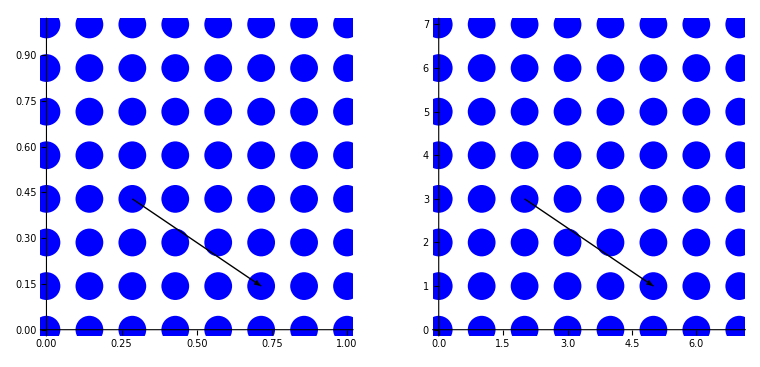

```mathematica
GraphicsRow[{
Show[ListPlot[Partition[Table[{i/n,j/n},{i,0,n},{j,0,n}]//Flatten,2],AspectRatio->1,PlotStyle->{PointSize[0.05],Blue}],Graphics[Arrow[{p1,p2}]]],
Show[ListPlot[Partition[Table[{i,j},{i,0,n},{j,0,n}]//Flatten,2],AspectRatio->1,PlotStyle->{PointSize[0.05],Blue}],Graphics[Arrow[{q1,q2}]]]
},Frame->All]

Clear[n]
```

ℤ^2 has a sum (it’s a vector space) but not a multiplication (it’s not a ring). We want to build a powerful tool to study periodic orbits of maps like the cat map. For that we need to be able to multiply points of ℤ^2. The theory of ideals endows ℤ^2 with a natural arithmetic structure turning it into a ring of entities called quadratic integers. We are going to see that by using ideals of quadratic integers one can establish the correspondence between the action of a toral automorphism and the ring multiplication. We will see that in practice the action of the map is equivalent to multiplication in the ring by one of the eigenvalue of the map. In this context periodic orbits of the toral automorphism can be understood as factorizations of quadratic integers into primes.

FIELD EXTENSIONS

First, let’s remind that the field of rational numbers ℚ is formed by the solutions of the equation

```mathematica
Reduce[s x - t== 0 && Element[s|t,Integers],x] (* division equation *)
```

(t|s)∈Integers&&((s≠0&&x==t/s)||(t==0&&s==0))

If s = 1 (the neutral element of the multiplication) we simply get the integers ℤ

```mathematica
Reduce[x-t == 0 && Element[t,Integers],x]
```

t∈Integers&&t∈Integers&&x==t

We can say that ℚ is the extension of ℤ where the equation (* division equation *) has always a solution or where the division is always possible (with divisor different than zero, the neutral element of the addition).
The following quadratic equation has no solution in the field of the real numbers ℝ. But we can build an extension of the reals by adjoining ℝ with the solution of this equation, namely {x + i y, x ∈ ℝ, y ∈ ℝ, i^2 = -1}. The extension so constructed is the field of the complex numbers ℂ.

```mathematica
Reduce[x^2+1 == 0 ,x]
```

x==-ⅈ||x==ⅈ

Field extensions are the main object of study in field theory. Generalizing the example of the complex number extending the real numbers one starts from a base field and extending it in order to satisfy additional properties. For example if the base field is ℚ one can build the smallest extension of ℚ that includes every real solution to the equation x^2 = 2 as {x + √2y, x ∈ ℚ, y ∈ ℚ}.
Field extensions are usually represented with the symbolism L:K where L is the extension field and K the base field and which is read “L over K”.
A nice feature of a field extension L:K is that it is a vector space where the vectors are in L and the scalars are in K. This is quite evident from the examples above where we write x + i y or x + √2y and interpret x and y as scalar coordinates of a two dimensional linear space and where the base of the linear space is, respectively {1,i} and {1,√2}. The dimension of the vector space is called the degree of the extension and denoted as [L:K].

In order to represent the periodic orbits of a map like the cat map using arithmetic we need x and y to be integers and find an appropriate base.

FROM ALGEBRAIC NUMBERS TO QUADRATIC INTEGERS

An algebraic number α of degree n is defined as a root of an irreducible polynomial of degree n with rational coefficients. The algebraic field ℚ(α) is the smallest subfield of the complex numbers containing α and therefore a field extension over ℚ. Those elements of ℚ(α) which are roots of monic polynomials with coefficients in ℤ are called the algebraic integers of α and denoted as ℤ(α), which is a ring but not a field. Note that though they are called “integers” they are actually irrational numbers. However they are called integers since they behave like integers from the perspective of the operations defined on ℤ(α).
Algebraic numbers have a rich and fascinating structure. Even the simple exercise of just plotting algebraic integers can lead to amazingly beautiful pictures. See the following references to learn more:

```mathematica
Hyperlink["http://www.scientificamerican.com/article/math-polynomial-roots/"]
Hyperlink["http://math.ucr.edu/home/baez/week285.html"]
Hyperlink["http://jdc.math.uwo.ca/roots/"]
```

Quadratic integers are defined as the roots of a monic quadratic polynomial with integer coefficients.

The determinant of the cat map is a monic quadratic polynomial with integer coefficients. This is why we only need to look at quadratic integers to achieve our objective.

```mathematica
Reduce[x^2-s x + t== 0 && Element[s|t,Integers],x]
```

(t|s)∈Integers&&(x==1/2 (s-√(s^2-4 t))||x==1/2 (s+√(s^2-4 t)))

Plot of quadratic integers:

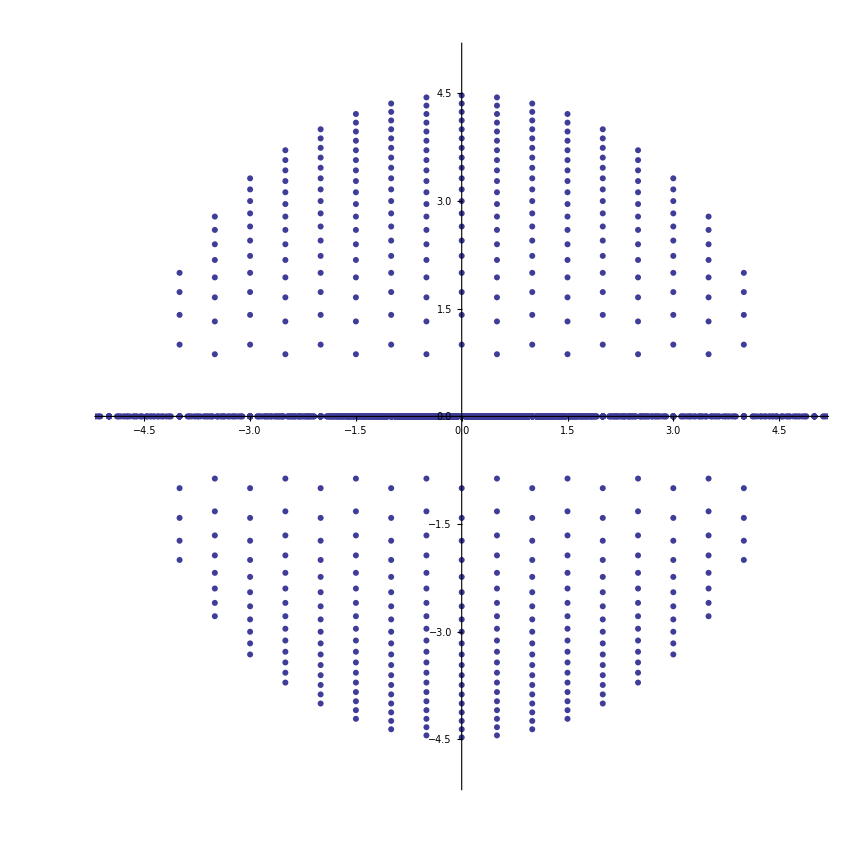

```mathematica
ListPlot[{Re[#],Im[#]}&/@Flatten@Table[{(s+Sqrt[s^2-4t])/2,(s-Sqrt[s^2-4t])/2},{s,-20,20},{t,-20,20}],AspectRatio->1,PlotRange->{{-5,5},{-5,5}},PlotStyle->{PointSize->0.005}]
```

Plot of quadratic numbers:

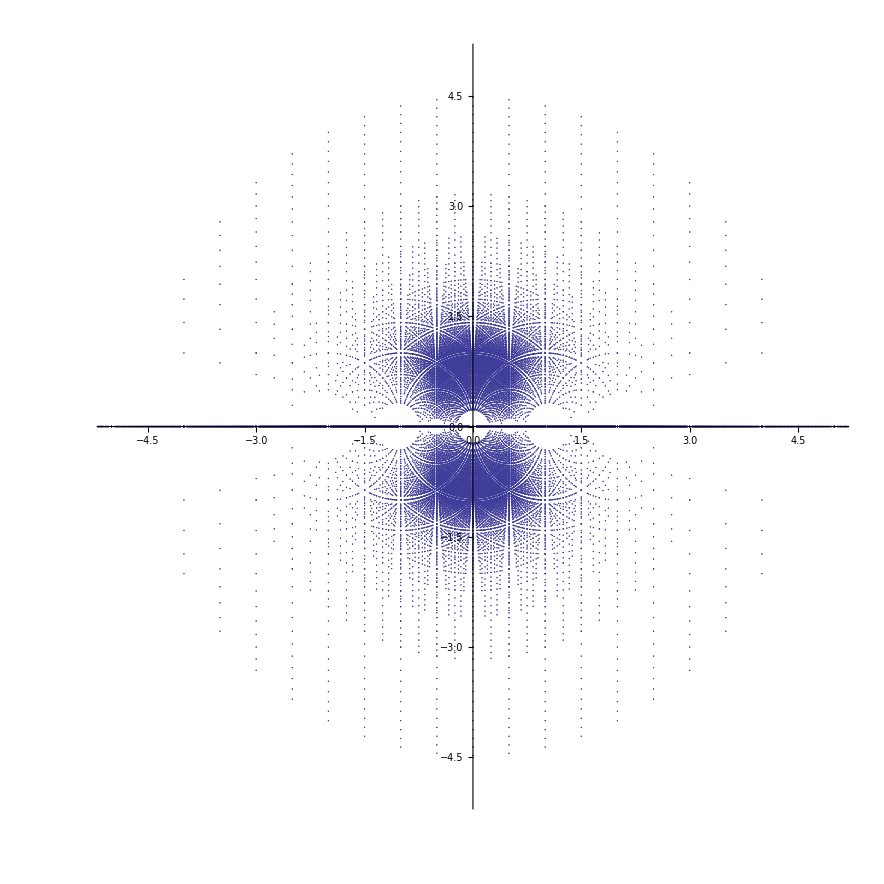

```mathematica
ListPlot[{Re[#],Im[#]}&/@Flatten@Table[{(b+Sqrt[b^2-4a c])/(2a),(b-Sqrt[b^2-4a c])/(2a)},{a,-20,20},{b,-20,20},{c,-20,20}],AspectRatio->1,PlotRange->{{-5,5},{-5,5}},PlotStyle->{PointSize->0.001}]
```

If X is the root with the plus sign the root with the minus sign is called the conjugate of X and denoted with X̄ in analogy with the conjugate of a complex number.

We can rewrite the quadratic equation in terms of the roots

```mathematica
Solve[{X==(s+Sqrt[s^2-4t])/2,X̄==(s-Sqrt[s^2-4t])/2},{s,t}]
```

{{s→X+X̄,t→X X̄}}

```mathematica
x^2 - (X+X̄)x+X X̄== 0;
```

The expression X + X̄ is called the trace of the quadratic integer X.
The expression XX̄ is called the norm of the quadratic integer X.

Then we can write

```mathematica
x^2 - trace[X]x+norm[X]== 0;
```

The case s = 0 is trivial

```mathematica
Reduce[x^2 + t== 0 && Element[t,Integers],x]
```

t∈Integers&&(x==-ⅈ √t||x==ⅈ √t)

Let’s take the case s ≠ 0 and rewrite the radical in the root expression as the product of a square of an integer with an integer with no square divisor (square-free)

```mathematica
n^2Δ== s^2 - 4  t;
```

```mathematica
decompose[radical_Integer]:=
Block[
{root=Sqrt[radical]},
If[Length[root]==0,
If[Im[root]==0,
{root,1},
{Im[root],-1}
],
If[root[[2]]==1/2,
If[Im[root]==0,
{1,root[[1]]},
{1,-Im[root[[1]]]}
],
If[Im[root]==0,
{root[[1]],root[[2]]^2},
{Im[root[[1]]],-root[[2]]^2}
]
]
]
]
```

```mathematica
Table[{{s,t},Sqrt[s^2-4 t]},{s,1,10},{t,-10,10}]//TraditionalForm
```

({{1,-10},√41} | {{1,-9},√37} | {{1,-8},√33} | {{1,-7},√29} | {{1,-6},5} | {{1,-5},√21} | {{1,-4},√17} | {{1,-3},√13} | {{1,-2},3} | {{1,-1},√5} | {{1,0},1} | {{1,1},ⅈ √3} | {{1,2},ⅈ √7} | {{1,3},ⅈ √11} | {{1,4},ⅈ √15} | {{1,5},ⅈ √19} | {{1,6},ⅈ √23} | {{1,7},3 ⅈ √3} | {{1,8},ⅈ √31} | {{1,9},ⅈ √35} | {{1,10},ⅈ √39}
{{2,-10},2 √11} | {{2,-9},2 √10} | {{2,-8},6} | {{2,-7},4 √2} | {{2,-6},2 √7} | {{2,-5},2 √6} | {{2,-4},2 √5} | {{2,-3},4} | {{2,-2},2 √3} | {{2,-1},2 √2} | {{2,0},2} | {{2,1},0} | {{2,2},2 ⅈ} | {{2,3},2 ⅈ √2} | {{2,4},2 ⅈ √3} | {{2,5},4 ⅈ} | {{2,6},2 ⅈ √5} | {{2,7},2 ⅈ √6} | {{2,8},2 ⅈ √7} | {{2,9},4 ⅈ √2} | {{2,10},6 ⅈ}
{{3,-10},7} | {{3,-9},3 √5} | {{3,-8},√41} | {{3,-7},√37} | {{3,-6},√33} | {{3,-5},√29} | {{3,-4},5} | {{3,-3},√21} | {{3,-2},√17} | {{3,-1},√13} | {{3,0},3} | {{3,1},√5} | {{3,2},1} | {{3,3},ⅈ √3} | {{3,4},ⅈ √7} | {{3,5},ⅈ √11} | {{3,6},ⅈ √15} | {{3,7},ⅈ √19} | {{3,8},ⅈ √23} | {{3,9},3 ⅈ √3} | {{3,10},ⅈ √31}
{{4,-10},2 √14} | {{4,-9},2 √13} | {{4,-8},4 √3} | {{4,-7},2 √11} | {{4,-6},2 √10} | {{4,-5},6} | {{4,-4},4 √2} | {{4,-3},2 √7} | {{4,-2},2 √6} | {{4,-1},2 √5} | {{4,0},4} | {{4,1},2 √3} | {{4,2},2 √2} | {{4,3},2} | {{4,4},0} | {{4,5},2 ⅈ} | {{4,6},2 ⅈ √2} | {{4,7},2 ⅈ √3} | {{4,8},4 ⅈ} | {{4,9},2 ⅈ √5} | {{4,10},2 ⅈ √6}
{{5,-10},√65} | {{5,-9},√61} | {{5,-8},√57} | {{5,-7},√53} | {{5,-6},7} | {{5,-5},3 √5} | {{5,-4},√41} | {{5,-3},√37} | {{5,-2},√33} | {{5,-1},√29} | {{5,0},5} | {{5,1},√21} | {{5,2},√17} | {{5,3},√13} | {{5,4},3} | {{5,5},√5} | {{5,6},1} | {{5,7},ⅈ √3} | {{5,8},ⅈ √7} | {{5,9},ⅈ √11} | {{5,10},ⅈ √15}
{{6,-10},2 √19} | {{6,-9},6 √2} | {{6,-8},2 √17} | {{6,-7},8} | {{6,-6},2 √15} | {{6,-5},2 √14} | {{6,-4},2 √13} | {{6,-3},4 √3} | {{6,-2},2 √11} | {{6,-1},2 √10} | {{6,0},6} | {{6,1},4 √2} | {{6,2},2 √7} | {{6,3},2 √6} | {{6,4},2 √5} | {{6,5},4} | {{6,6},2 √3} | {{6,7},2 √2} | {{6,8},2} | {{6,9},0} | {{6,10},2 ⅈ}
{{7,-10},√89} | {{7,-9},√85} | {{7,-8},9} | {{7,-7},√77} | {{7,-6},√73} | {{7,-5},√69} | {{7,-4},√65} | {{7,-3},√61} | {{7,-2},√57} | {{7,-1},√53} | {{7,0},7} | {{7,1},3 √5} | {{7,2},√41} | {{7,3},√37} | {{7,4},√33} | {{7,5},√29} | {{7,6},5} | {{7,7},√21} | {{7,8},√17} | {{7,9},√13} | {{7,10},3}
{{8,-10},2 √26} | {{8,-9},10} | {{8,-8},4 √6} | {{8,-7},2 √23} | {{8,-6},2 √22} | {{8,-5},2 √21} | {{8,-4},4 √5} | {{8,-3},2 √19} | {{8,-2},6 √2} | {{8,-1},2 √17} | {{8,0},8} | {{8,1},2 √15} | {{8,2},2 √14} | {{8,3},2 √13} | {{8,4},4 √3} | {{8,5},2 √11} | {{8,6},2 √10} | {{8,7},6} | {{8,8},4 √2} | {{8,9},2 √7} | {{8,10},2 √6}
{{9,-10},11} | {{9,-9},3 √13} | {{9,-8},√113} | {{9,-7},√109} | {{9,-6},√105} | {{9,-5},√101} | {{9,-4},√97} | {{9,-3},√93} | {{9,-2},√89} | {{9,-1},√85} | {{9,0},9} | {{9,1},√77} | {{9,2},√73} | {{9,3},√69} | {{9,4},√65} | {{9,5},√61} | {{9,6},√57} | {{9,7},√53} | {{9,8},7} | {{9,9},3 √5} | {{9,10},√41}
{{10,-10},2 √35} | {{10,-9},2 √34} | {{10,-8},2 √33} | {{10,-7},8 √2} | {{10,-6},2 √31} | {{10,-5},2 √30} | {{10,-4},2 √29} | {{10,-3},4 √7} | {{10,-2},6 √3} | {{10,-1},2 √26} | {{10,0},10} | {{10,1},4 √6} | {{10,2},2 √23} | {{10,3},2 √22} | {{10,4},2 √21} | {{10,5},4 √5} | {{10,6},2 √19} | {{10,7},6 √2} | {{10,8},2 √17} | {{10,9},8} | {{10,10},2 √15})

```mathematica
Table[{{s,t},decompose[s^2-4 t]},{s,1,10},{t,-10,10}]//TraditionalForm
```

((1 | -10
1 | 41) | (1 | -9
1 | 37) | (1 | -8
1 | 33) | (1 | -7
1 | 29) | (1 | -6
5 | 1) | (1 | -5
1 | 21) | (1 | -4
1 | 17) | (1 | -3
1 | 13) | (1 | -2
3 | 1) | (1 | -1
1 | 5) | (1 | 0
1 | 1) | (1 | 1
1 | -3) | (1 | 2
1 | -7) | (1 | 3
1 | -11) | (1 | 4
1 | -15) | (1 | 5
1 | -19) | (1 | 6
1 | -23) | (1 | 7
3 | -3) | (1 | 8
1 | -31) | (1 | 9
1 | -35) | (1 | 10
1 | -39)
(2 | -10
2 | 11) | (2 | -9
2 | 10) | (2 | -8
6 | 1) | (2 | -7
4 | 2) | (2 | -6
2 | 7) | (2 | -5
2 | 6) | (2 | -4
2 | 5) | (2 | -3
4 | 1) | (2 | -2
2 | 3) | (2 | -1
2 | 2) | (2 | 0
2 | 1) | (2 | 1
0 | 1) | (2 | 2
2 | -1) | (2 | 3
2 | -2) | (2 | 4
2 | -3) | (2 | 5
4 | -1) | (2 | 6
2 | -5) | (2 | 7
2 | -6) | (2 | 8
2 | -7) | (2 | 9
4 | -2) | (2 | 10
6 | -1)
(3 | -10
7 | 1) | (3 | -9
3 | 5) | (3 | -8
1 | 41) | (3 | -7
1 | 37) | (3 | -6
1 | 33) | (3 | -5
1 | 29) | (3 | -4
5 | 1) | (3 | -3
1 | 21) | (3 | -2
1 | 17) | (3 | -1
1 | 13) | (3 | 0
3 | 1) | (3 | 1
1 | 5) | (3 | 2
1 | 1) | (3 | 3
1 | -3) | (3 | 4
1 | -7) | (3 | 5
1 | -11) | (3 | 6
1 | -15) | (3 | 7
1 | -19) | (3 | 8
1 | -23) | (3 | 9
3 | -3) | (3 | 10
1 | -31)
(4 | -10
2 | 14) | (4 | -9
2 | 13) | (4 | -8
4 | 3) | (4 | -7
2 | 11) | (4 | -6
2 | 10) | (4 | -5
6 | 1) | (4 | -4
4 | 2) | (4 | -3
2 | 7) | (4 | -2
2 | 6) | (4 | -1
2 | 5) | (4 | 0
4 | 1) | (4 | 1
2 | 3) | (4 | 2
2 | 2) | (4 | 3
2 | 1) | (4 | 4
0 | 1) | (4 | 5
2 | -1) | (4 | 6
2 | -2) | (4 | 7
2 | -3) | (4 | 8
4 | -1) | (4 | 9
2 | -5) | (4 | 10
2 | -6)
(5 | -10
1 | 65) | (5 | -9
1 | 61) | (5 | -8
1 | 57) | (5 | -7
1 | 53) | (5 | -6
7 | 1) | (5 | -5
3 | 5) | (5 | -4
1 | 41) | (5 | -3
1 | 37) | (5 | -2
1 | 33) | (5 | -1
1 | 29) | (5 | 0
5 | 1) | (5 | 1
1 | 21) | (5 | 2
1 | 17) | (5 | 3
1 | 13) | (5 | 4
3 | 1) | (5 | 5
1 | 5) | (5 | 6
1 | 1) | (5 | 7
1 | -3) | (5 | 8
1 | -7) | (5 | 9
1 | -11) | (5 | 10
1 | -15)
(6 | -10
2 | 19) | (6 | -9
6 | 2) | (6 | -8
2 | 17) | (6 | -7
8 | 1) | (6 | -6
2 | 15) | (6 | -5
2 | 14) | (6 | -4
2 | 13) | (6 | -3
4 | 3) | (6 | -2
2 | 11) | (6 | -1
2 | 10) | (6 | 0
6 | 1) | (6 | 1
4 | 2) | (6 | 2
2 | 7) | (6 | 3
2 | 6) | (6 | 4
2 | 5) | (6 | 5
4 | 1) | (6 | 6
2 | 3) | (6 | 7
2 | 2) | (6 | 8
2 | 1) | (6 | 9
0 | 1) | (6 | 10
2 | -1)
(7 | -10
1 | 89) | (7 | -9
1 | 85) | (7 | -8
9 | 1) | (7 | -7
1 | 77) | (7 | -6
1 | 73) | (7 | -5
1 | 69) | (7 | -4
1 | 65) | (7 | -3
1 | 61) | (7 | -2
1 | 57) | (7 | -1
1 | 53) | (7 | 0
7 | 1) | (7 | 1
3 | 5) | (7 | 2
1 | 41) | (7 | 3
1 | 37) | (7 | 4
1 | 33) | (7 | 5
1 | 29) | (7 | 6
5 | 1) | (7 | 7
1 | 21) | (7 | 8
1 | 17) | (7 | 9
1 | 13) | (7 | 10
3 | 1)
(8 | -10
2 | 26) | (8 | -9
10 | 1) | (8 | -8
4 | 6) | (8 | -7
2 | 23) | (8 | -6
2 | 22) | (8 | -5
2 | 21) | (8 | -4
4 | 5) | (8 | -3
2 | 19) | (8 | -2
6 | 2) | (8 | -1
2 | 17) | (8 | 0
8 | 1) | (8 | 1
2 | 15) | (8 | 2
2 | 14) | (8 | 3
2 | 13) | (8 | 4
4 | 3) | (8 | 5
2 | 11) | (8 | 6
2 | 10) | (8 | 7
6 | 1) | (8 | 8
4 | 2) | (8 | 9
2 | 7) | (8 | 10
2 | 6)
(9 | -10
11 | 1) | (9 | -9
3 | 13) | (9 | -8
1 | 113) | (9 | -7
1 | 109) | (9 | -6
1 | 105) | (9 | -5
1 | 101) | (9 | -4
1 | 97) | (9 | -3
1 | 93) | (9 | -2
1 | 89) | (9 | -1
1 | 85) | (9 | 0
9 | 1) | (9 | 1
1 | 77) | (9 | 2
1 | 73) | (9 | 3
1 | 69) | (9 | 4
1 | 65) | (9 | 5
1 | 61) | (9 | 6
1 | 57) | (9 | 7
1 | 53) | (9 | 8
7 | 1) | (9 | 9
3 | 5) | (9 | 10
1 | 41)
(10 | -10
2 | 35) | (10 | -9
2 | 34) | (10 | -8
2 | 33) | (10 | -7
8 | 2) | (10 | -6
2 | 31) | (10 | -5
2 | 30) | (10 | -4
2 | 29) | (10 | -3
4 | 7) | (10 | -2
6 | 3) | (10 | -1
2 | 26) | (10 | 0
10 | 1) | (10 | 1
4 | 6) | (10 | 2
2 | 23) | (10 | 3
2 | 22) | (10 | 4
2 | 21) | (10 | 5
4 | 5) | (10 | 6
2 | 19) | (10 | 7
6 | 2) | (10 | 8
2 | 17) | (10 | 9
8 | 1) | (10 | 10
2 | 15))

```mathematica
Table[{{s,t},{#[[1]],Mod[#[[2]],4]}&@decompose[s^2-4 t]},{s,1,10},{t,-10,10}]//TraditionalForm
```

((1 | -10
1 | 1) | (1 | -9
1 | 1) | (1 | -8
1 | 1) | (1 | -7
1 | 1) | (1 | -6
5 | 1) | (1 | -5
1 | 1) | (1 | -4
1 | 1) | (1 | -3
1 | 1) | (1 | -2
3 | 1) | (1 | -1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 2
1 | 1) | (1 | 3
1 | 1) | (1 | 4
1 | 1) | (1 | 5
1 | 1) | (1 | 6
1 | 1) | (1 | 7
3 | 1) | (1 | 8
1 | 1) | (1 | 9
1 | 1) | (1 | 10
1 | 1)
(2 | -10
2 | 3) | (2 | -9
2 | 2) | (2 | -8
6 | 1) | (2 | -7
4 | 2) | (2 | -6
2 | 3) | (2 | -5
2 | 2) | (2 | -4
2 | 1) | (2 | -3
4 | 1) | (2 | -2
2 | 3) | (2 | -1
2 | 2) | (2 | 0
2 | 1) | (2 | 1
0 | 1) | (2 | 2
2 | 3) | (2 | 3
2 | 2) | (2 | 4
2 | 1) | (2 | 5
4 | 3) | (2 | 6
2 | 3) | (2 | 7
2 | 2) | (2 | 8
2 | 1) | (2 | 9
4 | 2) | (2 | 10
6 | 3)
(3 | -10
7 | 1) | (3 | -9
3 | 1) | (3 | -8
1 | 1) | (3 | -7
1 | 1) | (3 | -6
1 | 1) | (3 | -5
1 | 1) | (3 | -4
5 | 1) | (3 | -3
1 | 1) | (3 | -2
1 | 1) | (3 | -1
1 | 1) | (3 | 0
3 | 1) | (3 | 1
1 | 1) | (3 | 2
1 | 1) | (3 | 3
1 | 1) | (3 | 4
1 | 1) | (3 | 5
1 | 1) | (3 | 6
1 | 1) | (3 | 7
1 | 1) | (3 | 8
1 | 1) | (3 | 9
3 | 1) | (3 | 10
1 | 1)
(4 | -10
2 | 2) | (4 | -9
2 | 1) | (4 | -8
4 | 3) | (4 | -7
2 | 3) | (4 | -6
2 | 2) | (4 | -5
6 | 1) | (4 | -4
4 | 2) | (4 | -3
2 | 3) | (4 | -2
2 | 2) | (4 | -1
2 | 1) | (4 | 0
4 | 1) | (4 | 1
2 | 3) | (4 | 2
2 | 2) | (4 | 3
2 | 1) | (4 | 4
0 | 1) | (4 | 5
2 | 3) | (4 | 6
2 | 2) | (4 | 7
2 | 1) | (4 | 8
4 | 3) | (4 | 9
2 | 3) | (4 | 10
2 | 2)
(5 | -10
1 | 1) | (5 | -9
1 | 1) | (5 | -8
1 | 1) | (5 | -7
1 | 1) | (5 | -6
7 | 1) | (5 | -5
3 | 1) | (5 | -4
1 | 1) | (5 | -3
1 | 1) | (5 | -2
1 | 1) | (5 | -1
1 | 1) | (5 | 0
5 | 1) | (5 | 1
1 | 1) | (5 | 2
1 | 1) | (5 | 3
1 | 1) | (5 | 4
3 | 1) | (5 | 5
1 | 1) | (5 | 6
1 | 1) | (5 | 7
1 | 1) | (5 | 8
1 | 1) | (5 | 9
1 | 1) | (5 | 10
1 | 1)
(6 | -10
2 | 3) | (6 | -9
6 | 2) | (6 | -8
2 | 1) | (6 | -7
8 | 1) | (6 | -6
2 | 3) | (6 | -5
2 | 2) | (6 | -4
2 | 1) | (6 | -3
4 | 3) | (6 | -2
2 | 3) | (6 | -1
2 | 2) | (6 | 0
6 | 1) | (6 | 1
4 | 2) | (6 | 2
2 | 3) | (6 | 3
2 | 2) | (6 | 4
2 | 1) | (6 | 5
4 | 1) | (6 | 6
2 | 3) | (6 | 7
2 | 2) | (6 | 8
2 | 1) | (6 | 9
0 | 1) | (6 | 10
2 | 3)
(7 | -10
1 | 1) | (7 | -9
1 | 1) | (7 | -8
9 | 1) | (7 | -7
1 | 1) | (7 | -6
1 | 1) | (7 | -5
1 | 1) | (7 | -4
1 | 1) | (7 | -3
1 | 1) | (7 | -2
1 | 1) | (7 | -1
1 | 1) | (7 | 0
7 | 1) | (7 | 1
3 | 1) | (7 | 2
1 | 1) | (7 | 3
1 | 1) | (7 | 4
1 | 1) | (7 | 5
1 | 1) | (7 | 6
5 | 1) | (7 | 7
1 | 1) | (7 | 8
1 | 1) | (7 | 9
1 | 1) | (7 | 10
3 | 1)
(8 | -10
2 | 2) | (8 | -9
10 | 1) | (8 | -8
4 | 2) | (8 | -7
2 | 3) | (8 | -6
2 | 2) | (8 | -5
2 | 1) | (8 | -4
4 | 1) | (8 | -3
2 | 3) | (8 | -2
6 | 2) | (8 | -1
2 | 1) | (8 | 0
8 | 1) | (8 | 1
2 | 3) | (8 | 2
2 | 2) | (8 | 3
2 | 1) | (8 | 4
4 | 3) | (8 | 5
2 | 3) | (8 | 6
2 | 2) | (8 | 7
6 | 1) | (8 | 8
4 | 2) | (8 | 9
2 | 3) | (8 | 10
2 | 2)
(9 | -10
11 | 1) | (9 | -9
3 | 1) | (9 | -8
1 | 1) | (9 | -7
1 | 1) | (9 | -6
1 | 1) | (9 | -5
1 | 1) | (9 | -4
1 | 1) | (9 | -3
1 | 1) | (9 | -2
1 | 1) | (9 | -1
1 | 1) | (9 | 0
9 | 1) | (9 | 1
1 | 1) | (9 | 2
1 | 1) | (9 | 3
1 | 1) | (9 | 4
1 | 1) | (9 | 5
1 | 1) | (9 | 6
1 | 1) | (9 | 7
1 | 1) | (9 | 8
7 | 1) | (9 | 9
3 | 1) | (9 | 10
1 | 1)
(10 | -10
2 | 3) | (10 | -9
2 | 2) | (10 | -8
2 | 1) | (10 | -7
8 | 2) | (10 | -6
2 | 3) | (10 | -5
2 | 2) | (10 | -4
2 | 1) | (10 | -3
4 | 3) | (10 | -2
6 | 3) | (10 | -1
2 | 2) | (10 | 0
10 | 1) | (10 | 1
4 | 2) | (10 | 2
2 | 3) | (10 | 3
2 | 2) | (10 | 4
2 | 1) | (10 | 5
4 | 1) | (10 | 6
2 | 3) | (10 | 7
6 | 2) | (10 | 8
2 | 1) | (10 | 9
8 | 1) | (10 | 10
2 | 3))

The case Δ mod 4 = 0 is not realized because Δ is square free.

If Δ mod 4 = 2 or 3 then both s and n are even and the quadratic integer can be written as follows (with ϵ ≐ ± 1)

```mathematica
(s + ϵ n Sqrt[Δ] )/2 /.{s-> 2 u, n-> 2 ϵ v}/.{ϵ^2-> 1}//Expand
```

u+v √Δ

If Δ mod 4 = 1 then s - n is even (+ root) and s + n is even (- root).

```mathematica
Solve[{s-n == 2 u, s+n==2(u+v)},{s,n}]
Solve[{s-n == 2 u, s+n==2(u-v)},{s,n}]
```

{{s→2 u+v,n→v}}

{{s→2 u-v,n→-v}}

```mathematica
(s + ϵ n Sqrt[Δ] )/2 /.{s->  2u+v, n-> ϵ v}/.{ϵ^2-> 1}//Expand
```

u+v/2+(v √Δ)/2

If we define ω as

```mathematica
ω=If[Mod[Δ,4]==1,(1+Sqrt[Δ])/2,Sqrt[Δ]];
```

We can always write the quadratic integers as u + v ω where u, v ∈ ℤ are simply related to the monic polynomial coefficients s and t.

Then the solutions are

```mathematica
x == (s + n Sqrt[Δ] )/2 || x == (s - n Sqrt[Δ] )/2 ;
```

```mathematica
Table[{Mod[decompose[s^2+4 t][[2]],4],Expand[(s+Sqrt[s^2-4 t])/2]},{s,-10,-1},{t,-10,10}]//TraditionalForm
 Table[{Mod[decompose[s^2-4 t][[2]],4],Expand[(s-Sqrt[s^2-4 t])/2]},{s,-10,-1},{t,-10,10}]//TraditionalForm
```

({3,-5+√35} | {1,-5+√34} | {1,-5+√33} | {2,-5+4 √2} | {3,-5+√31} | {1,-5+√30} | {1,-5+√29} | {2,-5+2 √7} | {3,-5+3 √3} | {2,-5+√26} | {1,0} | {2,-5+2 √6} | {3,-5+√23} | {3,-5+√22} | {1,-5+√21} | {2,-5+2 √5} | {3,-5+√19} | {2,-5+3 √2} | {1,-5+√17} | {2,-1} | {3,-5+√15}
{1,1} | {1,-9/2+(3 √13)/2} | {1,-9/2+(√113)/2} | {1,-9/2+(√109)/2} | {1,-9/2+(√105)/2} | {1,-9/2+(√101)/2} | {1,-9/2+(√97)/2} | {1,-9/2+(√93)/2} | {1,-9/2+(√89)/2} | {1,-9/2+(√85)/2} | {1,0} | {1,-9/2+(√77)/2} | {1,-9/2+(√73)/2} | {1,-9/2+(√69)/2} | {1,-9/2+(√65)/2} | {1,-9/2+(√61)/2} | {1,-9/2+(√57)/2} | {1,-9/2+(√53)/2} | {1,-1} | {1,-9/2+(3 √5)/2} | {1,-9/2+(√41)/2}
{2,-4+√26} | {3,1} | {2,-4+2 √6} | {1,-4+√23} | {2,-4+√22} | {3,-4+√21} | {3,-4+2 √5} | {1,-4+√19} | {2,-4+3 √2} | {3,-4+√17} | {1,0} | {1,-4+√15} | {2,-4+√14} | {3,-4+√13} | {1,-4+2 √3} | {1,-4+√11} | {2,-4+√10} | {3,-1} | {2,-4+2 √2} | {1,-4+√7} | {2,-4+√6}
{1,-7/2+(√89)/2} | {1,-7/2+(√85)/2} | {1,1} | {1,-7/2+(√77)/2} | {1,-7/2+(√73)/2} | {1,-7/2+(√69)/2} | {1,-7/2+(√65)/2} | {1,-7/2+(√61)/2} | {1,-7/2+(√57)/2} | {1,-7/2+(√53)/2} | {1,0} | {1,-7/2+(3 √5)/2} | {1,-7/2+(√41)/2} | {1,-7/2+(√37)/2} | {1,-7/2+(√33)/2} | {1,-7/2+(√29)/2} | {1,-1} | {1,-7/2+(√21)/2} | {1,-7/2+(√17)/2} | {1,-7/2+(√13)/2} | {1,-2}
{3,-3+√19} | {1,-3+3 √2} | {1,-3+√17} | {2,1} | {3,-3+√15} | {1,-3+√14} | {1,-3+√13} | {2,-3+2 √3} | {3,-3+√11} | {2,-3+√10} | {1,0} | {2,-3+2 √2} | {3,-3+√7} | {3,-3+√6} | {1,-3+√5} | {2,-1} | {3,-3+√3} | {1,-3+√2} | {1,-2} | {2,-3} | {3,-3+ⅈ}
{1,-5/2+(√65)/2} | {1,-5/2+(√61)/2} | {1,-5/2+(√57)/2} | {1,-5/2+(√53)/2} | {1,1} | {1,-5/2+(3 √5)/2} | {1,-5/2+(√41)/2} | {1,-5/2+(√37)/2} | {1,-5/2+(√33)/2} | {1,-5/2+(√29)/2} | {1,0} | {1,-5/2+(√21)/2} | {1,-5/2+(√17)/2} | {1,-5/2+(√13)/2} | {1,-1} | {1,-5/2+(√5)/2} | {1,-2} | {1,-5/2+(ⅈ √3)/2} | {1,-5/2+(ⅈ √7)/2} | {1,-5/2+(ⅈ √11)/2} | {1,-5/2+(ⅈ √15)/2}
{2,-2+√14} | {3,-2+√13} | {3,-2+2 √3} | {1,-2+√11} | {2,-2+√10} | {3,1} | {1,-2+2 √2} | {1,-2+√7} | {2,-2+√6} | {3,-2+√5} | {1,0} | {1,-2+√3} | {2,-2+√2} | {3,-1} | {2,-2} | {1,-2+ⅈ} | {2,-2+ⅈ √2} | {3,-2+ⅈ √3} | {3,-2+2 ⅈ} | {1,-2+ⅈ √5} | {2,-2+ⅈ √6}
{1,2} | {1,-3/2+(3 √5)/2} | {1,-3/2+(√41)/2} | {1,-3/2+(√37)/2} | {1,-3/2+(√33)/2} | {1,-3/2+(√29)/2} | {1,1} | {1,-3/2+(√21)/2} | {1,-3/2+(√17)/2} | {1,-3/2+(√13)/2} | {1,0} | {1,-3/2+(√5)/2} | {1,-1} | {1,-3/2+(ⅈ √3)/2} | {1,-3/2+(ⅈ √7)/2} | {1,-3/2+(ⅈ √11)/2} | {1,-3/2+(ⅈ √15)/2} | {1,-3/2+(ⅈ √19)/2} | {1,-3/2+(ⅈ √23)/2} | {1,-3/2+(3 ⅈ √3)/2} | {1,-3/2+(ⅈ √31)/2}
{3,-1+√11} | {2,-1+√10} | {1,2} | {2,-1+2 √2} | {3,-1+√7} | {3,-1+√6} | {1,-1+√5} | {2,1} | {3,-1+√3} | {1,-1+√2} | {1,0} | {2,-1} | {3,-1+ⅈ} | {1,-1+ⅈ √2} | {1,-1+ⅈ √3} | {2,-1+2 ⅈ} | {3,-1+ⅈ √5} | {2,-1+ⅈ √6} | {1,-1+ⅈ √7} | {2,-1+2 ⅈ √2} | {3,-1+3 ⅈ}
{1,-1/2+(√41)/2} | {1,-1/2+(√37)/2} | {1,-1/2+(√33)/2} | {1,-1/2+(√29)/2} | {1,2} | {1,-1/2+(√21)/2} | {1,-1/2+(√17)/2} | {1,-1/2+(√13)/2} | {1,1} | {1,-1/2+(√5)/2} | {1,0} | {1,-1/2+(ⅈ √3)/2} | {1,-1/2+(ⅈ √7)/2} | {1,-1/2+(ⅈ √11)/2} | {1,-1/2+(ⅈ √15)/2} | {1,-1/2+(ⅈ √19)/2} | {1,-1/2+(ⅈ √23)/2} | {1,-1/2+(3 ⅈ √3)/2} | {1,-1/2+(ⅈ √31)/2} | {1,-1/2+(ⅈ √35)/2} | {1,-1/2+(ⅈ √39)/2})

({3,-5-√35} | {2,-5-√34} | {1,-5-√33} | {2,-5-4 √2} | {3,-5-√31} | {2,-5-√30} | {1,-5-√29} | {3,-5-2 √7} | {3,-5-3 √3} | {2,-5-√26} | {1,-10} | {2,-5-2 √6} | {3,-5-√23} | {2,-5-√22} | {1,-5-√21} | {1,-5-2 √5} | {3,-5-√19} | {2,-5-3 √2} | {1,-5-√17} | {1,-9} | {3,-5-√15}
{1,-10} | {1,-9/2-(3 √13)/2} | {1,-9/2-(√113)/2} | {1,-9/2-(√109)/2} | {1,-9/2-(√105)/2} | {1,-9/2-(√101)/2} | {1,-9/2-(√97)/2} | {1,-9/2-(√93)/2} | {1,-9/2-(√89)/2} | {1,-9/2-(√85)/2} | {1,-9} | {1,-9/2-(√77)/2} | {1,-9/2-(√73)/2} | {1,-9/2-(√69)/2} | {1,-9/2-(√65)/2} | {1,-9/2-(√61)/2} | {1,-9/2-(√57)/2} | {1,-9/2-(√53)/2} | {1,-8} | {1,-9/2-(3 √5)/2} | {1,-9/2-(√41)/2}
{2,-4-√26} | {1,-9} | {2,-4-2 √6} | {3,-4-√23} | {2,-4-√22} | {1,-4-√21} | {1,-4-2 √5} | {3,-4-√19} | {2,-4-3 √2} | {1,-4-√17} | {1,-8} | {3,-4-√15} | {2,-4-√14} | {1,-4-√13} | {3,-4-2 √3} | {3,-4-√11} | {2,-4-√10} | {1,-7} | {2,-4-2 √2} | {3,-4-√7} | {2,-4-√6}
{1,-7/2-(√89)/2} | {1,-7/2-(√85)/2} | {1,-8} | {1,-7/2-(√77)/2} | {1,-7/2-(√73)/2} | {1,-7/2-(√69)/2} | {1,-7/2-(√65)/2} | {1,-7/2-(√61)/2} | {1,-7/2-(√57)/2} | {1,-7/2-(√53)/2} | {1,-7} | {1,-7/2-(3 √5)/2} | {1,-7/2-(√41)/2} | {1,-7/2-(√37)/2} | {1,-7/2-(√33)/2} | {1,-7/2-(√29)/2} | {1,-6} | {1,-7/2-(√21)/2} | {1,-7/2-(√17)/2} | {1,-7/2-(√13)/2} | {1,-5}
{3,-3-√19} | {2,-3-3 √2} | {1,-3-√17} | {1,-7} | {3,-3-√15} | {2,-3-√14} | {1,-3-√13} | {3,-3-2 √3} | {3,-3-√11} | {2,-3-√10} | {1,-6} | {2,-3-2 √2} | {3,-3-√7} | {2,-3-√6} | {1,-3-√5} | {1,-5} | {3,-3-√3} | {2,-3-√2} | {1,-4} | {1,-3} | {3,-3-ⅈ}
{1,-5/2-(√65)/2} | {1,-5/2-(√61)/2} | {1,-5/2-(√57)/2} | {1,-5/2-(√53)/2} | {1,-6} | {1,-5/2-(3 √5)/2} | {1,-5/2-(√41)/2} | {1,-5/2-(√37)/2} | {1,-5/2-(√33)/2} | {1,-5/2-(√29)/2} | {1,-5} | {1,-5/2-(√21)/2} | {1,-5/2-(√17)/2} | {1,-5/2-(√13)/2} | {1,-4} | {1,-5/2-(√5)/2} | {1,-3} | {1,-5/2-(ⅈ √3)/2} | {1,-5/2-(ⅈ √7)/2} | {1,-5/2-(ⅈ √11)/2} | {1,-5/2-(ⅈ √15)/2}
{2,-2-√14} | {1,-2-√13} | {3,-2-2 √3} | {3,-2-√11} | {2,-2-√10} | {1,-5} | {2,-2-2 √2} | {3,-2-√7} | {2,-2-√6} | {1,-2-√5} | {1,-4} | {3,-2-√3} | {2,-2-√2} | {1,-3} | {1,-2} | {3,-2-ⅈ} | {2,-2-ⅈ √2} | {1,-2-ⅈ √3} | {3,-2-2 ⅈ} | {3,-2-ⅈ √5} | {2,-2-ⅈ √6}
{1,-5} | {1,-3/2-(3 √5)/2} | {1,-3/2-(√41)/2} | {1,-3/2-(√37)/2} | {1,-3/2-(√33)/2} | {1,-3/2-(√29)/2} | {1,-4} | {1,-3/2-(√21)/2} | {1,-3/2-(√17)/2} | {1,-3/2-(√13)/2} | {1,-3} | {1,-3/2-(√5)/2} | {1,-2} | {1,-3/2-(ⅈ √3)/2} | {1,-3/2-(ⅈ √7)/2} | {1,-3/2-(ⅈ √11)/2} | {1,-3/2-(ⅈ √15)/2} | {1,-3/2-(ⅈ √19)/2} | {1,-3/2-(ⅈ √23)/2} | {1,-3/2-(3 ⅈ √3)/2} | {1,-3/2-(ⅈ √31)/2}
{3,-1-√11} | {2,-1-√10} | {1,-4} | {2,-1-2 √2} | {3,-1-√7} | {2,-1-√6} | {1,-1-√5} | {1,-3} | {3,-1-√3} | {2,-1-√2} | {1,-2} | {1,-1} | {3,-1-ⅈ} | {2,-1-ⅈ √2} | {1,-1-ⅈ √3} | {3,-1-2 ⅈ} | {3,-1-ⅈ √5} | {2,-1-ⅈ √6} | {1,-1-ⅈ √7} | {2,-1-2 ⅈ √2} | {3,-1-3 ⅈ}
{1,-1/2-(√41)/2} | {1,-1/2-(√37)/2} | {1,-1/2-(√33)/2} | {1,-1/2-(√29)/2} | {1,-3} | {1,-1/2-(√21)/2} | {1,-1/2-(√17)/2} | {1,-1/2-(√13)/2} | {1,-2} | {1,-1/2-(√5)/2} | {1,-1} | {1,-1/2-(ⅈ √3)/2} | {1,-1/2-(ⅈ √7)/2} | {1,-1/2-(ⅈ √11)/2} | {1,-1/2-(ⅈ √15)/2} | {1,-1/2-(ⅈ √19)/2} | {1,-1/2-(ⅈ √23)/2} | {1,-1/2-(3 ⅈ √3)/2} | {1,-1/2-(ⅈ √31)/2} | {1,-1/2-(ⅈ √35)/2} | {1,-1/2-(ⅈ √39)/2})

RINGS OF QUADRATIC INTEGERS

The quantity d defined as Δ if Δ mod 4 = 1 and 4Δ otherwise is called the field discriminant. All numbers sharing the same discriminant form a set closed over the four arithmetic operations except division by 0 and it is denoted with ℝ(√d) or ℝ(ω) depending on which parameter is preferred. The subset of this field formed by quadratic integers is called a Dedekind domain and denoted with D_1(d) which is a ring (closed under addition, subtraction and multiplication only).

Let’s extend the integers by adjoining ℤ with a root of a monic quadratic polynomial with a given ω (that is the quadratic integer u + v ω) and call the resulting extension a ring of quadratic integers. The elements of a ring of quadratic integers can be mapped to a lattice by writing them as z = i + j ω where (i, j) ∈ ℤ^2 and the u and v of the quadratic integer expression have been subsumed into the i and j variables.

The pair [1, ω] is called the canonical basis of the quadratic ring and the quadratic ring generated by this basis is denoted as ℤ(ω).

Note that the conjugation operation is equivalent to mapping the lattice spanned by [1, ω] to the lattice spanned by [1, ω̄] which are therefore conjugate to each other.

```mathematica
(x-(i+j Sqrt[Δ]))(x-(i-j Sqrt[Δ]))//Expand
(x-(i+j (1+Sqrt[Δ])/2))(x-(i+j (1-Sqrt[Δ])/2))//Expand
```

i^2-2 i x+x^2-j^2 Δ

i^2+i j+j^2/4-2 i x-j x+x^2-(j^2 Δ)/4

The trace of a quadratic integer can be written in terms of the lattice points as

```mathematica
trace[{i_,j_},Δ_Integer]:=
If[Mod[Δ,4]==1,
2i+j,
2 i
];
```

The multiplication of two quadratic integers (both elements of the same quadratic ring ℤ(ω)) can be written in terms of the lattice points and the radical

```mathematica
(i + Sqrt[Δ]j)(k + Sqrt[Δ]l)//Expand
 (i + (1+Sqrt[Δ])j/2)(k+ (1+ Sqrt[Δ])l/2)//Expand
%-(i l + j k + j l)(1+Sqrt[Δ])/2 // Expand
```

i k+j k √Δ+i l √Δ+j l Δ

i k+(j k)/2+(i l)/2+(j l)/4+1/2 j k √Δ+1/2 i l √Δ+1/2 j l √Δ+(j l Δ)/4

i k-(j l)/4+(j l Δ)/4

```mathematica
multiply[{i_,j_},{k_,l_},Δ_Integer]:=
If[Mod[Δ,4]==1,
{i k + j l (Δ-1)/4,i l + j k + j l},
{i k+j l Δ,i l + j k}
];
```

Now that we have the multiplication defined in ℤ(ω) we can see that the action of the cat map is equivalent to multiplication by the cat map larger eigenvalue.

```mathematica
ω /.{Δ-> 5}
σ/.σDef
```

1/2 (1+√5)

1/2 (3+√5)

```mathematica
M.{x,y}
multiply[{1,1},{x,y},5]
```

{x+y,x+2 y}

{x+y,x+2 y}

However, what we are really looking at is the map defined on the toroidal lattice ℤ^2/nℤ^2 representing all rational points of the form (i/n,j/n) with i and j < n. On the lattice we just take the remainder of the division by n. We have to be able to do the same in ℤ(ω) that is we need to find the equivalent in ℤ(ω) of the modulo n function.
Once we are able to do that a periodic orbit of the map of period m is just a solution to the equation 
σ^m(i+j ω) ≡ (i+j ω) mod n
whatever mod n means in ℤ(ω).

We need a generalization of the Euclidean division algorithm valid for the natural integers. We want to be able to factor quadratic integers, that is to find the divisors. Generally speaking, this is possible if there is a function N defined on an integral domain R called Euclidean function (alternatively norm function, valuation function, degree function) such as there exist q (the quotient) and r (the remainder) in R such that a = bq+r and either r = 0 or N(r) < N(b). If such a function can be found R is called an Euclidean domain or Euclidean ring. The norm introduced previously is a candidate for the Euclidean function of the quadratic ring.

The norm of a quadratic integer can be written in terms of the lattice points and the radical as

```mathematica
(i + Sqrt[Δ]j)(i - Sqrt[Δ]j)//Expand
 (i + (1+Sqrt[Δ])j/2)(i+ (1- Sqrt[Δ])j/2)//Expand
((2 i+j)^2-Δ j^2)/4//Expand
```

i^2-j^2 Δ

i^2+i j+j^2/4-(j^2 Δ)/4

i^2+i j+j^2/4-(j^2 Δ)/4

```mathematica
norm[{i_,j_},Δ_Integer]:=
If[Mod[Δ,4]==1,
((2 i+j)^2- j^2 Δ)/4,
i^2-j^2 Δ
];
```

One can extend the ring ℤ(ω) to the field ℚ(ω) by allowing every element different than 0 to have an inverse with respect to the multiplication.

The division of two quadratic integers (both in the same quadratic field ℚ(ω)) can be written in terms of the lattice points and the radical by multiplying both numerator and denominator with the conjugate of the denominator (rationalization of the denominator)

```mathematica
(i + Sqrt[Δ]j)(k - Sqrt[Δ]l)//Expand
 (k + Sqrt[Δ]l)(k - Sqrt[Δ]l)//Expand
```

i k+j k √Δ-i l √Δ-j l Δ

k^2-l^2 Δ

```mathematica
(i + (1+Sqrt[Δ])j/2)(k+ (1- Sqrt[Δ])l/2)//Expand
 %-(-i l + j k )(1+Sqrt[Δ])/2 // Expand
(k + (1+Sqrt[Δ])l/2)(k+ (1- Sqrt[Δ])l/2)//Expand
((2 k+l)^2- l^2 Δ)/4//Expand
```

i k+(j k)/2+(i l)/2+(j l)/4+1/2 j k √Δ-1/2 i l √Δ-(j l Δ)/4

i k+i l+(j l)/4-(j l Δ)/4

k^2+k l+l^2/4-(l^2 Δ)/4

k^2+k l+l^2/4-(l^2 Δ)/4

```mathematica
divide[{i_,j_},{k_,l_},Δ_Integer]:=
If[Mod[Δ,4]==1,
4{i k - j l (Δ-1)/4,-i l + j k }/(((2 k+l)^2- l^2 Δ)),
{i k-j l Δ,-i l + j k}/(k^2-l^2 Δ)
];
```

However we are not done yet. Because ℤ(ω) has a more complicated multiplication structure than ℤ we need to resolve a fundamental ambiguity.

UNITS AND PRIMES OF QUADRATIC INTEGERS

A prime number in a ring is defined as a number that can only divide 1 and itself. Primes are important because they can be used to uniquely factorize all other integers. It makes sense to talk of quadratic primes but it is not trivial. We need to define what a divisor is and what a unit is in a ring of quadratic integers first. 
First of all a non zero quadratic integer α is a divisor of another quadratic integer β or divides β iff a quadratic integer γ is found such that αγ == β.
A unit in a ring is a number that divides all other numbers in the ring. That is it has an inverse in the ring. Because of this reason it is also called a divisor of 1. The only units in ℤ are 1 and -1. Note that the notion of unit is not the same as the notion of identity. The identity or neutral element of the multiplication is 1.
The case of a quadratic ring ℤ(ω) is more interesting. Generally ℤ(ω) admits units other than 1 and -1.
Because there are units other than 1 and -1 we have to be more careful with definitions. The critical fact here is that when there are units other than 1 and -1 the unique factorization theorem may not hold, that is the factorization of an integer into primes may not be unique apart from order.

An element ε of ℤ(ω) that has an inverse in ℤ(ω) is a unit.
Two elements α and β in ℤ(ω) are associates whenever β = εα where ε is a unit.
An element of ℤ(ω) is composite if it is the product of two non units.
An element of ℤ(ω) is irreducible if it is not a unit and it is not composite. An irreducible integer is divisible only by itself, its associates and the units.
An element of ℤ(ω) is prime if it is not zero, it is not a unit and whenever it divides αβ in ℤ(ω) it either divides α or divides β.

Though all primes are irreducibles there are rings where there are irreducibles that are not primes. These are the rings where factorization of an element into irreducible factors is not unique. Only in rings where unique factorization holds irreducibles and primes are identical.
Because unique factorization is not always valid we need a different notion of integer to work with such as we can recover unique factorization in primes for these new kind of integers. Instead of working with the integers, namely the elements of the ring ℤ(ω), we will work with equivalence classes of them.
We want to construct a subset I of a ring R (such as ℤ(ω)) so that R/I has the same ring structure of R but the equivalence class corresponding to I is the 0 of this new ring (the neutral element of the addition). If I is the 0 of the new ring the sum of any two elements of the new ring that are 0 should be 0 and the product of a generic element of the new ring with a 0 should be 0 as well. Another way of saying this is that we want I to be the kernel of a homomorphism from the original ring to the new ring.

Let’s call a subset I such as this an ideal in R and we define it as a subgroup of R with respect to the addition of the ring with the property that the product of every element of I with every element of R is in I (it absorbs the multiplication by elements of R). Alternatively we can define the ideal as a non empty subset of R such that the difference of two elements of I is in I and that it absorbs the multiplication by elements of R. There is a one to one correspondence between ideals of R and congruence relations of R (equivalence relations respecting the ring structure) so that ideals are just another name for congruences of a ring.

The sum of two ideals A and B is just the ideal generated by the sums of all elements of A with all elements of B. The product of two ideals A and B is the ideal AB generated by all products of an element of A with an element of B. It turns out that AB is contained in the intersection of A and B.

The set of all elements ϱα where ϱ is a fixed element of R and α is in R is an ideal. We say that this ideal is generated by ϱ, we call it a principal ideal and denote it as (ϱ). Special cases are (0) which has only one element and (1) which is identical to R.

If all ideals in R are principal ideals we call R a principal ideal domain. The critical fact here is that R is a principal ideal domain iff unique factorization holds in R.

Now we can make another step forward. The torus ℤ^2/nℤ^2 is identified with the ideal (n) in ℤ(ω). The congruence defining ℤ^2/nℤ^2 is: (i,j) and (k,l) are identified iff (i-k,j-l) = (n r, n s) for some (r,s) in ℤ^2. Then we can define the corresponding congruence in ℤ(ω) as: α and β are congruent modulo (n) iff α - β is in (n).
The equation defining periodic orbits of period m and divisor n, namely σ^m(i+j ω) ≡ (i+j ω) mod (n), is now fully defined. Let’s see how to solve it.
Now σ is a unit so σ I = I for any ideal I and therefore (n) itself is an invariant of the map. Since we are doing arithmetics modulo (n) the only other invariants of the map (the periodic orbits) are the divisors of (n) itself. Therefore solving the equation for the periodic orbits is equivalent to the factorization of (n).

Let’s say that a prime ideal of a commutative ring R is an ideal satisfying the two properties:
An ideal P of R is prime if it is not R and
if αβ (with α and β in R)  is in P then either α or β are in P as well.
These properties generalize the definition of prime from integers to ideals.

The invention of prime ideals by Richard Dedekind was the breakthrough that allowed to generalize the fundamental theorem of arithmetic to rings of algebraic integers by replacing elements of the ring with ideals and primes with prime ideals.

If a quadratic ring is Euclidean (an Euclidean function can be found) it is also a principal ideal domain and therefore prime factorization is unique. All the quadratic rings that are norm Euclidean (the ones such as the norm is an Euclidean function) are known. They have Δ = -11, -7, -3, -2, -1, 2, 3, 5, 6, 7, 11, 13, 17, 19, 21, 29, 33, 41, 57 and 73. There are quadratic rings that are Euclidean but the norm is not an Euclidean function such as the case of Δ = 69. Further on we have the quadratic rings that are principal ideal domains but they are not Euclidean, for example Δ = -19. Finally we have quadratic rings that are not even principal ideal domains such as the case of Δ = -5.

The only quadratic rings that are complex (Δ < 0) and have unique factorization are the ones with Δ = -1, -2, -3, -7, -11, -19, -43, -67, -163.

We do not know how many real quadratic rings (Δ > 0) have unique factorization. There may be an infinity of them.

All real quadratic rings that are principal ideal domains with Δ < 100 and

Δ = 1 mod 4 have Δ = 5, 13, 17, 21, 29, 33, 37, 41, 53, 57, 61, 69, 73, 77, 89, 93, 97;

Δ = 2 mod 4 have Δ = 2, 6, 14, 22, 38, 46, 62, 86, 94;

Δ = 3 mod 4 have Δ = 3, 7, 11, 19, 23, 31, 43, 47, 59, 67, 71, 83.

The factorization of a rational prime ideal into prime ideals is related to the concept of quadratic residue. An integer q is a quadratic residue modulo n if it is congruent to a perfect square modulo n, that is if there is an integer x such that x^2 ≡ q mod n. For example 3 is a residue modulo 11 because 25 ≡ 3 modulo 11 but 8 is not.

When dealing with quadratic residues it is useful to introduce the so called quadratic character or Legendre symbol (a/p) for an integer a and an odd prime p. We consider only odd primes because every integer is a quadratic residue modulo 2 and it is understood that these are rational primes not prime ideals.
If a is not a residue modulo p then (a/p) = -1.
If a is a residue modulo p then (a/p) = 1.
If p is a divisor of a then (a/p) = 0.
The Legendre symbol has several properties useful for computation:

(1/p) = 1
(-1/p) = 1 iff p is congruent to 1 modulo 4
(2/p) = 1 iff p is congruent to ±1 modulo 8
if a ≡ b modulo p then (a/p) = (b/p)
(ab/p) = (a/p)(b/p)

Euler discovered and Gauss proved the so called quadratic reciprocity law: if p and q are odd primes (p/q) = ±(q/p) where the - sign is taken if p and q are both congruent to 3 modulo 4. This law comes very useful when computing quadratic characters.

Now let’s go back to prime ideal factorization. Prime ideals are factors of rational prime ideals (p). If d is the field discriminant and p a rational prime there are three possibilities:
We say that the rational prime ideal (p) is inert, that is it has no factors: (p) = (p) iff (d/p) = -1.
(p) splits, that is it has two distinct prime ideal factors: (p) = P_1 P_2 iff (d/p) = 1.
(p) ramifies, that is it has two identical prime ideal factors: (p) = P^2 iff (d/p) = 0.

When d is a field discriminant (that is either d is congruent to 1 modulo 4 and square free or d/4 is not congruent to 1 modulo 4 and d/4 is square free) the Legendre symbol (d/p) is called a Kronecker symbol.

The Kronecker symbol enjoys many useful properties:
(d/2) = 1 iff d ≡ 1 modulo 8
(d/2) = -1 iff d ≡ 5 modulo 8
(d/2) = 0 iff d ≡ 0 modulo 4
(d/1) = 1
if the gcd of d and a is greater than 1 then (d/a) = 0
if a ≡ b modulo d then (d/a) = (d/b)
(d/(d-a)) = (d/a)
(d/a) = (d/p_1)...(d/p_k) where p_1 ... p_k are the rational prime factors of a.

The units of a ring of quadratic integers, are determined by using the theorem that states that a quadratic integer is a unit iff the norm is equal to ±1.

```mathematica
Solve[i^2 - j^2 Δ== 1,j]
Solve[i^2 - j^2 Δ== -1,j]
```

{{j→-(√(-1+i^2))/(√Δ)},{j→(√(-1+i^2))/(√Δ)}}

{{j→-(√(1+i^2))/(√Δ)},{j→(√(1+i^2))/(√Δ)}}

```mathematica
Solve[((2 i+j)^2- j^2 Δ)/4== 1,j]
Solve[((2 i+j)^2- j^2 Δ)/4== -1,j]
```

{{j→(2 (i-√(1-Δ+i^2 Δ)))/(-1+Δ)},{j→(2 (i+√(1-Δ+i^2 Δ)))/(-1+Δ)}}

{{j→(2 (i-√(-1+Δ+i^2 Δ)))/(-1+Δ)},{j→(2 (i+√(-1+Δ+i^2 Δ)))/(-1+Δ)}}

Let’s review a few examples.

Let’s study the the Gaussian integers i + j √-1or ℤ(√-1). The units form the cyclic group C_4 spanned by ±1, ±ω. If x is a Gaussian integer than ±x, ±ωx are associates.

```mathematica
Mod[-1,4]
```

3

```mathematica
Reduce[i^2 + j^2  == 1  && Element[i|j,Integers],{i,j}]
Reduce[i^2 + j^2  == -1  && Element[i|j,Integers],{i,j}]
```

(i==-1&&j==0)||(i==0&&j==-1)||(i==0&&j==1)||(i==1&&j==0)

False

The condition that the norm be 1 or -1 for a complex quadratic integer means that the unit must lie on the unit circle in the complex plane.

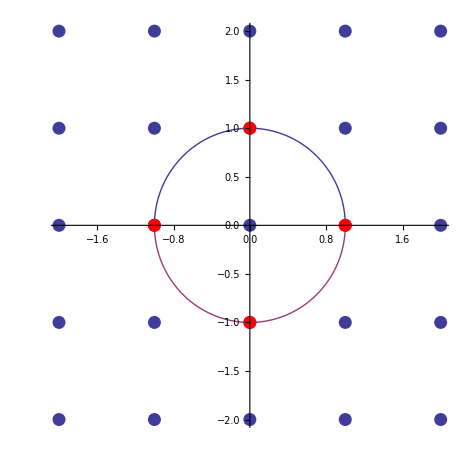

```mathematica
solutions={{1,0},{-1,0},{0,1},{0,-1}};
solutionsGraphics=Graphics[{PointSize[0.02],Red,Point[#]}&/@solutions];
Show[
Plot[{Sqrt[1-i^2],-Sqrt[1-i^2]},{i,-1,1},PlotStyle->Thick],ListPlot[Partition[Table[{i,j},{i,-2,2},{j,-2,2}]//Flatten,2],PlotStyle->PointSize[0.02]],
solutionsGraphics,
PlotRange->{{-2,2},{-2,2}},AxesOrigin->{0,0},AspectRatio->Automatic]
```

```mathematica
NestList[multiply[{0,1},#,-1]&,{0,1},4]
```

{{0,1},{-1,0},{0,-1},{1,0},{0,1}}

The fundamental theorem of arithmetic holds for ℤ(√-1) as was first proved by Gauss, namely prime factorization is unique and therefore the Gaussian integers form a principal ideal domain. However the primes in ℤ(√-1) are different than the primes in ℤ.
For example 2 and 5 are not Gaussian primes because their factors are different than themselves and are not units:

```mathematica
{2,0}==multiply[{1,1},{1,-1},-1]
norm[{1,1},-1]
norm[{1,-1},-1]
```

True

2

2

```mathematica
{5,0}==multiply[{1,2},{1,-2},-1]
norm[{1,2},-1]
norm[{1,-2},-1]
```

True

5

5

Prime numbers of the form 4n+1 cannot be Gaussian primes because it would contradict Fermat’s theorem. The prime numbers that are also Gaussian primes are of the form 4n+3.
Fore example 3 is a prime. Which one can determine by contradiction.
Let’s assume a and b the prime factors of 3. Then 9 = N(3) = N(a b) = N(a) N(b). Since neither a and b must be unity N(a) = N(b) = 3. However this latter equation has no integer solution so 3 must be prime.

```mathematica
Reduce[a1^2 + a2^2== 3 && Element[a1,Integers] && Element[a2,Integers],{a1,a2}]
```

False

A Guassian integer is Gaussian prime if one of the following condition is satisfied:
1) if both i and j are non zero i^2 + j^2 is a natural prime
2) if i = 0 and |j| is a natural prime congruent to 3 modulo 4
3) if j = 0 and |i| is a natural prime congruent to 3 modulo 4

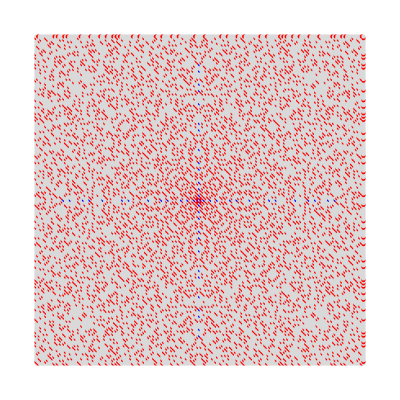

```mathematica
Show[Map[
Which[#[[1]]#[[2]]!=0,
If[ PrimeQ[#[[1]]^2+#[[2]]^2],
Graphics[{Red,Point[#]}],
Graphics[{LightGray,Point[#]}]],
#[[1]]^2+#[[2]]^2==1,Graphics[{Purple,Point[#]}],
#[[1]]==0 &&Mod[Abs[#[[2]]],4]==3&& PrimeQ[Abs[#[[2]]]] ,Graphics[{Blue,Point[#]}],
#[[2]]==0 &&Mod[Abs[#[[1]]],4]==3 && PrimeQ[Abs[#[[1]]]],Graphics[{Blue,Point[#]}],
True,Graphics[{LightGray,Point[#]}]
]&,
Table[{i,j},{i,-100,100},{j,-100,100}],
{2}]//Flatten,ImageSize->Scaled[1]]
```

Let’s now look at the case of the imaginary quadratic integers i + j √-2or ℤ(√-2). The units form the cyclic group C_2 spanned by ±1.

```mathematica
Mod[-2,4]
```

2

```mathematica
Reduce[i^2 +2 j^2  == 1  && Element[i|j,Integers],{i,j}]
Reduce[i^2 - 2j^2  == -1  && Element[i|j,Integers],{i,j}]
```

(i==-1&&j==0)||(i==1&&j==0)

(C[1]∈Integers&&C[1]≥0&&i==1/2 ((3-2 √2)^C[1]+√2 (3-2 √2)^C[1]+(3+2 √2)^C[1]-√2 (3+2 √2)^C[1])&&j==1/4 (2 (3-2 √2)^C[1]+√2 (3-2 √2)^C[1]+2 (3+2 √2)^C[1]-√2 (3+2 √2)^C[1]))||(C[1]∈Integers&&C[1]≥0&&i==1/2 ((3-2 √2)^C[1]+√2 (3-2 √2)^C[1]+(3+2 √2)^C[1]-√2 (3+2 √2)^C[1])&&j==1/4 (-2 (3-2 √2)^C[1]-√2 (3-2 √2)^C[1]-2 (3+2 √2)^C[1]+√2 (3+2 √2)^C[1]))||(C[1]∈Integers&&C[1]≥0&&i==1/2 (-(3-2 √2)^C[1]-√2 (3-2 √2)^C[1]-(3+2 √2)^C[1]+√2 (3+2 √2)^C[1])&&j==1/4 (2 (3-2 √2)^C[1]+√2 (3-2 √2)^C[1]+2 (3+2 √2)^C[1]-√2 (3+2 √2)^C[1]))||(C[1]∈Integers&&C[1]≥0&&i==1/2 (-(3-2 √2)^C[1]-√2 (3-2 √2)^C[1]-(3+2 √2)^C[1]+√2 (3+2 √2)^C[1])&&j==1/4 (-2 (3-2 √2)^C[1]-√2 (3-2 √2)^C[1]-2 (3+2 √2)^C[1]+√2 (3+2 √2)^C[1]))

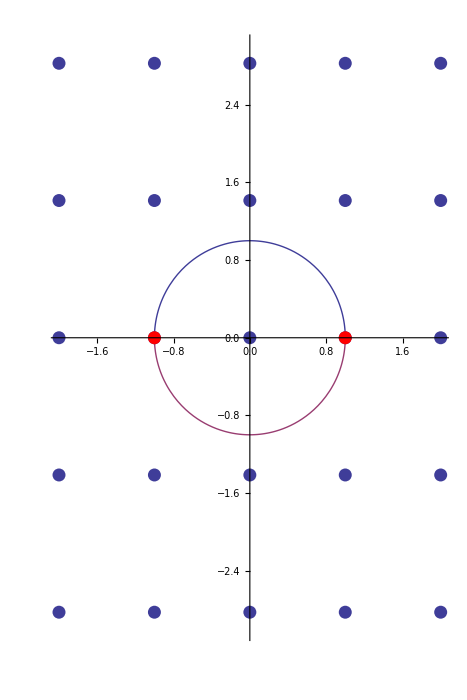

```mathematica
solutions={{1,0},{-1,0}};
solutionsGraphics=Graphics[{PointSize[0.02],Red,Point[#]}&/@solutions];
Show[
Plot[{Sqrt[1-i^2],-Sqrt[1-i^2]},{i,-1,1},PlotStyle->Thick],ListPlot[Partition[Table[{i,Sqrt[2]j},{i,-2,2},{j,-2,2}]//Flatten,2],PlotStyle->PointSize[0.02]],
solutionsGraphics,
PlotRange->{{-2,2},{-3,3}},AxesOrigin->{0,0},AspectRatio->Automatic]
```

```mathematica
NestList[multiply[{-1,0},#,-2]&,{-1,0},2]
```

{{-1,0},{1,0},{-1,0}}

The fundamental theorem of arithmetic holds for ℤ(√-2) and therefore prime factorization is unique and all ideals are principal ideals. However once again the primes in ℤ(√-2) are different than in ℤ.
For example 2 and 3 are not primes in ℤ(√-2) because their factors are different than themselves and are not units:

```mathematica
{2,0}==multiply[{0,1},{0,-1},-2]
norm[{0,1},-2]
norm[{0,-1},-2]
```

True

2

2

```mathematica
{3,0}==multiply[{1,1},{1,-1},-2]
norm[{1,1},-2]
norm[{1,-1},-2]
```

True

3

3

However 5 is a prime in ℤ(√-2). Which one can determine by contradiction.
Let’s assume a and b the prime factors of 5. Then 25 = N(5) = N(a b) = N(a) N(b). Since neither a and b must be unity N(a) = N(b) = 5. However this latter equation has no integer solution so 5 must be prime.

```mathematica
Reduce[a1^2 + 2 a2^2== 5 && Element[a1,Integers] && Element[a2,Integers],{a1,a2}]
```

False

Let’s consider the case of the Eisenstein integers i + j 1/2 (1+ⅈ √3)or ℤ(1/2 (1+ⅈ √3)).  The units form the cyclic group C_6 spanned by ±1, ±ω, ±ω^2.

```mathematica
Mod[-3,4]
Arg[1/2 (1+ⅈ √3)]
```

1

π/3

```mathematica
((2 i+j)^2- j^2 (-3))/4//Expand
```

i^2+i j+j^2

```mathematica
Reduce[((2 i+j)^2+3 j^2 )/4 == 1  && Element[i|j,Integers],{i,j}]
```

(i==-1&&j==0)||(i==-1&&j==1)||(i==0&&j==-1)||(i==0&&j==1)||(i==1&&j==-1)||(i==1&&j==0)

```mathematica
Solve[((2 i+j)^2+3 j^2 )/4 == 1  ,j]
```

{{j→1/2 (-i-√(4-3 i^2))},{j→1/2 (-i+√(4-3 i^2))}}

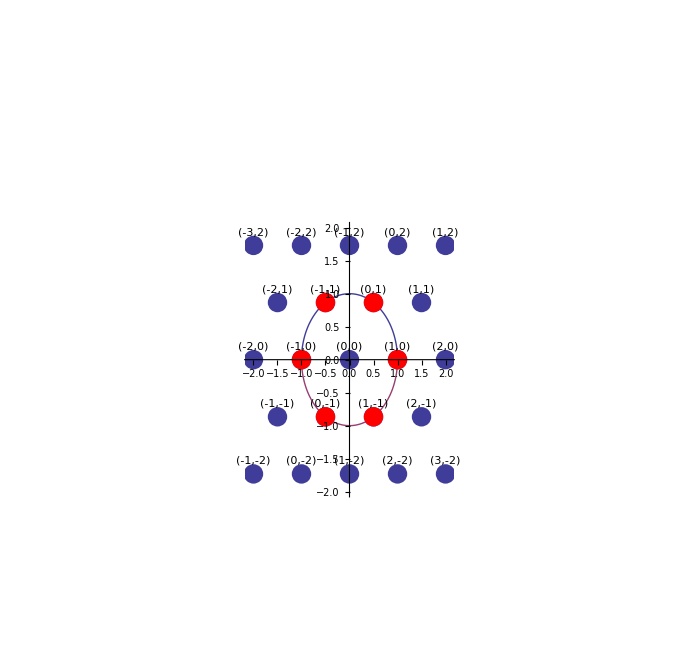

```mathematica
solutions={{1,0},{-1,0},{0,1},{0,-1},{-1,1},{1,-1}};
points=Partition[Table[{i+j/2,Sqrt[3]j/2},{i,-4,4},{j,-4,4}]//Flatten,2];
solutionsGraphics=Graphics[{PointSize[0.02],Red,Point[{#[[1]]+#[[2]]/2,Sqrt[3]#[[2]]/2}]}&/@solutions];
text = Graphics[Text[Style["("<>ToString[#[[1]]]<>","<>ToString[#[[2]]]<>")",Large],{#[[1]]+#[[2]]/2,Sqrt[3]#[[2]]/2+0.2}]]&/@Partition[Table[{i,j},{i,-4,4},{j,-4,4}]//Flatten,2];
Show[
Plot[{Sqrt[1-i^2],-Sqrt[1-i^2]},{i,-1,1},PlotStyle->Thick],ListPlot[points,PlotStyle->PointSize[0.02]],
solutionsGraphics,
text,
PlotRange->{{-2.1,2.1},{-2,2}},AxesOrigin->{0,0},AspectRatio->Automatic]
```

```mathematica
NestList[multiply[{0,1},#,-3]&,{0,1},6]
```

{{0,1},{-1,1},{-1,0},{0,-1},{1,-1},{1,0},{0,1}}

It is convenient to define “positive” Eisenstein integers as the ones within the triangular sector delimited by the lines starting at 0 with angles ±30°.
If we define the associates of an Eisenstein integer a as ±a, ±ωa, ±ω^2a we can say that every non zero Eisenstein integer has a unique factorization up to associates. In other words it is uniquely the product of powers of -1, ω and “positive” Eisenstein primes.

Eisenstein proved that the fundamental theorem of arithmetic holds for these integers just like it did for the Gaussian integers.
One of the two mutually exclusive conditions must be satisfied for an Eisenstein integer to be Eisenstein prime:
1) it is the product of a unit and a natural prime of the form 3n-1
2) N(i+jω)=(i+jω)(i+jω^2) = i^2 + ij+ j^2 is a natural prime necessarily congruent to 1 modulo 6

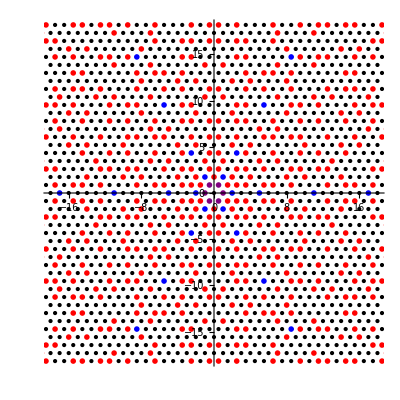

```mathematica
EisPrim={2,5,11,17};
EisPrim=Join[%,-%];
EisPrim=Join[EisPrim,EisPrim(1+I Sqrt[3])/2,EisPrim((1+I Sqrt[3])/2)^2];
EisPrim={Re[#],Im[#]}&/@%;

Show[
ListPlot[{0,0},PlotRange->{{-18,18},{-18,18}},AspectRatio->1],
Map[
Which[
PrimeQ[norm[#,-3]],
Graphics[{PointSize[0.01],Red,Point[{#[[1]]+#[[2]]/2,Sqrt[3]#[[2]]/2}]}],
norm[#,-3]==1,
Graphics[{PointSize[0.01],Purple,Point[{#[[1]]+#[[2]]/2,Sqrt[3]#[[2]]/2}]}],
True,
Graphics[{Black,Point[{#[[1]]+#[[2]]/2,Sqrt[3]#[[2]]/2}]}]
]&,
Table[{i,j},{i,-30,30},{j,-30,30}],
{2}],
Graphics[{PointSize[0.01],Blue,Point[#]}]&/@EisPrim,
ImageSize->Scaled[1]
]
```

The case of the real quadratic integers i + j √2. The units are  (1/2 (1+√2) )^n, n ∈ ℤ where 1/2 (1+√2) is the silver mean.

```mathematica
Mod[2,4]
```

2

```mathematica
Solve[i^2-2j^2==1,j]
Solve[i^2-2j^2==-1,j]
```

{{j→-(√(-1+i^2))/(√2)},{j→(√(-1+i^2))/(√2)}}

{{j→-(√(1+i^2))/(√2)},{j→(√(1+i^2))/(√2)}}

The condition that the norm be 1 or -1 for a real quadratic integer means that the unit must lie on a branch of a unit hyperbola in the real plane. That’s why we can have infinitely many units.

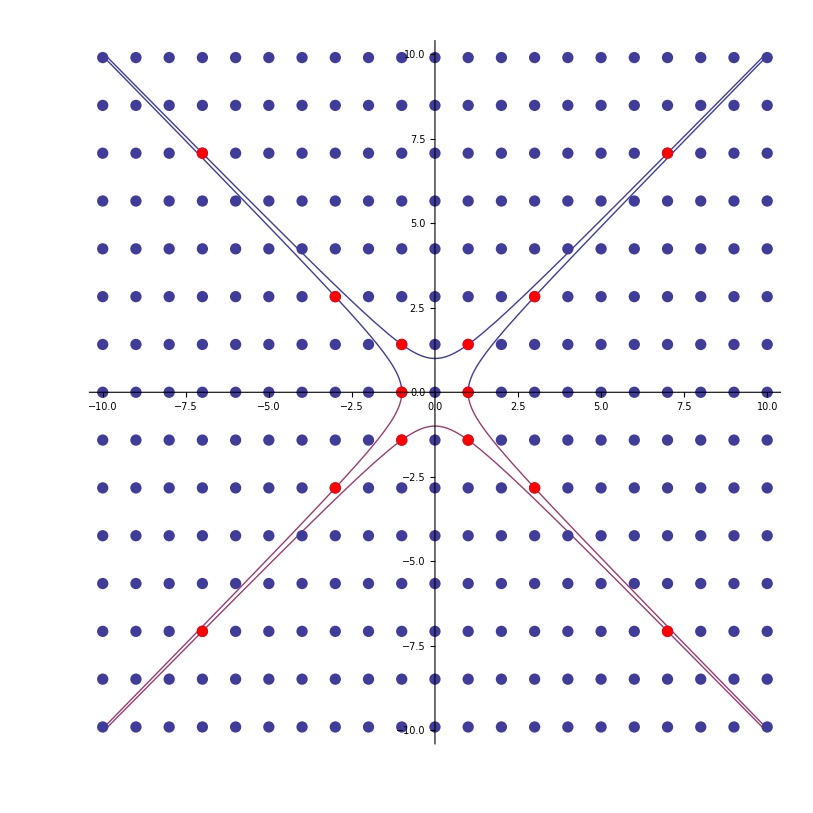

```mathematica
solutions={{1,0},{-1,0},{1,1},{1,-1},{-1,1},{-1,-1},{3,2},{3,-2},{-3,2},{-3,-2},{7,5},{7,-5},{-7,5},{-7,-5}};
solutionsGraphics=Graphics[{PointSize[0.01],Red,Point[{#[[1]],Sqrt[2]#[[2]]}]}&/@solutions];
Show[
Plot[{√(-1+i^2),-√(-1+i^2)},{i,1,10},PlotStyle->Thick],Plot[{√(-1+i^2),-√(-1+i^2)},{i,-10,-1},PlotStyle->Thick],
Plot[{√(1+i^2),-√(1+i^2)},{i,-10,10},PlotStyle->Thick],ListPlot[Partition[Table[{i,Sqrt[2]j},{i,-10,10},{j,-10,10}]//Flatten,2],PlotStyle->PointSize[0.01]],
solutionsGraphics,
PlotRange->{{-10,10},{-10,10}},AxesOrigin->{0,0},AspectRatio->Automatic]
```

```mathematica
{#,(i^2 - 2j^2 )/.{i->#[[1]],j->#[[2]]}}&/@solutions
```

{{{1,0},1},{{-1,0},1},{{1,1},-1},{{1,-1},-1},{{-1,1},-1},{{-1,-1},-1},{{3,2},1},{{3,-2},1},{{-3,2},1},{{-3,-2},1},{{7,5},-1},{{7,-5},-1},{{-7,5},-1},{{-7,-5},-1}}

Euler proved that a regular periodic continued fraction is a quadratic irrational and Lagrange proved the converse that every quadratic irrational is a periodic continued fraction.

```mathematica
x^2 == 2
Solve[%,x]
x+x^2==x+2
x(1+x)==(1+x)+1
x==1+1/(1+x)
Solve[%,x]
```

x^2==2

{{x→-√2},{x→√2}}

x+x^2==2+x

x (1+x)==2+x

x==1+1/(1+x)

{{x→-√2},{x→√2}}

```mathematica
x==1+1/(1+x/.{x->1+1/(1+x)})
x==1+1/(1+x/.{x->1+1/(1+x/.{x->1+1/(1+x)})})
x==1+1/(1+x/.{x->1+1/(1+x/.{x->1+1/(1+x/.{x->1+1/(1+x)})})})
```

x==1+1/(2+1/(1+x))

x==1+1/(2+1/(2+1/(1+x)))

x==1+1/(2+1/(2+1/(2+1/(1+x))))

```mathematica
ContinuedFraction[Sqrt[2]]
```

{1,{2}}

The solutions are given by numerator and denominator of the convergents of the continued fraction of √2

```mathematica
p[0]:=1
q[0]:=1
p[1]:=3
q[1]:=2
p[k_]:=2p[k-1]+p[k-2]
q[k_]:=2q[k-1]+q[k-2]
```

```mathematica
Table[{p[k],q[k]},{k,0,9}]
(#[[1]]^2-2#[[2]]^2)&/@%
```

{{1,1},{3,2},{7,5},{17,12},{41,29},{99,70},{239,169},{577,408},{1393,985},{3363,2378}}

{-1,1,-1,1,-1,1,-1,1,-1,1}

```mathematica
Sqrt[2]==((1+Sqrt[2])p[3]+p[2])/((1+Sqrt[2])q[3]+q[2])
```

True

Which can be written as the integer powers of the silver mean

```mathematica
Table[(1+Sqrt[2])^n//Expand,{n,1,5}]
Table[Expand[(1-Sqrt[2])^n]/Expand[(1+Sqrt[2])^n(1-Sqrt[2])^n],{n,1,5}]
```

{1+√2,3+2 √2,7+5 √2,17+12 √2,41+29 √2}

{-1+√2,3-2 √2,-7+5 √2,17-12 √2,-41+29 √2}

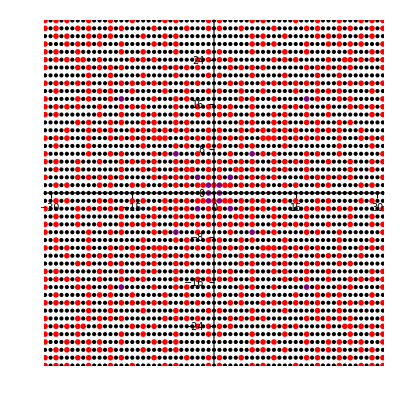

```mathematica
Show[
ListPlot[{0,0},PlotRange->{{-30,30},{-30,30}},AspectRatio->1],
Map[
Which[
PrimeQ[norm[#,2]],
Graphics[{PointSize[0.01],Red,Point[{#[[1]],Sqrt[2]#[[2]]}]}],
Abs[norm[#,2]]==1,
Graphics[{PointSize[0.01],Purple,Point[{#[[1]],Sqrt[2]#[[2]]}]}],
True,
Graphics[{Black,Point[{#[[1]],Sqrt[2]#[[2]]}]}]
]&,
Table[{i,j},{i,-50,50},{j,-50,50}],
{2}],
ImageSize->Scaled[1]
]
```

Finally, let’s look at the case of the real quadratic integers i + j 1/2 (1+√5). Here the units are  (1/2 (1+√5) )^n, n ∈ ℤ where 1/2 (1+√5) is the golden mean.

```mathematica
Mod[5,4]
```

1

```mathematica
Solve[((2 i+j)^2- 5j^2 )/4== 1,j]
Solve[((2 i+j)^2- 5j^2 )/4== -1,j]
```

{{j→1/2 (i-√(-4+5 i^2))},{j→1/2 (i+√(-4+5 i^2))}}

{{j→1/2 (i-√(4+5 i^2))},{j→1/2 (i+√(4+5 i^2))}}

```mathematica
{{1/2 (i+√(-4+5 i^2)),1/2 (i-√(-4+5 i^2))},{1/2 (i+√(4+5 i^2)),1/2 (i-√(4+5 i^2))}}/.{i->-8}
```

{{1/2 (-8+2 √79),1/2 (-8-2 √79)},{5,-13}}

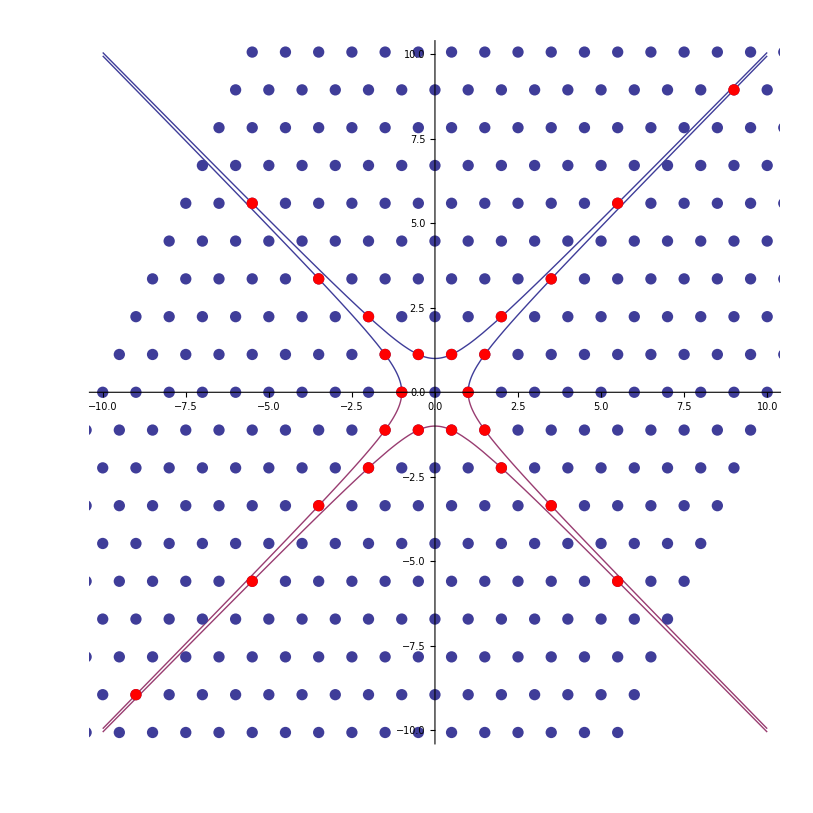

```mathematica
solutions={{-8,-13},{-8,5},{-5,3},{-5,-8},{-3,-5},{-3,2},{-2,1},{-2,-3},{-1,0},{-1,-1},{-1,1},{-1,-2},{0,1},{0,-1},{1,1},{1,0},{1,2},{1,-1},{2,-1},{2,3},{3,-2},{3,5},{5,-3},{5,8},{8,-5},{8,13}};
solutionsGraphics=Graphics[{PointSize[0.01],Red,Point[{#[[1]]+#[[2]]/2,Sqrt[5]#[[2]]/2}]}&/@solutions];
Show[
Plot[{√(-1+i^2),-√(-1+i^2)},{i,1,10},PlotStyle->Thick],Plot[{√(-1+i^2),-√(-1+i^2)},{i,-10,-1},PlotStyle->Thick],
Plot[{√(1+i^2),-√(1+i^2)},{i,-10,10},PlotStyle->Thick],ListPlot[Partition[Table[{i+j/2,Sqrt[5]j/2},{i,-10,10},{j,-10,10}]//Flatten,2],PlotStyle->PointSize[0.01]],
solutionsGraphics,
PlotRange->{{-10,10},{-10,10}},AxesOrigin->{0,0},AspectRatio->Automatic]
```

```mathematica
Table[((1+Sqrt[5])/2)^n//Expand//Simplify,{n,1,5}]
Table[Simplify[Expand[((1-Sqrt[5])/2)^n]/Expand[((1+Sqrt[5])/2)^n((1-Sqrt[5])/2)^n]],{n,1,5}]
```

{1/2 (1+√5),1/2 (3+√5),2+√5,1/2 (7+3 √5),1/2 (11+5 √5)}

{1/2 (-1+√5),1/2 (3-√5),-2+√5,1/2 (7-3 √5),1/2 (-11+5 √5)}

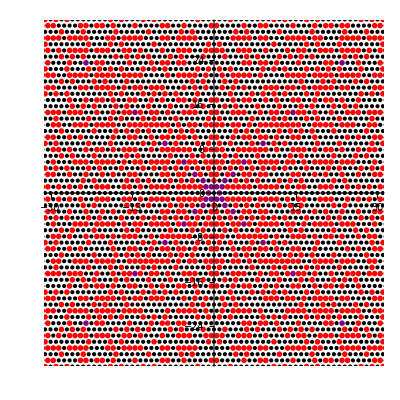

```mathematica
Show[
ListPlot[{0,0},PlotRange->{{-30,30},{-30,30}},AspectRatio->1],
Map[
Which[
PrimeQ[norm[#,5]],
Graphics[{PointSize[0.01],Red,Point[{#[[1]]+#[[2]]/2,Sqrt[5]#[[2]]/2}]}],
Abs[norm[#,5]]==1,
Graphics[{PointSize[0.01],Purple,Point[{#[[1]]+#[[2]]/2,Sqrt[5]#[[2]]/2}]}],
True,
Graphics[{Black,Point[{#[[1]]+#[[2]]/2,Sqrt[5]#[[2]]/2}]}]
]&,
Table[{i,j},{i,-50,50},{j,-50,50}],
{2}],
ImageSize->Scaled[1]
]
```

THE CASE OF THE CAT MAP

In the case that the quadratic equation is the characteristic polynomial of the cat map we have

```mathematica
CharacteristicPolynomial[M,z]
```

1-3 z+z^2

```mathematica
(s^2-4 t) /.{r-> 1, s-> -3, t-> 1}/.{n-> 1}
```

5

The eigenvalues of the Arnold map are quadratic integers in the quadratic field ℚ(ϕ) = {i + ϕ j: (i, j) ∈ℤ^2}.

```mathematica
CharacteristicPolynomial[M,z]
Roots[%==0,z]
Eigenvalues[M]
```

1-3 z+z^2

z==1/2 (3-√5)||z==1/2 (3+√5)

{1/2 (3+√5),1/2 (3-√5)}

```mathematica
(3+Sqrt[5])/2 == (1+ ϕ)/.ϕDef
(3-Sqrt[5])/2== (2-ϕ)/.ϕDef
```

True

True

Let’s find the multiplication rule in ℚ(ϕ).

```mathematica
Clear[i1,i2,j1,j2]
(i1+ϕ j1)(i2+ϕ j2)//Expand
%/.ϕDef//Expand
ϕDef
```

i1 i2+i2 j1 ϕ+i1 j2 ϕ+j1 j2 ϕ^2

i1 i2+(i2 j1)/2+1/2 √5 i2 j1+(i1 j2)/2+1/2 √5 i1 j2+(3 j1 j2)/2+1/2 √5 j1 j2

ϕ→1/2 (1+√5)

```mathematica
i12=i1 i2+ j1 j2
j12=i2 j1+i1 j2+  j1 j2
ReplaceAll[i12+ ϕ j12,ϕDef]==ReplaceAll[i1+ϕ j1,ϕDef]ReplaceAll[i2+ϕ j2,ϕDef]//Expand
```

i1 i2+j1 j2

i2 j1+i1 j2+j1 j2

True

The action of the cat map is equivalent to the multiplication by σ in the quadratic field ℚ(ϕ). The action of the inverse cat map is equivalent to the division by σ.

```mathematica
{i0,j0}={3,7}
{i1,j1}=M.{i0,j0}
multiply[{1,1},{i0,j0}]
```

{3,7}

{10,17}

multiply[{1,1},{3,7}]

```mathematica
{i0,j0}={3,7}
{i1,j1}=invM.{i0,j0}
multiply[{2,-1},{i0,j0}]
```

{3,7}

{-1,4}

multiply[{2,-1},{3,7}]

```mathematica
(i^2 - d j^2)//Expand
(i + j Sqrt[d])( i -  j Sqrt[d])//Expand
```

i^2-d j^2

i^2-d j^2

```mathematica
((2 i + j)^2 - d j^2)/4 //Expand
(i + j (1+Sqrt[d])/2)(i + j (1-Sqrt[d])/2)//Expand
Solve[((2 i + j)^2 - d j^2)/4==(i + j (1+Sqrt[d])/2)( i + j x),x]
```

i^2+i j+j^2/4-(d j^2)/4

i^2+i j+j^2/4-(d j^2)/4

{{x→1/2 (1-√d)}}

```mathematica
(1+Sqrt[d])(1-Sqrt[d])/4//Expand
```

1/4-d/4

```mathematica
(1+Sqrt[5])(1-Sqrt[5])/4//Expand
```

-1

```mathematica
norm[{i,j}]
norm[{1,1}]
norm[{2,-1}]
```

norm[{i,j}]

norm[{1,1}]

norm[{2,-1}]

```mathematica
norm[{i,j}]norm[{k,l}]//Expand
norm[multiply[{i,j},{k,l}]]//Expand
```

norm[{i,j}] norm[{k,l}]

norm[multiply[{i,j},{k,l}]]

```mathematica
norm[{4,3}]
```

norm[{4,3}]

Let’s consider a principal ideal of ℚ(ϕ) generated by n ∈ ℕ. Let’s call it ⟨n⟩. It is defined as ⟨n⟩ = {n i + ϕ n j: n ∈ ℕ, (i, j) ∈ℤ^2}

⟨n⟩ is invariant with respect to the multiplication by σ.

```mathematica
multiply[{1,1},{i n,j n}]
multiply[{2,-1},{i n,j n}]
```

multiply[{1,1},{i n,j n}]

multiply[{2,-1},{i n,j n}]

The factors of ⟨n⟩ correspond to the invariant sublattices on the torus.

⟨2⟩ is a prime ideal (inert ideal)

```mathematica
multiply[{2 i,2  j},{k, l}]
```

multiply[{2 i,2 j},{k,l}]

⟨3⟩ is a prime ideal (inert ideal)

```mathematica
multiply[{3  i,3  j},{k, l}]
```

multiply[{3 i,3 j},{k,l}]

⟨4⟩ = ⟨2⟩⟨2⟩ (ramified ideal)

```mathematica
multiply[{2 i,2 j},{2 k, 2 l}]
```

multiply[{2 i,2 j},{2 k,2 l}]

⟨5⟩ is a prime ideal (inert ideal)

```mathematica
multiply[{5  i,5  j},{k, l}]
```

multiply[{5 i,5 j},{k,l}]

⟨6⟩ = ⟨2⟩⟨3⟩ (split ideal)

```mathematica
multiply[{2 i,2 j},{3 k, 3 l}]
```

multiply[{2 i,2 j},{3 k,3 l}]

⟨7⟩ is a prime ideal (inert ideal)

```mathematica
multiply[{7  i,7  j},{k, l}]
```

multiply[{7 i,7 j},{k,l}]

⟨8⟩ = ⟨2⟩⟨2⟩⟨2⟩ (ramified ideal)

```mathematica
multiply[multiply[{2 i,2 j},{2 k, 2 l}],{2 s, 2 t}]//Expand
```

multiply[multiply[{2 i,2 j},{2 k,2 l}],{2 s,2 t}]

⟨9⟩ = ⟨3⟩⟨3⟩ (ramified ideal)

```mathematica
multiply[{3 i,3 j},{3 k, 3l}]
```

multiply[{3 i,3 j},{3 k,3 l}]

⟨10⟩ = ⟨2⟩⟨5⟩ (split ideal)

```mathematica
multiply[{2 i,2 j},{5 k, 5 l}]
```

multiply[{2 i,2 j},{5 k,5 l}]

### The space of measures on the rational numbers

#### Definitions

Representation of the Transfer operator on the space of measures with support on ℚ^2∩[0,1[^2

These measures are spanned by 2 dimensional comb distributions on the grids (i/n,j/n).

The representation is equivalent to a permutation of the points of the grid. The cycles of the permutation are the periodic orbits.

This is a unitary representation. An eigenvector is simply a complex vector corresponding to a cycle of the permutation that is multiplied by a phase under the action of the operator. All eigenvalues lie on the unit circle together with their complex conjugates.

```mathematica
ind[n_,{i_,j_}] := j n + i+1
```

```mathematica
rules[cycle_]:=Thread[DirectedEdge[cycle,RotateLeft[cycle]]]
```

```mathematica
PerronFrobenius := Module[{
L = SparseArray[{{1,1}->0}],
permutation=Table[0,{i,n^2}]},
map=Flatten[Table[{{i,j},n invF[{i/n,j/n}]},{i,0,n-1},{j,0,n-1}],1];
indices=Map[ind[n,#]&,map,{2}];
L=SparseArray[(#-> 1)&/@indices];
(permutation[[#[[2]]]]=#[[1]])&/@indices;
{L,permutation}
]
```

```mathematica
Koopman := Module[{
K = SparseArray[{{1,1}->0}]},
map=Flatten[Table[{{i,j},n F[{i/n,j/n}]},{i,0,n-1},{j,0,n-1}],1];
indices=Map[ind[n,#]&,map,{2}];
K=SparseArray[(#-> 1)&/@indices];
K
]
```

```mathematica
orbitPlot[n_Integer,{x_,y_}]:=
ListPlot[NestList[F,{x,y},n], Frame->True, ImageSize->Scaled[0.25],AspectRatio->Automatic, PlotRange->{{0,1},{0,1}}, PlotStyle->PointSize[0.05]]
```

```mathematica
color="BlueGreenYellow";
eigenstatePlot[n_Integer,ρ_,orbitPlot_]:=
Module[{ψ=Partition[ρ//Chop,n]//Reverse},
GraphicsGrid[{{ArrayPlot[Re[ψ],ImageSize->Scaled[0.25],ColorFunction->color,Mesh->True],ArrayPlot[Im[ψ],ImageSize->Scaled[0.25],ColorFunction->color,Mesh->True],orbitPlot}}]
]
projectorPlot[P_]:=
ArrayPlot[P//Chop,Mesh->True,ColorFunction->color]
```

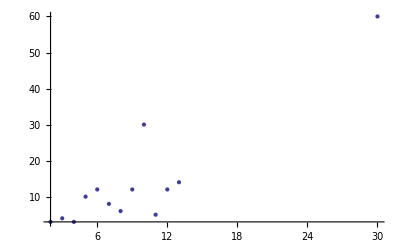

```mathematica
periodicOrbitSpectrum = {
{2,{{1,1},{1,3}}},
{3,{{1,1},{2,4}}},
{4,{{1,1},{5,3}}},
{5,{{1,1},{2,2},{2,10}}},
{6,{{1,1},{1,3},{2,4},{2,12}}},
{7,{{1,1},{6,8}}},
{8,{{1,1},{5,3},{8,6}}},
{9,{{1,1},{2,4},{6,12}}},
{10,{{1,1},{2,2},{1,3},{2,6},{2,10},{2,30}}},
{11,{{1,1},{24,5}}},
{12,{{1,1},{5,3},{2,4},{10,12}}},
{13,{{1,1},{12,14}}},
{30,{{1,1},{2,2},{1,3},{10,4},{2,6},{2,10},{10,12},{8,20},{2,30},{8,60}}}
};
cyclotomy = {
{2,3},
{3,4},
{4,3},
{5,10},
{6,12},
{7,8},
{8,6},
{9,12},
{10,30},
{11,5},
{12,12},
{13,14},
{30,60}
};
ListPlot[cyclotomy,PlotRange->All]
```

```mathematica
primeFactorization:={#[[1]],FactorInteger[#[[1]]]}&
numberOfPeriodicOrbits := {#[[1]],Sum[#[[2,i,1]],{i,Length[#[[2]]]}]}&
alpha := {#[[1]],LCM@@(#[[2]]&/@#[[2]])}&
```

```mathematica
periodicOrbitSpectrum[[3,2,1]]
numberOfPeriodicOrbits/@periodicOrbitSpectrum
alpha/@periodicOrbitSpectrum
primeFactorization/@periodicOrbitSpectrum
```

{1,1}

{{2,2},{3,3},{4,6},{5,5},{6,6},{7,7},{8,14},{9,9},{10,10},{11,25},{12,18},{13,13},{30,46}}

{{2,3},{3,4},{4,3},{5,10},{6,12},{7,8},{8,6},{9,12},{10,30},{11,5},{12,12},{13,14},{30,60}}

{{2,{{2,1}}},{3,{{3,1}}},{4,{{2,2}}},{5,{{5,1}}},{6,{{2,1},{3,1}}},{7,{{7,1}}},{8,{{2,3}}},{9,{{3,2}}},{10,{{2,1},{5,1}}},{11,{{11,1}}},{12,{{2,2},{3,1}}},{13,{{13,1}}},{30,{{2,1},{3,1},{5,1}}}}

#### n=2

```mathematica
n=2
n^2
{L,permutation}=PerronFrobenius;
K=Koopman;
{λ,ρ}=Eigensystem[L//N];
{κ,χ}=Eigensystem[K//N];
```

2

4

The grid of 2x2=4 points has the fixed point (0,0) and can only fit another periodic orbit of period 3.

```mathematica
PermutationCycles[permutation]
Flatten[rules/@First[%]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.6]
AdjacencyGraph[L,GraphStyle->"VintageDiagram"]
```

Cycles[{{2,4,3}}]

{2->4,4->3,3->2}

-Graphics-

-Graphics-

```mathematica
ArrayPlot[L,Mesh->True]
ArrayPlot[K,Mesh->True]
K== Transpose[L]
```

-Graphics-

-Graphics-

True

The eigenvalues of the operator must span the periods 1 and 3 of the only two periodic orbits in the grid.

```mathematica
CharacteristicPolynomial[L,z]
Factor[%]
```

1-z-z^3+z^4

(-1+z)^2 (1+z+z^2)

```mathematica
Roots[(z-1)^2==0,z]
Roots[z^2+z+1==0,z]
```

z==1||z==1

z==-(-1)^(1/3)||z==(-1)^(2/3)

The eigenvalues lie on the unit circle because the operator is unitary.

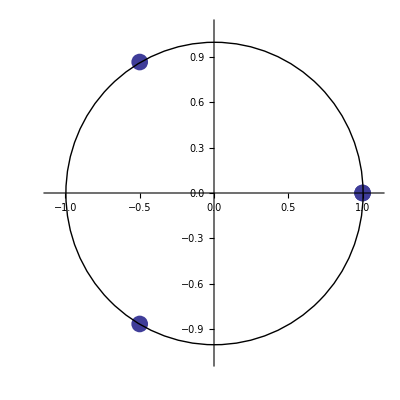

```mathematica
Show[ListPlot[{Re[#],Im[#]}&/@λ//N,AspectRatio->Automatic,ImageSize->Scaled[0.5],PlotRange->{{-1.1,1.1},{-1.1,1.1}},PlotStyle->PointSize[0.03]],Graphics[Circle[{0,0},1]]]
```

The eigenvalues of the Perron and of the Koopman operators are the same.

```mathematica
λ
```

{-0.5+0.866025 ⅈ,-0.5-0.866025 ⅈ,1.,1.}

```mathematica
κ==λ
```

True

The eigendensities of the Transfer operator are orthogonal to the eigendensities of the Koopman operator.

{{-0.5-0.866025 ⅈ,0,0,0},{0,-0.5+0.866025 ⅈ,0,0},{0,0,1.,0},{0,0,0,1.}}

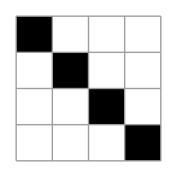

```mathematica
Table[χ[[k]].ρ[[l]],{k,n^2},{l,n^2}]//Chop
ArrayPlot[%,Mesh->True]
```

```mathematica
Do[χ[[k]]=χ[[k]]/χ[[k]].ρ[[k]],{k,n^2}]//Chop
```

After normalization the eigendensities of the Koopman operator are adjoint to the eigendensities if the Perron operator.

```mathematica
Do[Print[Chop[χ[[k]]]==Conjugate[ρ[[k]]]],{k,n^2}]
```

True

True

True

«1 more identical outputs»

The eigendensities of either the Perron or the Koopman operator are concentrated on the periodic orbits of the cat map.

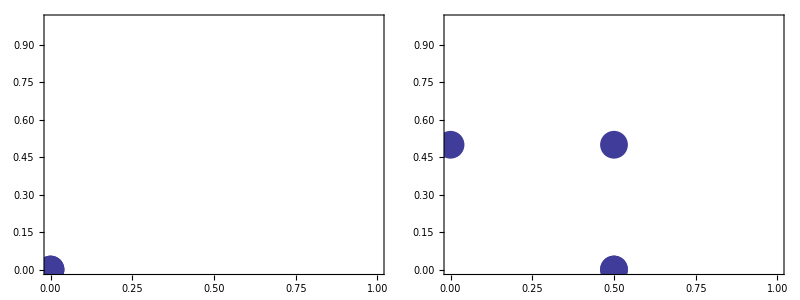

```mathematica
o0=orbitPlot[1,{0,0}];
o1=orbitPlot[3,{1/2,0}];
Grid[{{o0,o1}}]
```

1.

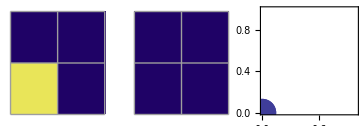

1.

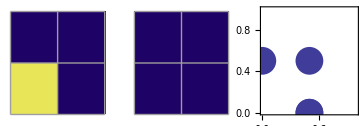

```mathematica
l=3;
λ[[l]]
eigenstatePlot[n,ρ[[l]],o0]
l=4;
λ[[l]]
eigenstatePlot[n,ρ[[l]],o1]
```

-0.5+0.866025 ⅈ

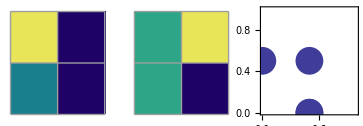

-0.5-0.866025 ⅈ

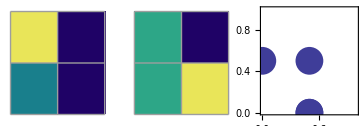

```mathematica
l=1;
λ[[l]]
eigenstatePlot[n,ρ[[l]],o1]
l=2;
λ[[l]]
eigenstatePlot[n,ρ[[l]],o1]
```

The eigendensities of the Koopman operator are adjoint to the eigendensities of the Perron operator. By tensor product they form a basis of projection operators.

```mathematica
P = Table[Table[ρ[[k,i]]*χ[[k,j]],{i,n^2},{j,n^2}],{k,n^2}];
```

1.

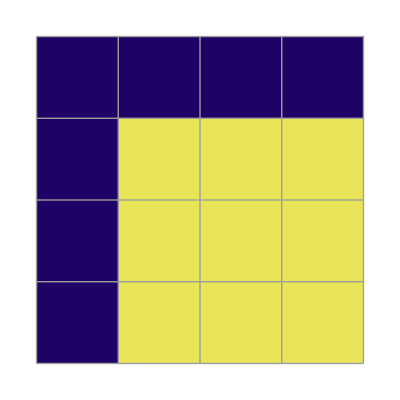

1.

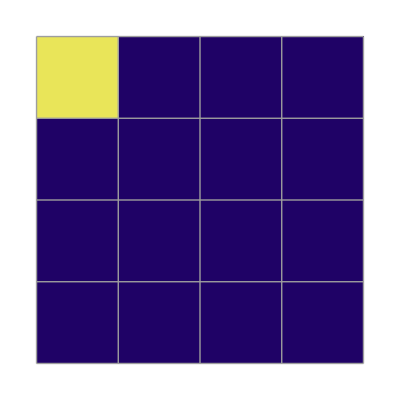

-0.5+0.866025 ⅈ

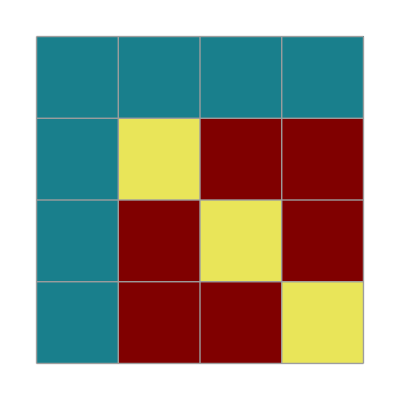

```mathematica
λ[[4]]
projectorPlot[P[[4]]]
λ[[3]]
projectorPlot[P[[3]]]
λ[[1]]
projectorPlot[P[[1]]]
```

The spectral decomposition of the Perron operator.

```mathematica
LL=Sum[λ[[k]]P[[k]],{k,n^2}];
```

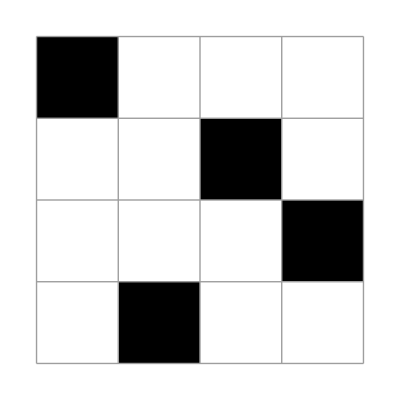

-Graphics-

True

```mathematica
ArrayPlot[LL,Mesh->True]
ArrayPlot[L,Mesh->True]
Chop[LL]==L
```

#### n=3

```mathematica
n=3
n^2
{L,permutation}=PerronFrobenius;
K=Koopman;
{λ,ρ}=Eigensystem[L//N];
{κ,χ}=Eigensystem[K//N];
```

3

9

The grid of 3x3=9 points has the fixed point (0,0) and 2 other periodic orbits of period 4.

```mathematica
PermutationCycles[permutation]
Flatten[rules/@First[%]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.6]
AdjacencyGraph[L,GraphStyle->"VintageDiagram"]
```

Cycles[{{2,5,3,9},{4,8,7,6}}]

{2->5,5->3,3->9,9->2,4->8,8->7,7->6,6->4}

-Graphics-

-Graphics-

```mathematica
ArrayPlot[L,Mesh->True]
ArrayPlot[K,Mesh->True]
K== Transpose[L]
```

-Graphics-

-Graphics-

True

We should expect the eigenvalues to be 1 and the 4th roots of unity with multiplicity 2.

```mathematica
CharacteristicPolynomial[L,z]
Factor[%]
```

1-z-2 z^4+2 z^5+z^8-z^9

-(-1+z)^3 (1+z)^2 (1+z^2)^2

```mathematica
Roots[(z-1)^3==0,z]
Roots[(z+1)^2==0,z]
Roots[(z^2+1)^2==0,z]
```

z==1||z==1||z==1

z==-1||z==-1

z==ⅈ||z==ⅈ||z==-ⅈ||z==-ⅈ

{{1.,0,0,0,0,0,0,0,0},{0,-1.,0,0,0,0,0,0,0},{0,0,1.,0,0,0,0,0,0},{0,0,0,1.,0,0,0,0,0},{0,0,0,0,-1.,0,0,0,0},{0,0,0,0,0,-1.,0,0,0},{0,0,0,0,0,0,1.,0,0},{0,0,0,0,0,0,0,-1.,0},{0,0,0,0,0,0,0,0,1.}}

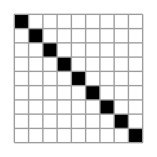

```mathematica
Table[χ[[k]].ρ[[l]],{k,n^2},{l,n^2}]//Chop
ArrayPlot[%,Mesh->True]
```

```mathematica
Do[χ[[k]]=χ[[k]]/χ[[k]].ρ[[k]],{k,n^2}]//Chop
```

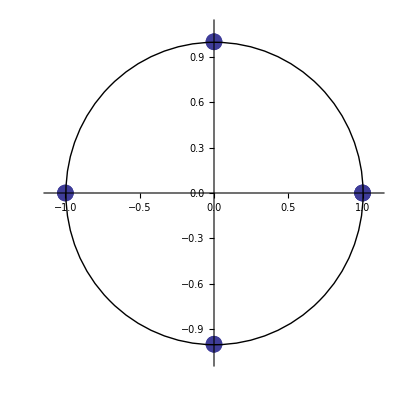

```mathematica
Show[ListPlot[{Re[#],Im[#]}&/@λ//N,AspectRatio->Automatic,ImageSize->Scaled[0.5],PlotRange->{{-1.1,1.1},{-1.1,1.1}},PlotStyle->PointSize[0.03]],Graphics[Circle[{0,0},1]]]
```

```mathematica
λ[[1;;2]]//Chop
λ[[3;;5]]//Chop
λ[[6;;9]]//Chop
```

{-1.,-1.}

{1.,1.,1.}

{0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}

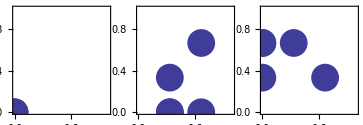

```mathematica
o0=orbitPlot[1,{0,0}];
o1=orbitPlot[4,{1/3,0}];
o2=orbitPlot[4,S[{1/3,0}]];
GraphicsGrid[{{o0,o1,o2}}]
```

```mathematica
P = Table[Table[ρ[[k,i]]*χ[[k,j]],{i,n^2},{j,n^2}],{k,n^2}];
```

3

1.

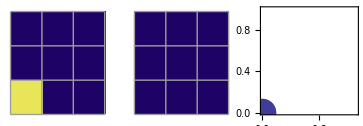

4

1.

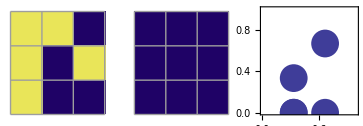

5

1.

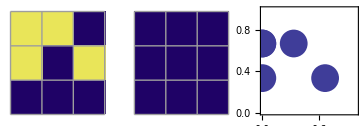

```mathematica
l=3
λ[[l]]
eigenstatePlot[n,ρ[[l]],o0]
l=4
λ[[l]]
eigenstatePlot[n,ρ[[l]],o1]
l=5
λ[[l]]
eigenstatePlot[n,ρ[[l]],o2]
```

{1.,1.,1.}

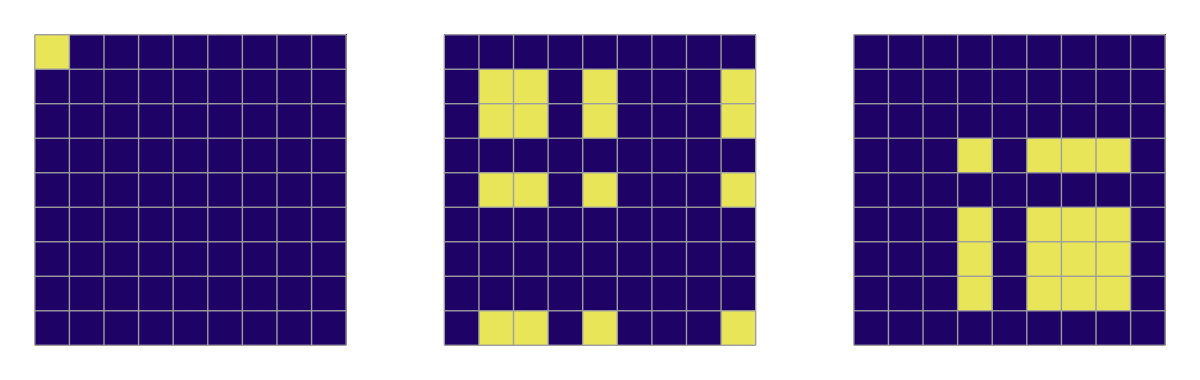

```mathematica
{λ[[3]],λ[[4]],λ[[5]]}
GraphicsGrid[{{projectorPlot[P[[3]]],
projectorPlot[P[[4]]],
projectorPlot[P[[5]]]}}]
```

1

-1.

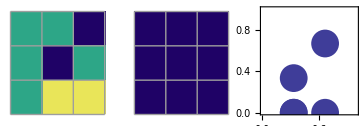

2

-1.

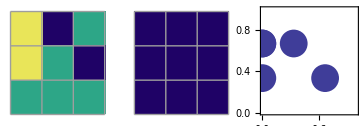

```mathematica
l=1
λ[[l]]
eigenstatePlot[n,ρ[[l]],o1]
l=2
λ[[l]]
eigenstatePlot[n,ρ[[l]],o2]
```

{-1.,-1.}

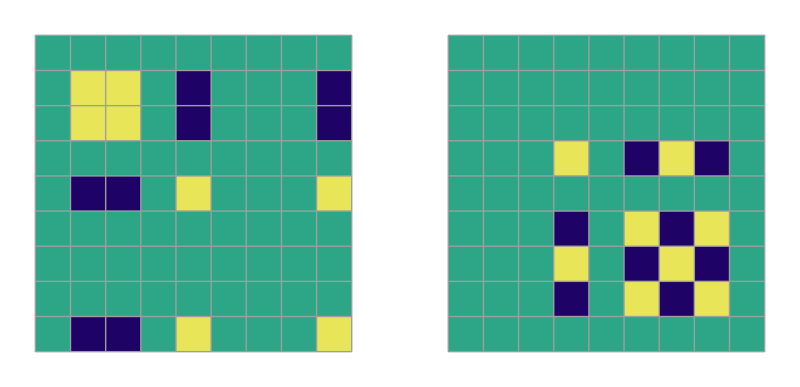

```mathematica
{λ[[1]],λ[[2]]}
GraphicsGrid[{{projectorPlot[P[[1]]],
projectorPlot[P[[2]]]}}]
```

6

0.+1. ⅈ

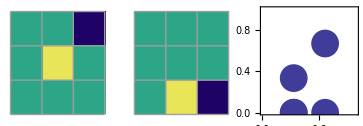

7

0.+1. ⅈ

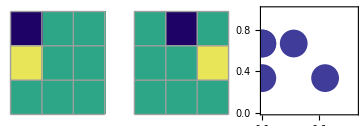

8

0.-1. ⅈ

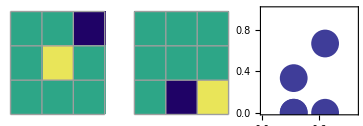

9

0.-1. ⅈ

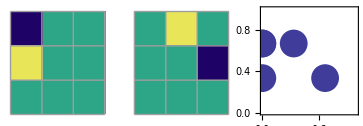

```mathematica
l=6
λ[[l]]//Chop
eigenstatePlot[n,ρ[[l]],o1]
l=7
λ[[l]]//Chop
eigenstatePlot[n,ρ[[l]],o2]
l=8
λ[[l]]//Chop
eigenstatePlot[n,ρ[[l]],o1]
l=9
λ[[l]]//Chop
eigenstatePlot[n,ρ[[l]],o2]
```

{0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}

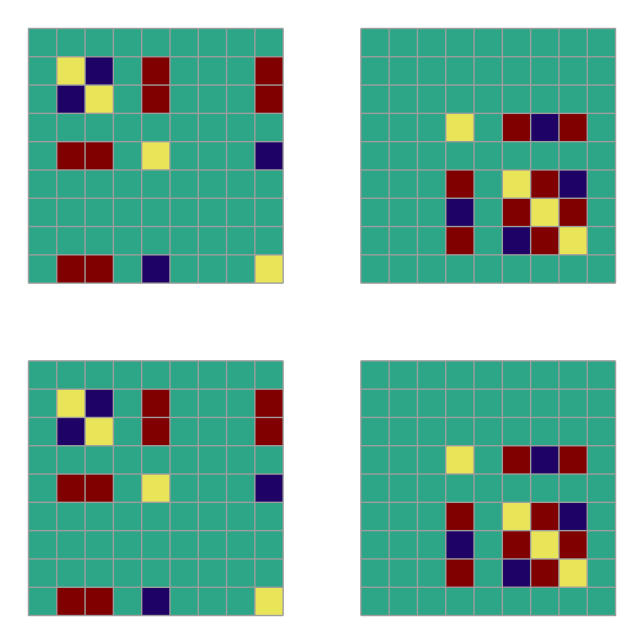

```mathematica
{λ[[6]],λ[[7]],λ[[8]],λ[[9]]}//Chop
GraphicsGrid[{{projectorPlot[P[[6]]],projectorPlot[P[[7]]]},{projectorPlot[P[[8]]],projectorPlot[P[[9]]]}}]
```

```mathematica
LL=Sum[λ[[k]]P[[k]],{k,n^2}];
```

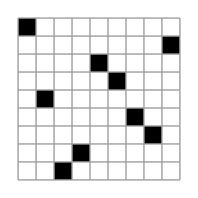

-Graphics-

True

```mathematica
ArrayPlot[LL,Mesh->True]
ArrayPlot[L,Mesh->True]
Chop[LL]==L
```

#### n=4

The grid of 4x4=16 points has the fixed point (0,0) and 5 other periodic orbits of period 3 (including the one found for n=2).

```mathematica
n=4
n^2
```

4

16

```mathematica
{L,permutation}=Perron;
K=Koopman;
{λ,ρ}=Eigensystem[L//N];
{κ,χ}=Eigensystem[K//N];
```

Set::shape: Lists {L, permutation} and Perron are not the same shape.

```mathematica
PermutationCycles[permutation]
Flatten[rules/@First[%]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.6]
AdjacencyGraph[L,GraphStyle->"VintageDiagram"]
```

Cycles[{{2,5,3,9},{4,8,7,6}}]

{2->5,5->3,3->9,9->2,4->8,8->7,7->6,6->4}

-Graphics-

-Graphics-

```mathematica
ArrayPlot[L,Mesh->True]
ArrayPlot[K,Mesh->True]
K== Transpose[L]
```

-Graphics-

-Graphics-

False

The eigenvalues have to be 1 and the 3rd roots of 1 with multiplicity 5.

```mathematica
CharacteristicPolynomial[L,z]
Factor[%]
```

1-z-2 z^4+2 z^5+z^8-z^9

-(-1+z)^3 (1+z)^2 (1+z^2)^2

```mathematica
Roots[(z-1)^6==0,z]
Roots[(z^2+z+1)^5==0,z]
```

z==1||z==1||z==1||z==1||z==1||z==1

z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 - 0.5\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 + 0.5\ ⅈ} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 - 0.5\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 + 0.5\ ⅈ} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 - 0.5\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 + 0.5\ ⅈ} and {1., 0., 0., 0., 0., 0., 0., 0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

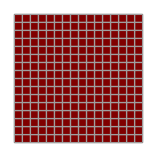

```mathematica
Table[χ[[k]].ρ[[l]],{k,n^2},{l,n^2}]//Chop;
ArrayPlot[%,Mesh->True]
```

```mathematica
p={0,1,-1,0,0,0,1,-1,0,0,0,0,1,-1,0,0};
λ = Table[λ[[k+p[[k]]]],{k,n^2}];
ρ= Table[ρ[[k+p[[k]]]],{k,n^2}];
Do[χ[[k]]=χ[[k]]/χ[[k]].ρ[[k]],{k,n^2}]//Chop
```

Part::partw: Part 10 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

Part::partw: Part 11 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

Part::partw: Part 12 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 - 0.5\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 + 0.5\ ⅈ} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 + 0.5\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 - 0.5\ ⅈ, 0.  + 0.\ ⅈ} and {1., 0., 0., 0., 0., 0., 0., 0., 0.} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 - 0.5\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 + 0.5\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

False

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ/{0.  + 0.\ ⅈ, « 14 », -0.288675 + 0.5\ ⅈ} . {« 1 »}, 0.  + 0.\ ⅈ, « 6 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675  - 0.5\ ⅈ/{0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 - 0.5\ ⅈ, « 3 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 + 0.5\ ⅈ} . {« 1 »}} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ/{0.  + 0.\ ⅈ, « 14 », -0.288675 + 0.5\ ⅈ} . {« 1 »}, 0.  + 0.\ ⅈ, « 6 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675  - 0.5\ ⅈ/{0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 - 0.5\ ⅈ, « 3 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 + 0.5\ ⅈ} . {« 1 »}} and {1., 0., 0., 0., 0., 0., 0., 0., 0.} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ/{0.  + 0.\ ⅈ, « 14 », -0.288675 + 0.5\ ⅈ} . {« 1 »}, 0.  + 0.\ ⅈ, « 6 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675  - 0.5\ ⅈ/{0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 - 0.5\ ⅈ, « 3 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 + 0.5\ ⅈ} . {« 1 »}} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of « 1 » does not exist.

Part::partw: Part 11 of « 1 » does not exist.

Part::partw: Part 12 of « 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

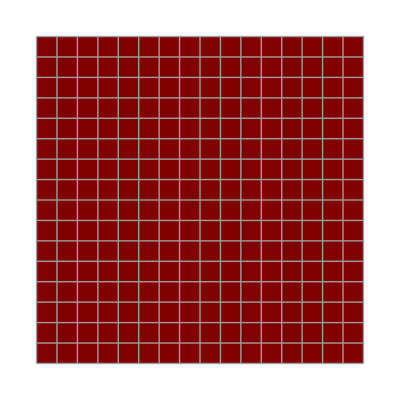

```mathematica
λ==κ
Table[χ[[k]].ρ[[l]],{k,n^2},{l,n^2}]//Chop;
ArrayPlot[%,Mesh->True]
```

```mathematica
Show[ListPlot[{Re[#],Im[#]}&/@λ//N,AspectRatio->Automatic,ImageSize->Scaled[0.5],PlotStyle->PointSize[0.03],PlotRange->{{-1.1,1.1},{-1.1,1.1}}],Graphics[Circle[{0,0},1]]]
```

-Graphics-

```mathematica
λ[[1;;5]]
λ[[6;;10]]
λ[[11;;16]]
```

{-1.,1.,-1.,1.,1.}

{5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦10⟧}

Part::partw: Part 10 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

Part::partw: Part 11 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

Part::partw: Part 12 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦11⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦12⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦14⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦13⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦15⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦16⟧}

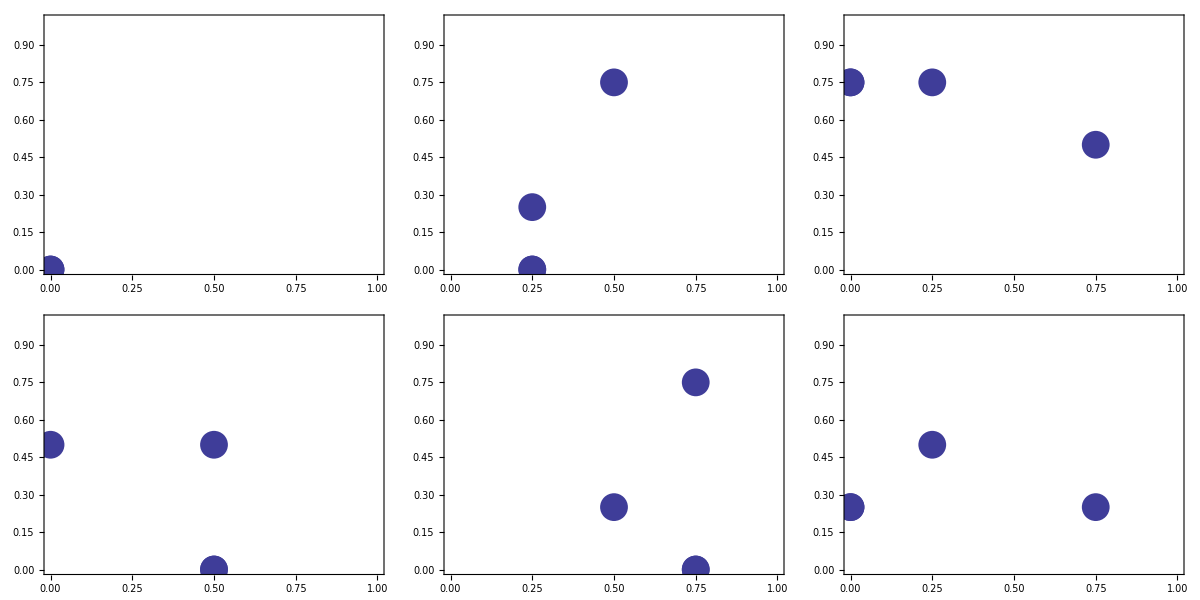

```mathematica
o0=orbitPlot[1,{0,0}];
o1=orbitPlot[3,{1/4,0}];
o2=orbitPlot[3,S[{1/4,0}]];
o3=orbitPlot[3,{2/4,0}];
o4=orbitPlot[3,{3/4,0}];
o5=orbitPlot[3,S[{3/4,0}]];
Grid[{{o0,o1,o2},{o3,o4,o5}}]
```

```mathematica
P = Table[Table[ρ[[k,i]]*χ[[k,j]],{i,n^2},{j,n^2}],{k,n^2}];
```

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

11

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦11⟧

Part::partw: Part 11 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

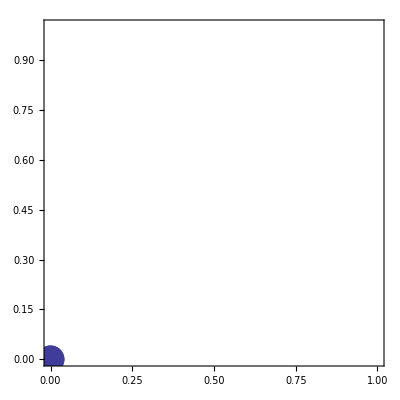

12

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦12⟧

Part::partw: Part 12 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

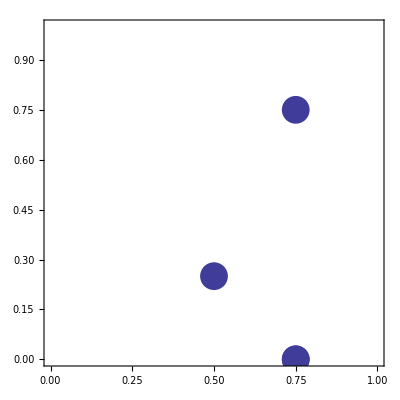

13

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦14⟧

Part::partw: Part 14 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

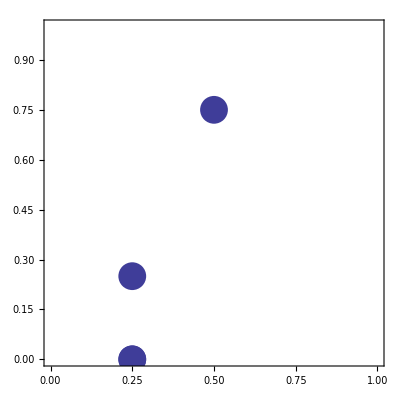

14

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦13⟧

Part::partw: Part 13 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

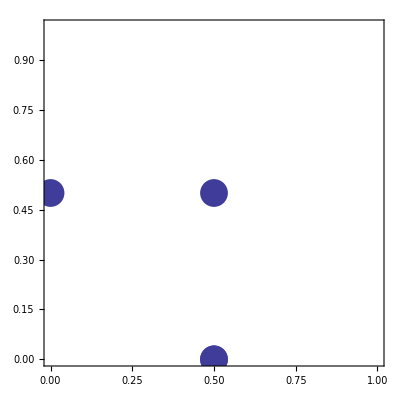

15

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦15⟧

Part::partw: Part 15 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

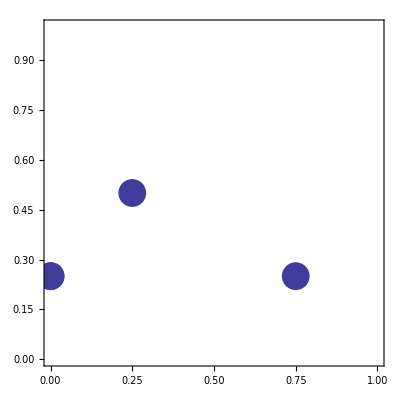

16

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦16⟧

Part::partw: Part 16 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

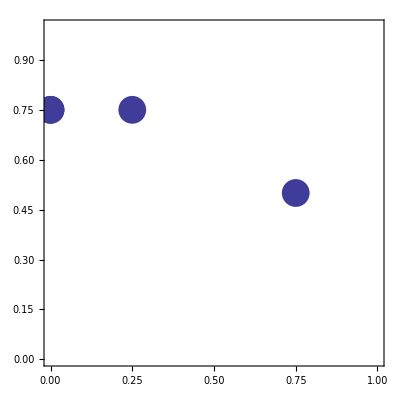

```mathematica
l=11
λ[[l]]
eigenstatePlot[n,ρ[[l]],o0]
l=12
λ[[l]]
eigenstatePlot[n,ρ[[l]],o4]
l=13
λ[[l]]
eigenstatePlot[n,ρ[[l]],o1]
l=14
λ[[l]]
eigenstatePlot[n,ρ[[l]],o3]
l=15
λ[[l]]
eigenstatePlot[n,ρ[[l]],o5]
l=16
λ[[l]]
eigenstatePlot[n,ρ[[l]],o2]
```

{{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦11⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦12⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦14⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦13⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦15⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦16⟧}

Part::partw: Part 11 of « 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

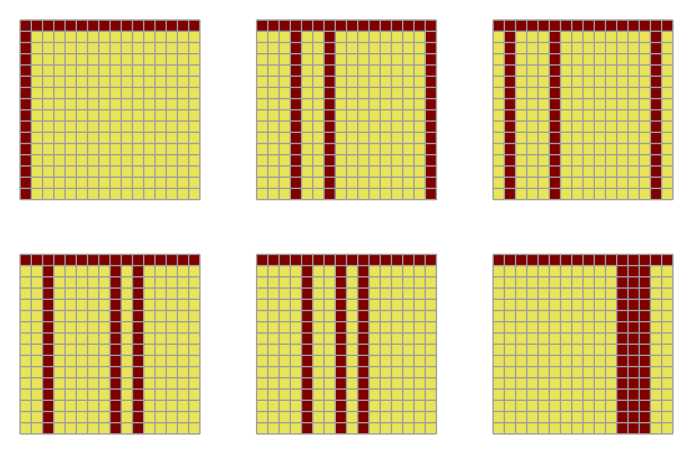

```mathematica
{λ[[11]],λ[[12]],λ[[13]],λ[[14]],λ[[15]],λ[[16]]}
GraphicsGrid[{{projectorPlot[P[[11]]],
projectorPlot[P[[12]]],
projectorPlot[P[[13]]]},{projectorPlot[P[[14]]],
projectorPlot[P[[15]]],
projectorPlot[P[[16]]]}}]
```

1

-1.

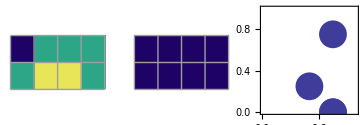

2

1.

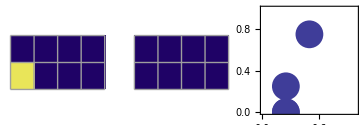

3

-1.

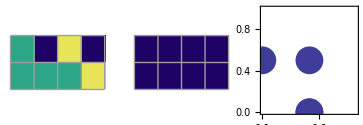

4

1.

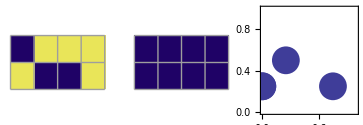

5

1.

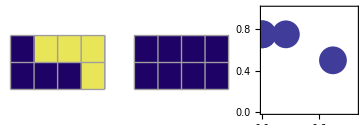

```mathematica
l=1
λ[[l]]
eigenstatePlot[n,ρ[[l]],o4]
l=2
λ[[l]]
eigenstatePlot[n,ρ[[l]],o1]
l=3
λ[[l]]
eigenstatePlot[n,ρ[[l]],o3]
l=4
λ[[l]]
eigenstatePlot[n,ρ[[l]],o5]
l=5
λ[[l]]
eigenstatePlot[n,ρ[[l]],o2]
```

{-1.,1.,-1.,1.,1.}

Dot::dotsh: Tensors {0, 0, 0, 0.57735, 0, 0, -0.288675 - 0.5\ ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, -0.288675 + 0.5\ ⅈ} and {0, 0.5, 0.5, 0, -0.5, 0, 0, 0, -0.5} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of « 1 » does not exist.

Part::partw: Part 11 of « 1 » does not exist.

Part::partw: Part 12 of « 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

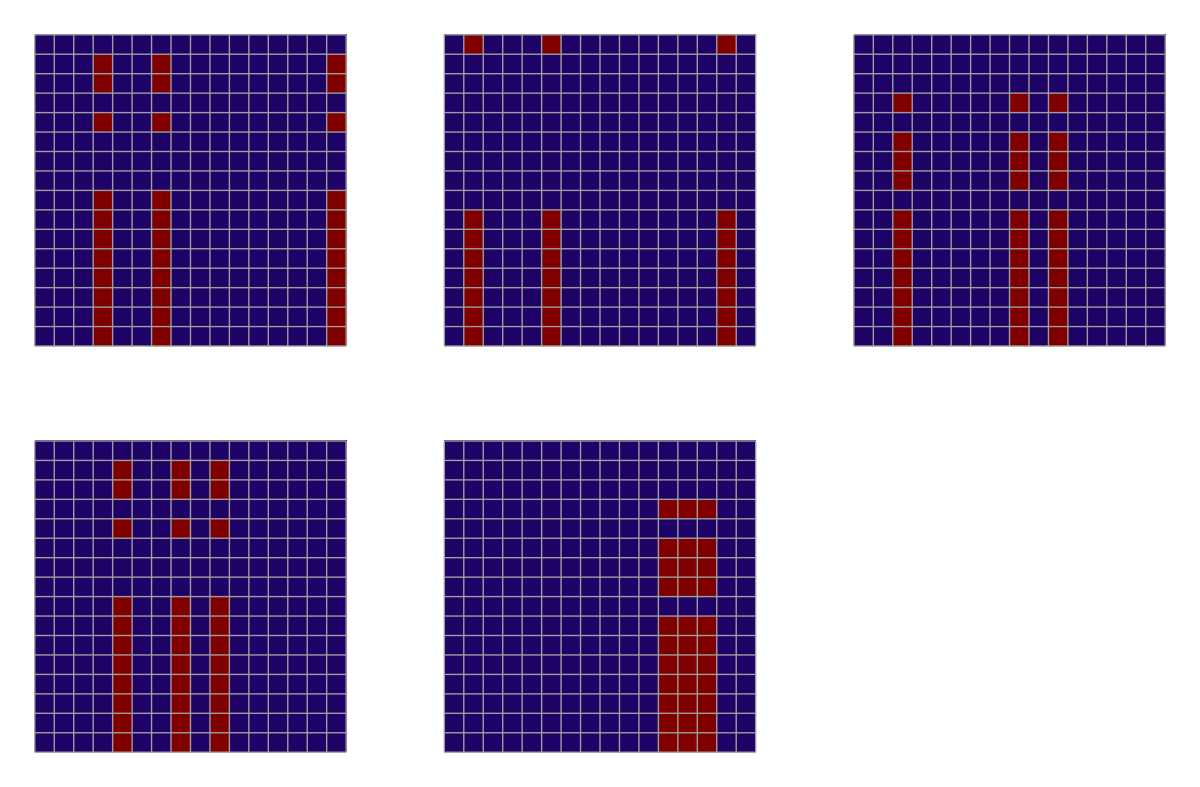

```mathematica
{λ[[1]],λ[[2]],λ[[3]],λ[[4]],λ[[5]]}
GraphicsGrid[{{projectorPlot[P[[1]]],
projectorPlot[P[[2]]],
projectorPlot[P[[3]]]},{projectorPlot[P[[4]]],
projectorPlot[P[[5]]]}}]
```

```mathematica
LL=Sum[λ[[k]]P[[k]],{k,n^2}];
```

```mathematica
ArrayPlot[LL,Mesh->True]
ArrayPlot[L,Mesh->True]
Chop[LL]==L
```

-Graphics-

-Graphics-

Part::partw: Part 11 of « 1 » does not exist.

Part::partw: Part 11 of {-1., -1., 1., 1., 1., 0.  + 1.\ ⅈ, 0.  + 1.\ ⅈ, 0.  - 1.\ ⅈ, 0.  - 1.\ ⅈ} does not exist.

Part::partw: Part 11 of « 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Dot::dotsh: Tensors {0, 0.57735, 0, 0, 0, -0.288675 + 0.5\ ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, -0.288675 - 0.5\ ⅈ, 0} and {1., 0, 0, 0, 0, 0, 0, 0, 0} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

False

#### n=5

```mathematica
n=5
n^2
```

5

25

```mathematica
{L,permutation}=Perron;
K=Koopman;
{λ,ρ}=Eigensystem[L//N];
{κ,χ}=Eigensystem[K//N];
```

Set::shape: Lists {L, permutation} and Perron are not the same shape.

```mathematica
PermutationCycles[permutation]
Flatten[rules/@First[%]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.6]
```

Cycles[{{2,5,3,9},{4,8,7,6}}]

{2->5,5->3,3->9,9->2,4->8,8->7,7->6,6->4}

-Graphics-

```mathematica
ArrayPlot[L,Mesh->True]
ArrayPlot[K,Mesh->True]
K== Transpose[L]
```

-Graphics-

-Graphics-

False

```mathematica
CharacteristicPolynomial[L,z]
Factor[%]
```

1-z-2 z^4+2 z^5+z^8-z^9

-(-1+z)^3 (1+z)^2 (1+z^2)^2

```mathematica
Roots[(z-1)^5==0,z]
Roots[(z+1)^4==0,z]
Roots[(z^4-z^3+z^2-z+1)^2==0,z]
Roots[(z^4+z^3+z^2+z+1)^2==0,z]
```

z==1||z==1||z==1||z==1||z==1

z==-1||z==-1||z==-1||z==-1

z==(-1)^(1/5)||z==(-1)^(1/5)||z==-(-1)^(2/5)||z==-(-1)^(2/5)||z==(-1)^(3/5)||z==(-1)^(3/5)||z==-(-1)^(4/5)||z==-(-1)^(4/5)

z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==(-1)^(4/5)||z==(-1)^(4/5)

Dot::dotsh: Tensors {0., -0.316228, 0., 0., 0.316228, 0., 0.316228, 0., -0.316228, 0., -0.316228, 0., 0., 0.316228, 0., 0.316228, 0., -0.316228, 0., 0., 0., 0., 0.316228, 0., -0.316228} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0., -0.316228, 0., 0., 0.316228, 0., 0.316228, 0., -0.316228, 0., -0.316228, 0., 0., 0.316228, 0., 0.316228, 0., -0.316228, 0., 0., 0., 0., 0.316228, 0., -0.316228} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

Dot::dotsh: Tensors {0., -0.316228, 0., 0., 0.316228, 0., 0.316228, 0., -0.316228, 0., -0.316228, 0., 0., 0.316228, 0., 0.316228, 0., -0.316228, 0., 0., 0., 0., 0.316228, 0., -0.316228} and {1., 0., 0., 0., 0., 0., 0., 0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

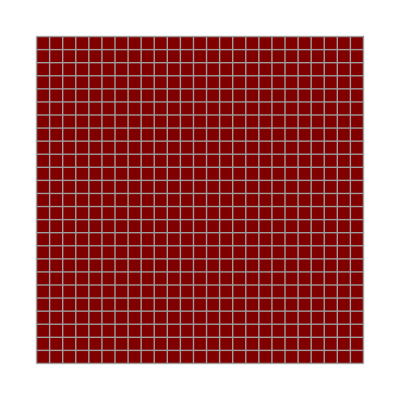

```mathematica
Table[χ[[k]].ρ[[l]],{k,n^2},{l,n^2}]//Chop;
ArrayPlot[%,Mesh->True]
```

```mathematica
Do[χ[[k]]=χ[[k]]/χ[[k]].ρ[[k]],{k,n^2}]//Chop
```

Dot::dotsh: Tensors {0., -0.316228, 0., 0., 0.316228, 0., 0.316228, 0., -0.316228, 0., -0.316228, 0., 0., 0.316228, 0., 0.316228, 0., -0.316228, 0., 0., 0., 0., 0.316228, 0., -0.316228} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0., 0., -0.316228, 0.316228, 0., 0.316228, 0., 0., 0., -0.316228, 0., -0.316228, 0.316228, 0., 0., 0., 0., 0., -0.316228, 0.316228, -0.316228, 0.316228, 0., 0., 0.} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, -0.255834 + 0.185874\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.255834  - 0.185874\ ⅈ, 0.  + 0.\ ⅈ, -0.0977198 - 0.30075\ ⅈ, 0.  + 0.\ ⅈ, -0.255834 - 0.185874\ ⅈ, 0.  + 0.\ ⅈ, « 5 », -0.0977198 + 0.30075\ ⅈ, 0.  + 0.\ ⅈ, 0.316228  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.255834  + 0.185874\ ⅈ, 0.  + 0.\ ⅈ, 0.0977198  + 0.30075\ ⅈ} and {1., 0., 0., 0., 0., 0., 0., 0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

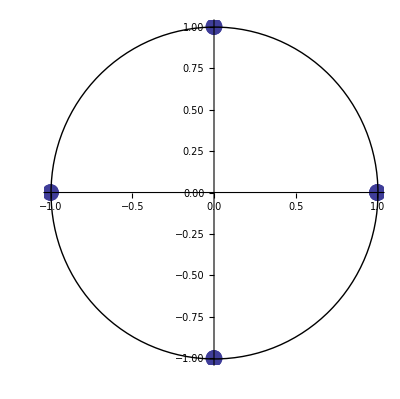

```mathematica
Show[ListPlot[{Re[#],Im[#]}&/@λ//N,AspectRatio->Automatic,ImageSize->Scaled[0.5],PlotStyle->PointSize[0.03]],Graphics[Circle[{0,0},1]]]
```

```mathematica
λ[[1;;2]]
λ[[3;;10]]
λ[[11;;12]]
λ[[13;;17]]
λ[[18;;25]]
```

{-1.,-1.}

Part::take: Cannot take positions 3 through 10 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦3;;10⟧

Part::take: Cannot take positions 11 through 12 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦11;;12⟧

Part::take: Cannot take positions 13 through 17 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦13;;17⟧

Part::take: Cannot take positions 18 through 25 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦18;;25⟧

```mathematica
κ==λ
```

False

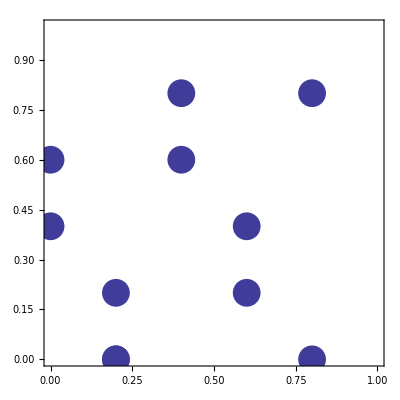
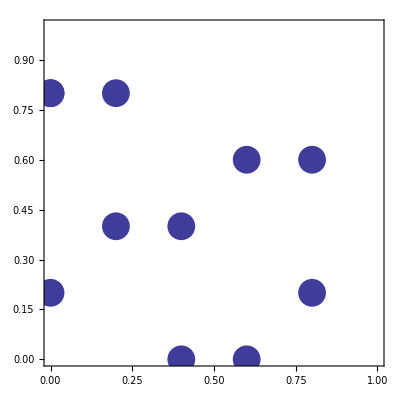
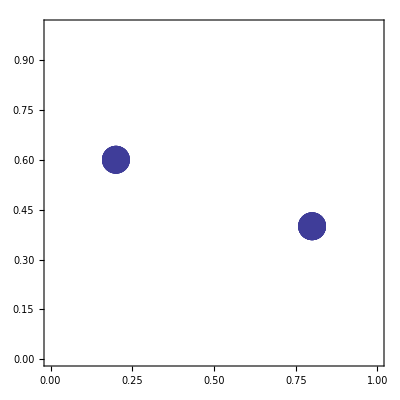
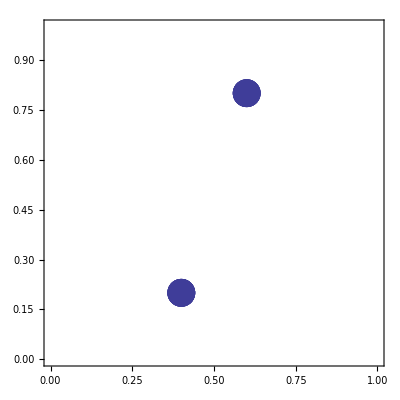
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
o0=orbitPlot[1,{0,0}];
o1=orbitPlot[10,{1/5,0}];
o2=orbitPlot[10,S[{1/5,0}]];
o3=orbitPlot[10,{4/5,2/5}];
o4=orbitPlot[10,S[{4/5,2/5}]];
Grid[{{o0,o1,o2},{o3,o4}}]
```

```mathematica
P = Table[Table[ρ[[k,i]]*χ[[k,j]],{i,n^2},{j,n^2}],{k,n^2}];
```

Part::partw: Part 10 of {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
l=13
λ[[l]]
eigenstatePlot[n,ρ[[l]],o1]
l=14
λ[[l]]
eigenstatePlot[n,ρ[[l]],o2]
l=15
λ[[l]]
eigenstatePlot[n,ρ[[l]],o3]
l=16
λ[[l]]
eigenstatePlot[n,ρ[[l]],o4]
l=17
λ[[l]]
eigenstatePlot[n,ρ[[l]],o0]
```

13

Part::partw: Part 13 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦13⟧

Part::partw: Part 13 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 13 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

14

Part::partw: Part 14 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦14⟧

Part::partw: Part 14 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 14 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

15

Part::partw: Part 15 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦15⟧

Part::partw: Part 15 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 15 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

16

Part::partw: Part 16 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦16⟧

Part::partw: Part 16 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 16 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

17

Part::partw: Part 17 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦17⟧

Part::partw: Part 17 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 17 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

Part::partw: Part 13 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

Part::partw: Part 14 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

Part::partw: Part 15 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦13⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦14⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦15⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦16⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦17⟧}

Part::partw: Part 13 of « 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

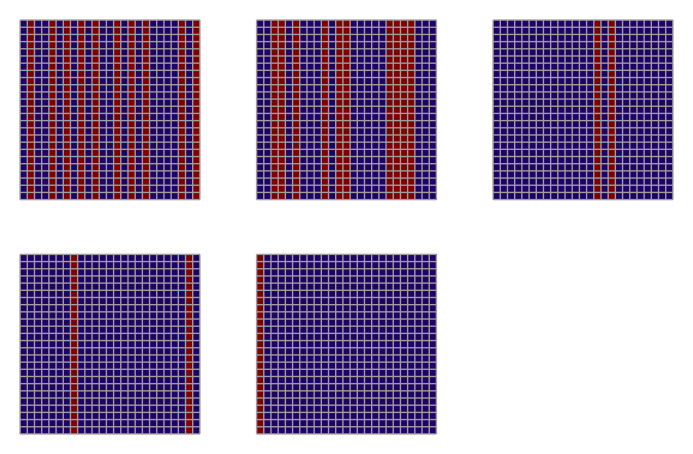

```mathematica
{λ[[13]],λ[[14]],λ[[15]],λ[[16]],λ[[17]]}
GraphicsGrid[{{projectorPlot[P[[13]]],
projectorPlot[P[[14]]],
projectorPlot[P[[15]]]},
{projectorPlot[P[[16]]],projectorPlot[P[[17]]]}}]
```

1

-1.

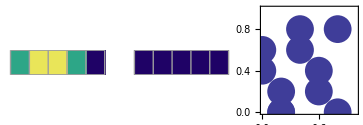

2

-1.

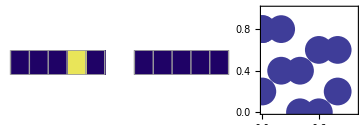

11

Part::partw: Part 11 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦11⟧

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

12

Part::partw: Part 12 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦12⟧

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

```mathematica
l=1
λ[[l]]
eigenstatePlot[n,ρ[[l]],o1]
l=2
λ[[l]]
eigenstatePlot[n,ρ[[l]],o2]
l=11
λ[[l]]
eigenstatePlot[n,ρ[[l]],o3]
l=12
λ[[l]]
eigenstatePlot[n,ρ[[l]],o4]
```

Part::partw: Part 11 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

Part::partw: Part 12 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{-1.,-1.,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦11⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦12⟧}

Dot::dotsh: Tensors {0, -0.316228, 0, 0, 0.316228, 0, 0.316228, 0, -0.316228, 0, -0.316228, 0, 0, 0.316228, 0, 0.316228, 0, -0.316228, 0, 0, 0, 0, 0.316228, 0, -0.316228} and {0, 0.5, 0.5, 0, -0.5, 0, 0, 0, -0.5} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {0, 0.5, 0.5, 0, -0.5, 0, 0, 0, -0.5} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

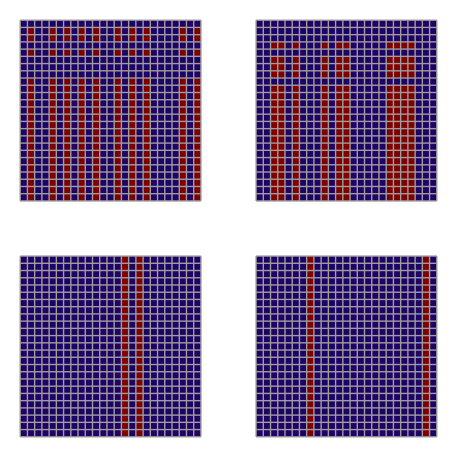

```mathematica
{λ[[1]],λ[[2]],λ[[11]],λ[[12]]}
GraphicsGrid[{{projectorPlot[P[[1]]],
projectorPlot[P[[2]]]},
{projectorPlot[P[[11]]],
projectorPlot[P[[12]]]}}]
```

3

1.

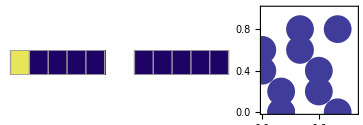

4

1.

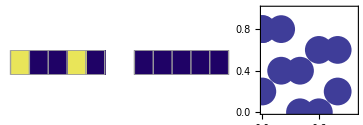

```mathematica
l=3
λ[[l]]
eigenstatePlot[n,ρ[[l]],o1]
l=4
λ[[l]]
eigenstatePlot[n,ρ[[l]],o2]
```

```mathematica
l=18
λ[[l]]
eigenstatePlot[n,ρ[[l]],o1]
l=19
λ[[l]]
eigenstatePlot[n,ρ[[l]],o2]
```

18

Part::partw: Part 18 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦18⟧

Part::partw: Part 18 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 18 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

19

Part::partw: Part 19 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦19⟧

Part::partw: Part 19 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 19 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

Part::partw: Part 18 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

Part::partw: Part 19 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{1.,1.,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦18⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦19⟧}

Dot::dotsh: Tensors {0, -0.255834 + 0.185874\ ⅈ, 0, 0, 0.255834  - 0.185874\ ⅈ, 0, -0.0977198 - 0.30075\ ⅈ, 0, -0.255834 - 0.185874\ ⅈ, 0, 0.0977198  - 0.30075\ ⅈ, 0, 0, -0.316228, 0, -0.0977198 + 0.30075\ ⅈ, 0, 0.316228, 0, 0, 0, 0, 0.255834  + 0.185874\ ⅈ, 0, 0.0977198  + 0.30075\ ⅈ} and {1., 0, 0, 0, 0, 0, 0, 0, 0} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {1., 0, 0, 0, 0, 0, 0, 0, 0} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

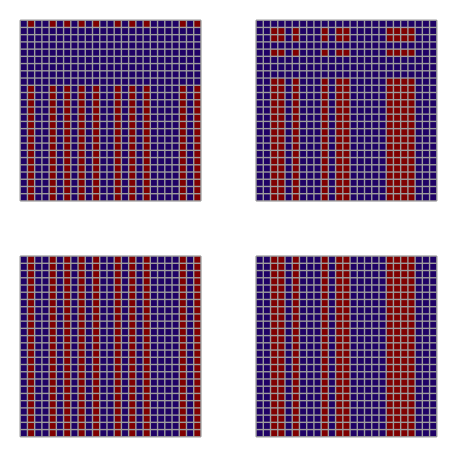

```mathematica
{λ[[3]],λ[[4]],λ[[18]],λ[[19]]}
GraphicsGrid[{{projectorPlot[P[[3]]],
projectorPlot[P[[4]]]},
{projectorPlot[P[[18]]],
projectorPlot[P[[19]]]}}]
```

7

5.55112×10^-17+1. ⅈ

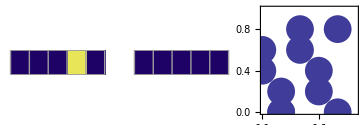

8

5.55112×10^-17-1. ⅈ

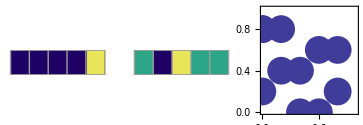

```mathematica
l=7
λ[[l]]
eigenstatePlot[n,ρ[[l]],o1]
l=8
λ[[l]]
eigenstatePlot[n,ρ[[l]],o2]
```

```mathematica
l=22
λ[[l]]
eigenstatePlot[n,ρ[[l]],o1]
l=23
λ[[l]]
eigenstatePlot[n,ρ[[l]],o2]
```

22

Part::partw: Part 22 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦22⟧

Part::partw: Part 22 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 22 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

23

Part::partw: Part 23 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦23⟧

Part::partw: Part 23 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 23 of « 1 » does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

Part::partw: Part 22 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

Part::partw: Part 23 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦22⟧,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦23⟧}

Dot::dotsh: Tensors {0, -0.0977198 + 0.30075\ ⅈ, 0, 0, 0.0977198  - 0.30075\ ⅈ, 0, -0.255834 + 0.185874\ ⅈ, 0, -0.0977198 - 0.30075\ ⅈ, 0, 0.255834  + 0.185874\ ⅈ, 0, 0, 0.316228, 0, -0.255834 - 0.185874\ ⅈ, 0, -0.316228, 0, 0, 0, 0, 0.0977198  + 0.30075\ ⅈ, 0, 0.255834  - 0.185874\ ⅈ} and {0, 0, 0, 0.5, 0, 0.  + 0.5\ ⅈ, -0.5, 0.  - 0.5\ ⅈ, 0} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {0, 0, 0, 0.5, 0, 0.  + 0.5\ ⅈ, -0.5, 0.  - 0.5\ ⅈ, 0} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

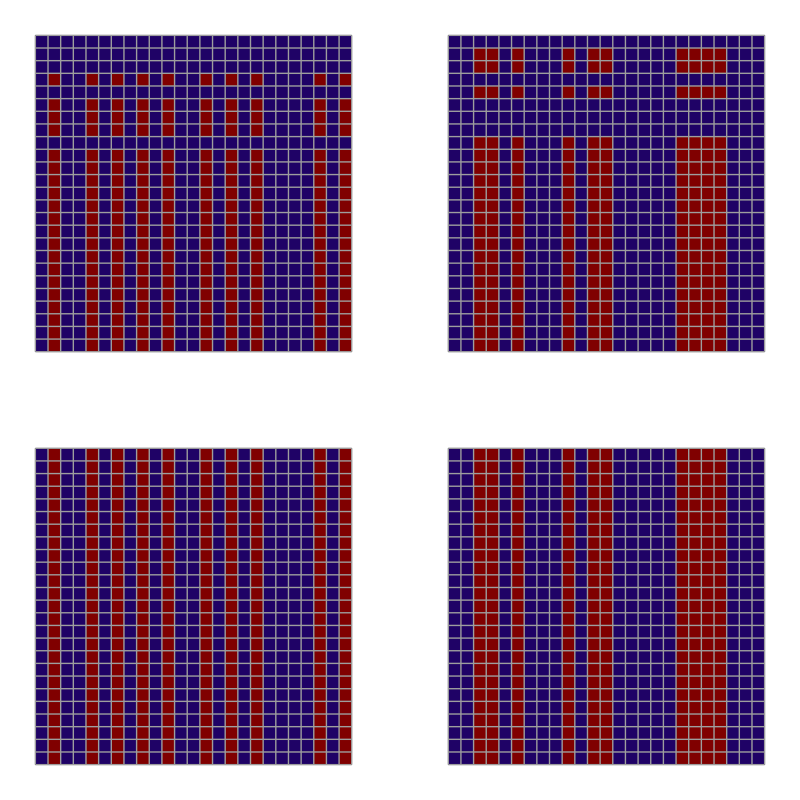

```mathematica
{λ[[7]],λ[[8]],λ[[22]],λ[[23]]}
GraphicsGrid[{{projectorPlot[P[[7]]],
projectorPlot[P[[8]]]},
{projectorPlot[P[[22]]],
projectorPlot[P[[23]]]}}]
```

```mathematica
LL=Sum[λ[[k]]P[[k]],{k,n^2}];
```

Part::partw: Part 10 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

Part::partw: Part 11 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

Part::partw: Part 12 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

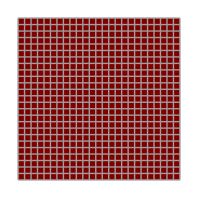

-Graphics-

Part::partw: Part 17 of « 1 » does not exist.

Part::partw: Part 17 of {-1., -1., 1., 1., 1., 0.  + 1.\ ⅈ, 0.  + 1.\ ⅈ, 0.  - 1.\ ⅈ, 0.  - 1.\ ⅈ} does not exist.

Part::partw: Part 17 of « 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Dot::dotsh: Tensors {0, -0.255834 + 0.185874\ ⅈ, 0, 0, 0.255834  - 0.185874\ ⅈ, 0, -0.0977198 - 0.30075\ ⅈ, 0, -0.255834 - 0.185874\ ⅈ, 0, 0.0977198  - 0.30075\ ⅈ, 0, 0, -0.316228, 0, -0.0977198 + 0.30075\ ⅈ, 0, 0.316228, 0, 0, 0, 0, 0.255834  + 0.185874\ ⅈ, 0, 0.0977198  + 0.30075\ ⅈ} and {1., 0, 0, 0, 0, 0, 0, 0, 0} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

False

```mathematica
ArrayPlot[LL,Mesh->True]
ArrayPlot[L,Mesh->True]
Chop[LL]==L
```

#### n=6

```mathematica
n=6
n^2
```

6

36

```mathematica
{L,permutation}=Perron;
K=Koopman;
{λ,ρ}=Eigensystem[L//N];
{κ,χ}=Eigensystem[K//N];
```

Set::shape: Lists {L, permutation} and Perron are not the same shape.

```mathematica
PermutationCycles[permutation]
Flatten[rules/@First[%]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.6]
```

Cycles[{{2,5,3,9},{4,8,7,6}}]

{2->5,5->3,3->9,9->2,4->8,8->7,7->6,6->4}

-Graphics-

```mathematica
ArrayPlot[L,Mesh->True]
ArrayPlot[K,Mesh->True]
K== Transpose[L]
```

-Graphics-

-Graphics-

False

```mathematica
CharacteristicPolynomial[L,z]
Factor[%]
```

1-z-2 z^4+2 z^5+z^8-z^9

-(-1+z)^3 (1+z)^2 (1+z^2)^2

```mathematica
Roots[(z-1)^6==0,z]
Roots[(z+1)^4==0,z]
Roots[(z^2+1)^4==0,z]
Roots[(z^2-z+1)^2==0,z]
Roots[(z^2+z+1)^3==0,z]
Roots[(z^4-z^2+1)^2==0,z]
```

z==1||z==1||z==1||z==1||z==1||z==1

z==-1||z==-1||z==-1||z==-1

z==ⅈ||z==ⅈ||z==ⅈ||z==ⅈ||z==-ⅈ||z==-ⅈ||z==-ⅈ||z==-ⅈ

z==(-1)^(1/3)||z==(-1)^(1/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)

z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)

z==-(-1)^(1/6)||z==-(-1)^(1/6)||z==(-1)^(1/6)||z==(-1)^(1/6)||z==-(-1)^(5/6)||z==-(-1)^(5/6)||z==(-1)^(5/6)||z==(-1)^(5/6)

Dot::dotsh: Tensors {0., -0.288675, 0., 0., 0., -0.288675, 0., 0.288675, 0., 0., 0.288675, 0., 0., 0., 0., 0., 0., 0.288675, 0., -0.288675, -0.288675, 0., -0.288675, -0.288675, 0., 0.288675, 0., 0., 0., 0., 0., 0., 0.288675, 0., 0., 0.288675} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0., -0.288675, 0., 0., 0., -0.288675, 0., 0.288675, 0., 0., 0.288675, 0., 0., 0., 0., 0., 0., 0.288675, 0., -0.288675, -0.288675, 0., -0.288675, -0.288675, 0., 0.288675, 0., 0., 0., 0., 0., 0., 0.288675, 0., 0., 0.288675} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

Dot::dotsh: Tensors {0., -0.288675, 0., 0., 0., -0.288675, 0., 0.288675, 0., 0., 0.288675, 0., 0., 0., 0., 0., 0., 0.288675, 0., -0.288675, -0.288675, 0., -0.288675, -0.288675, 0., 0.288675, 0., 0., 0., 0., 0., 0., 0.288675, 0., 0., 0.288675} and {1., 0., 0., 0., 0., 0., 0., 0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

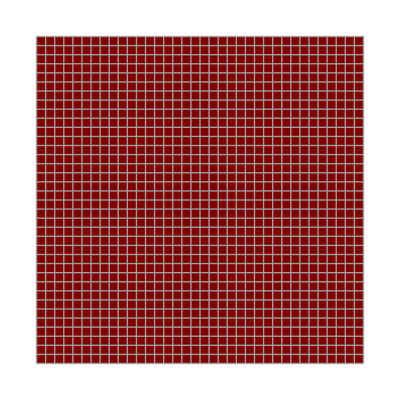

```mathematica
Table[χ[[k]].ρ[[l]],{k,n^2},{l,n^2}]//Chop;
ArrayPlot[%,Mesh->True]
```

```mathematica
Do[χ[[k]]=χ[[k]]/χ[[k]].ρ[[k]],{k,n^2}]//Chop
```

Dot::dotsh: Tensors {0., -0.288675, 0., 0., 0., -0.288675, 0., 0.288675, 0., 0., 0.288675, 0., 0., 0., 0., 0., 0., 0.288675, 0., -0.288675, -0.288675, 0., -0.288675, -0.288675, 0., 0.288675, 0., 0., 0., 0., 0., 0., 0.288675, 0., 0., 0.288675} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0., 0., 0., 0., 0., 0., 0.288675, 0., -0.288675, 0.288675, 0., -0.288675, 0., -0.288675, 0., 0.288675, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.288675, 0., -0.288675, 0.288675, -0.288675, 0., 0.288675, -0.288675, 0.} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.288675  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 + 7.63278×10^-16\ ⅈ, 0.  + 0.\ ⅈ, -0.25 + 0.144338\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.25  + 0.144338\ ⅈ, « 14 », -4.57967×10^-16 - 0.288675\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.25 - 0.144338\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.25  - 0.144338\ ⅈ} and {1., 0., 0., 0., 0., 0., 0., 0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
Show[ListPlot[{Re[#],Im[#]}&/@λ//N,AspectRatio->Automatic,ImageSize->Scaled[0.5],PlotStyle->PointSize[0.03]],Graphics[Circle[{0,0},1]]]
```

-Graphics-

```mathematica
λ[[1;;2]]
λ[[7;;8]]
λ[[1]]==Exp[I 2 Pi 6/12]
λ[[3;;6]]
λ[[3]]==Exp[I 2 Pi 5/12]
λ[[9;;14]]
λ[[9]]==Exp[I 2 Pi 4/12]
λ[[15;;18]]//Chop
λ[[29;;32]]//Chop
Chop[λ[[15]]]==Exp[I 2 Pi 3/12]
λ[[19;;22]]
λ[[19]]==Exp[I 2 Pi 2/12]
λ[[23;;28]]
λ[[23]]==Exp[I 2 Pi 0/12]
λ[[33;;36]]
λ[[33]]==Exp[I 2 Pi 1/12]
```

{-1.,-1.}

{5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ}

True

{1.,1.,1.,5.55112×10^-17+1. ⅈ}

False

Part::take: Cannot take positions 9 through 14 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦9;;14⟧

False

Part::take: Cannot take positions 15 through 18 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 15 through 18 in {-1., -1., 1., 1., 1., 0.  + 1.\ ⅈ, 0.  + 1.\ ⅈ, 0.  - 1.\ ⅈ, 0.  - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦15;;18⟧

Part::take: Cannot take positions 29 through 32 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 29 through 32 in {-1., -1., 1., 1., 1., 0.  + 1.\ ⅈ, 0.  + 1.\ ⅈ, 0.  - 1.\ ⅈ, 0.  - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦29;;32⟧

Part::partw: Part 15 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

Part::partw: Part 15 of {-1., -1., 1., 1., 1., 0.  + 1.\ ⅈ, 0.  + 1.\ ⅈ, 0.  - 1.\ ⅈ, 0.  - 1.\ ⅈ} does not exist.

{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦15⟧==ⅈ

Part::take: Cannot take positions 19 through 22 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦19;;22⟧

Part::partw: Part 19 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦19⟧==ⅇ^((ⅈ π)/3)

Part::take: Cannot take positions 23 through 28 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦23;;28⟧

Part::partw: Part 23 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦23⟧==1

Part::take: Cannot take positions 33 through 36 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦33;;36⟧

Part::partw: Part 33 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦33⟧==ⅇ^((ⅈ π)/6)

```mathematica
S[{1/6,0}]
```

{0,5/6}

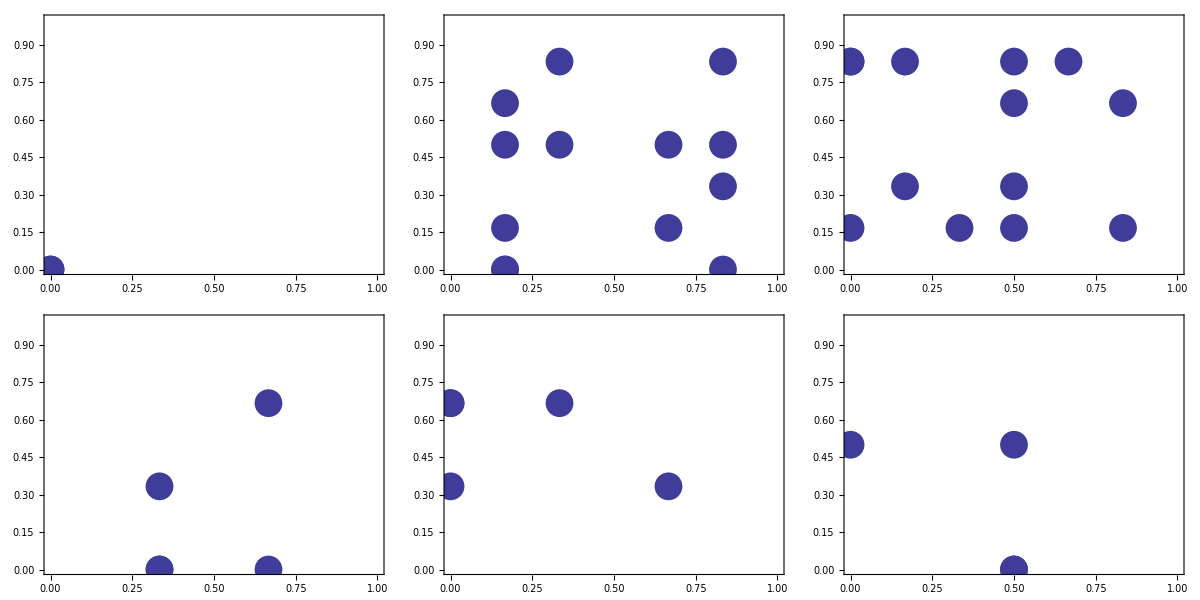

```mathematica
o0=orbitPlot[1,{0,0}];
o1=orbitPlot[12,{1/6,0}];
o2=orbitPlot[12,S[{1/6,0}]];
o3=orbitPlot[4,{2/6,0}];
o4=orbitPlot[4,S[{2/6,0}]];
o5=orbitPlot[3,{3/6,0}];
Grid[{{o0,o1,o2},{o3,o4,o5}}]
```

#### n=7

```mathematica
n=7
n^2
```

7

49

```mathematica
{L,permutation}=Perron;
K=Koopman;
{λ,ρ}=Eigensystem[L//N];
{κ,χ}=Eigensystem[K//N];
```

Set::shape: Lists {L, permutation} and Perron are not the same shape.

```mathematica
PermutationCycles[permutation]
Flatten[rules/@First[%]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.6]
```

Cycles[{{2,5,3,9},{4,8,7,6}}]

{2->5,5->3,3->9,9->2,4->8,8->7,7->6,6->4}

-Graphics-

```mathematica
ArrayPlot[L,Mesh->True]
```

-Graphics-

```mathematica
CharacteristicPolynomial[L,z]
Factor[%]
```

1-z-2 z^4+2 z^5+z^8-z^9

-(-1+z)^3 (1+z)^2 (1+z^2)^2

```mathematica
Roots[(z-1)^7==0,z]
Roots[(z+1)^6==0,z]
Roots[(z^2+1)^6==0,z]
Roots[(z^4+1)^6==0,z]
```

z==1||z==1||z==1||z==1||z==1||z==1||z==1

z==-1||z==-1||z==-1||z==-1||z==-1||z==-1

z==ⅈ||z==ⅈ||z==ⅈ||z==ⅈ||z==ⅈ||z==ⅈ||z==-ⅈ||z==-ⅈ||z==-ⅈ||z==-ⅈ||z==-ⅈ||z==-ⅈ

z==(-1)^(1/4)||z==(-1)^(1/4)||z==(-1)^(1/4)||z==(-1)^(1/4)||z==(-1)^(1/4)||z==(-1)^(1/4)||z==(-1)^(3/4)||z==(-1)^(3/4)||z==(-1)^(3/4)||z==(-1)^(3/4)||z==(-1)^(3/4)||z==(-1)^(3/4)||z==-(-1)^(1/4)||z==-(-1)^(1/4)||z==-(-1)^(1/4)||z==-(-1)^(1/4)||z==-(-1)^(1/4)||z==-(-1)^(1/4)||z==-(-1)^(3/4)||z==-(-1)^(3/4)||z==-(-1)^(3/4)||z==-(-1)^(3/4)||z==-(-1)^(3/4)||z==-(-1)^(3/4)

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 1.11022×10^-16 + 0.353553\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 4.30211×10^-16 + 0.353553\ ⅈ, 0.  + 0.\ ⅈ, -0.353553 - 2.77556×10^-17\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 25 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.353553  + 1.94289×10^-16\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.353553 - 2.22045×10^-16\ ⅈ} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 1.11022×10^-16 + 0.353553\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 4.30211×10^-16 + 0.353553\ ⅈ, 0.  + 0.\ ⅈ, -0.353553 - 2.77556×10^-17\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 25 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.353553  + 1.94289×10^-16\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.353553 - 2.22045×10^-16\ ⅈ} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 1.11022×10^-16 + 0.353553\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 4.30211×10^-16 + 0.353553\ ⅈ, 0.  + 0.\ ⅈ, -0.353553 - 2.77556×10^-17\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 25 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.353553  + 1.94289×10^-16\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.353553 - 2.22045×10^-16\ ⅈ} and {1., 0., 0., 0., 0., 0., 0., 0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

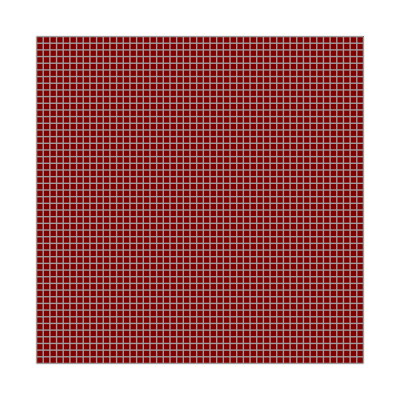

```mathematica
Table[χ[[k]].ρ[[l]],{k,n^2},{l,n^2}]//Chop;
ArrayPlot[%,Mesh->True]
```

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Set::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Set::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Set::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Set :: partw will be suppressed during this calculation.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 1.11022×10^-16 + 0.353553\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 4.30211×10^-16 + 0.353553\ ⅈ, 0.  + 0.\ ⅈ, -0.353553 - 2.77556×10^-17\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 25 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.353553  + 1.94289×10^-16\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.353553 - 2.22045×10^-16\ ⅈ} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 1.11022×10^-16 + 0.353553\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 4.30211×10^-16 + 0.353553\ ⅈ, 0.  + 0.\ ⅈ, -0.353553 - 2.77556×10^-17\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 25 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.353553  + 1.94289×10^-16\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.353553 - 2.22045×10^-16\ ⅈ} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 1.11022×10^-16 + 0.353553\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 4.30211×10^-16 + 0.353553\ ⅈ, 0.  + 0.\ ⅈ, -0.353553 - 2.77556×10^-17\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 25 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.353553  + 1.94289×10^-16\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.353553 - 2.22045×10^-16\ ⅈ} and {1., 0., 0., 0., 0., 0., 0., 0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

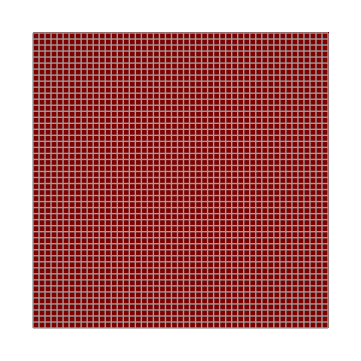

```mathematica
p1={0,0,0,0,1,-1};
p=Join[{0,0,0,1,-1},p1,p1,p1,p1,p1,p1,p1,{0,0}];
Block[{ρaux = Table[0,{l,n^2},{i,n^2}]},
Do[ρaux[[l]]=ρ[[l+p[[l]]]],{l,n^2}];
Do[ρ[[l]]=ρaux[[l]],{l,n^2}];
]
Table[χ[[k]].ρ[[l]],{k,n^2},{l,n^2}]//Chop;
ArrayPlot[%,Mesh->True]
```

```mathematica
Do[χ[[k]]=χ[[k]]/χ[[k]].ρ[[k]],{k,n^2}]//Chop
```

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 1.11022×10^-16 + 0.353553\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 4.30211×10^-16 + 0.353553\ ⅈ, 0.  + 0.\ ⅈ, -0.353553 - 2.77556×10^-17\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 25 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.353553  + 1.94289×10^-16\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.353553 - 2.22045×10^-16\ ⅈ} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.353553 - 2.77556×10^-17\ ⅈ, -0.353553 - 2.08167×10^-16\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 20 », 0.  + 0.\ ⅈ, 0.353553  + 1.94289×10^-16\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 6.245×10^-16 + 0.353553\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 3.19189×10^-16 + 0.353553\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -5.82867×10^-16 - 0.353553\ ⅈ, « 27 », 0.  + 0.\ ⅈ, 0.353553  - 2.08167×10^-16\ ⅈ, -0.353553 + 1.66533×10^-16\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -5.68989×10^-16 - 0.353553\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ} and {1., 0., 0., 0., 0., 0., 0., 0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
Show[ListPlot[{Re[#],Im[#]}&/@λ//N,AspectRatio->Automatic,ImageSize->Scaled[0.5],PlotStyle->PointSize[0.03]],Graphics[Circle[{0,0},1]]]
```

-Graphics-

```mathematica
Table[λ[[k]],{k,n^2}]//Chop
```

Part::partw: Part 10 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

Part::partw: Part 11 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

Part::partw: Part 12 of {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦10⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦11⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦12⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦13⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦14⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦15⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦16⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦17⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦18⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦19⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦20⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦21⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦22⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦23⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦24⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦25⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦26⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦27⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦28⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦29⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦30⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦31⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦32⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦33⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦34⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦35⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦36⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦37⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦38⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦39⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦40⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦41⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦42⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦43⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦44⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦45⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦46⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦47⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦48⟧,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦49⟧}

```mathematica
κ==λ
```

False

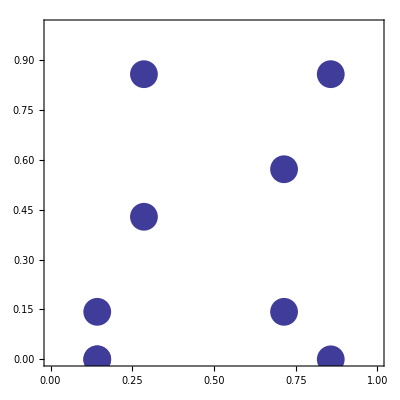
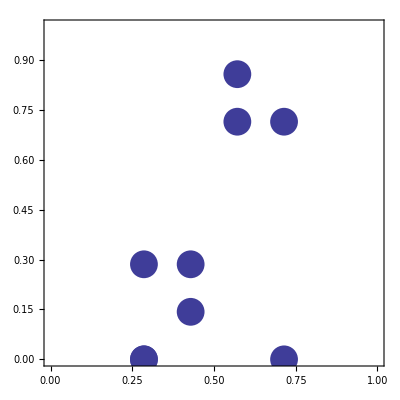
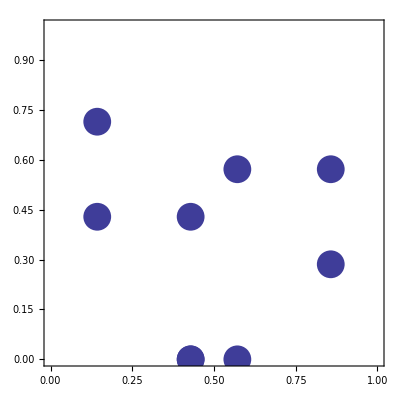
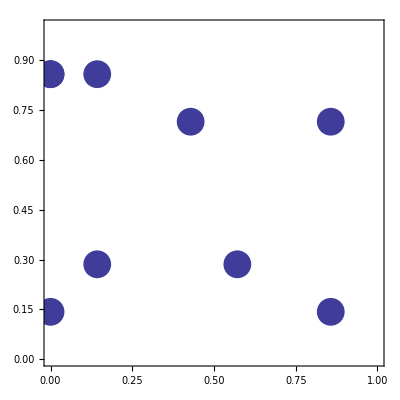
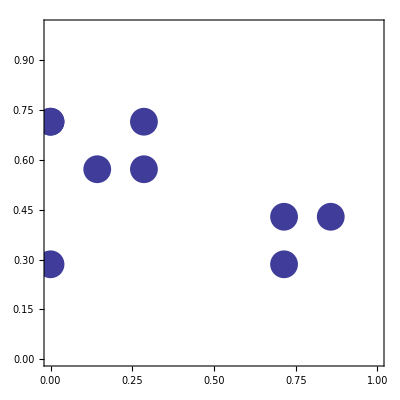
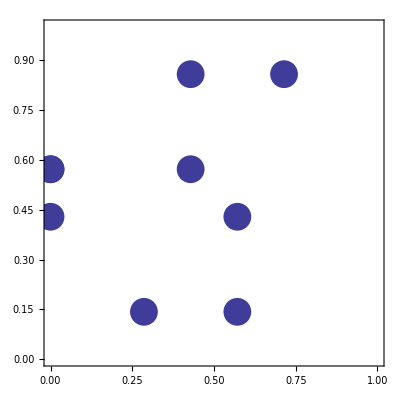
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
o0=orbitPlot[1,{0,0}];
o1=orbitPlot[8,{1/7,0}];
o2=orbitPlot[8,{2/7,0}];
o3=orbitPlot[8,{3/7,0}];
o4=orbitPlot[8,S[{1/7,0}]];
o5=orbitPlot[8,S[{2/7,0}]];
o6=orbitPlot[8,S[{3/7,0}]];
Grid[{{o0,o1,o2,o3},{o4,o5,o6}}]
```

#### n=8

```mathematica
n=8
n^2
```

8

64

```mathematica
{L,permutation}=Perron;
K=Koopman;
{λ,ρ}=Eigensystem[L//N];
{κ,χ}=Eigensystem[K//N];
```

Set::shape: Lists {L, permutation} and Perron are not the same shape.

```mathematica
PermutationCycles[permutation]
Flatten[rules/@First[%]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.6]
```

Cycles[{{2,5,3,9},{4,8,7,6}}]

{2->5,5->3,3->9,9->2,4->8,8->7,7->6,6->4}

-Graphics-

```mathematica
ArrayPlot[L,Mesh->True]
```

-Graphics-

```mathematica
CharacteristicPolynomial[L,z]
Factor[%]
```

1-z-2 z^4+2 z^5+z^8-z^9

-(-1+z)^3 (1+z)^2 (1+z^2)^2

```mathematica
Roots[(z-1)^14==0,z]
Roots[(z+1)^8==0,z]
Roots[(z^2-z+1)^8==0,z]
Roots[(z^2+z+1)^13==0,z]
```

z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1

z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1

z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)

z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 11 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 14 »} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 11 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 14 »} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 11 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 14 »} and {1., 0., 0., 0., 0., 0., 0., 0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

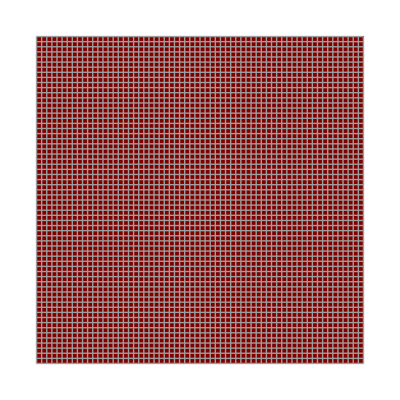

```mathematica
Table[χ[[k]].ρ[[l]],{k,n^2},{l,n^2}]//Chop;
ArrayPlot[%,Mesh->True]
```

```mathematica
Do[χ[[k]]=χ[[k]]/χ[[k]].ρ[[k]],{k,n^2}]//Chop
```

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 11 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 14 »} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 13 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 + 0.5\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 14 »} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 14 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.288675 + 0.5\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 14 »} and {1., 0., 0., 0., 0., 0., 0., 0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
Show[ListPlot[{Re[#],Im[#]}&/@λ//N,AspectRatio->Automatic,ImageSize->Scaled[0.5],PlotStyle->PointSize[0.03]],Graphics[Circle[{0,0},1]]]
```

-Graphics-

```mathematica
λ//Chop
```

{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}

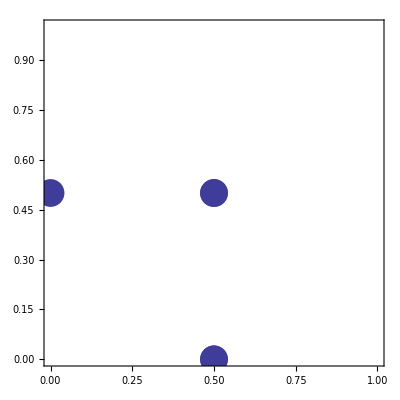
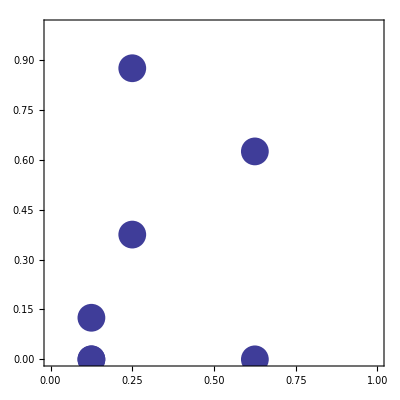
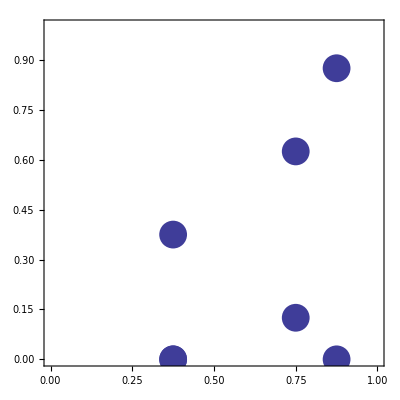
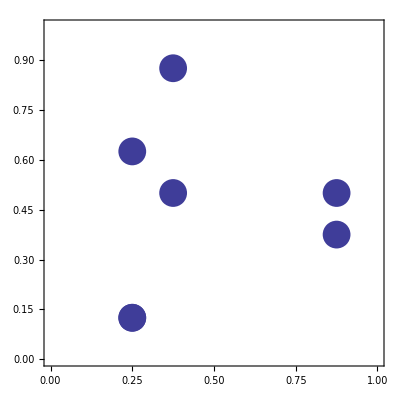
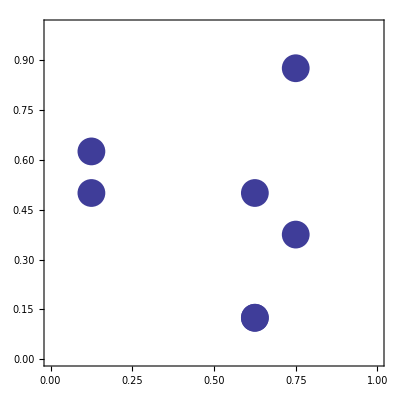
-Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
o0=orbitPlot[1,{0,0}];
o1=orbitPlot[3,{6/8,0}];
o2=orbitPlot[3,{2/8,0}];
o3=orbitPlot[3,S[{2/8,0}]];
o4=orbitPlot[3,S[{6/8,0}]];
o5=orbitPlot[4,{4/8,0}];
o6=orbitPlot[6,{1/8,0}];
o7=orbitPlot[6,{3/8,0}];
o8=orbitPlot[6,{2/8,1/8}];
o9=orbitPlot[6,{5/8,1/8}];
o10=orbitPlot[6,S[{1/8,0}]];
o11=orbitPlot[6,S[{3/8,0}]];
o12=orbitPlot[6,S[{2/8,1/8}]];
o13=orbitPlot[6,S[{5/8,1/8}]];
Grid[{{o0},{o1,o2,o3,o4},{o5},{o6,o7,o8,o9},{o10,o11,o12,o13}}]
```

#### n=9

```mathematica
n=9
n^2
```

9

81

```mathematica
{L,permutation}=Perron;
K=Koopman;
{λ,ρ}=Eigensystem[L//N];
{κ,χ}=Eigensystem[K//N];
```

Set::shape: Lists {L, permutation} and Perron are not the same shape.

```mathematica
PermutationCycles[permutation]
Flatten[rules/@First[%]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.6]
```

Cycles[{{2,5,3,9},{4,8,7,6}}]

{2->5,5->3,3->9,9->2,4->8,8->7,7->6,6->4}

-Graphics-

```mathematica
ArrayPlot[L,Mesh->True]
```

-Graphics-

```mathematica
CharacteristicPolynomial[L,z]
Factor[%]
```

1-z-2 z^4+2 z^5+z^8-z^9

-(-1+z)^3 (1+z)^2 (1+z^2)^2

```mathematica
Roots[(z-1)^9==0,z]
Roots[(z+1)^8==0,z]
Roots[(z^2+1)^8==0,z]
Roots[(z^2-z+1)^6==0,z]
Roots[(z^2+z+1)^6==0,z]
Roots[(z^4-z^2+1)^6==0,z]
```

z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1

z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1

z==ⅈ||z==ⅈ||z==ⅈ||z==ⅈ||z==ⅈ||z==ⅈ||z==ⅈ||z==ⅈ||z==-ⅈ||z==-ⅈ||z==-ⅈ||z==-ⅈ||z==-ⅈ||z==-ⅈ||z==-ⅈ||z==-ⅈ

z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)

z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)

z==-(-1)^(1/6)||z==-(-1)^(1/6)||z==-(-1)^(1/6)||z==-(-1)^(1/6)||z==-(-1)^(1/6)||z==-(-1)^(1/6)||z==(-1)^(1/6)||z==(-1)^(1/6)||z==(-1)^(1/6)||z==(-1)^(1/6)||z==(-1)^(1/6)||z==(-1)^(1/6)||z==-(-1)^(5/6)||z==-(-1)^(5/6)||z==-(-1)^(5/6)||z==-(-1)^(5/6)||z==-(-1)^(5/6)||z==-(-1)^(5/6)||z==(-1)^(5/6)||z==(-1)^(5/6)||z==(-1)^(5/6)||z==(-1)^(5/6)||z==(-1)^(5/6)||z==(-1)^(5/6)

```mathematica
Table[χ[[k]].ρ[[l]],{k,n^2},{l,n^2}]//Chop;
ArrayPlot[%,Mesh->True]
```

Dot::dotsh: Tensors {0., -0.288675, 0., 0., 0., 0., 0., 0., -0.288675, 0., 0.288675, 0., 0., 0.288675, 0., 0., 0.288675, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., -0.288675, 0., -0.288675, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 31 »} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0., -0.288675, 0., 0., 0., 0., 0., 0., -0.288675, 0., 0.288675, 0., 0., 0.288675, 0., 0., 0.288675, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., -0.288675, 0., -0.288675, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 31 »} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

Dot::dotsh: Tensors {0., -0.288675, 0., 0., 0., 0., 0., 0., -0.288675, 0., 0.288675, 0., 0., 0.288675, 0., 0., 0.288675, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., -0.288675, 0., -0.288675, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 31 »} and {1., 0., 0., 0., 0., 0., 0., 0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

```mathematica
p1={1,-1};
p4=Table[0,{4}];
p6=Table[0,{6}];
p11=Table[0,{11}];
p=Join[p4,p1,p4,p1,p4,p1,p6,p1,p4,p1,p4,p1,p4,p1,p4,p1,p4,p1,p4,p1,p11,p1,p4,p1];
Block[{ρaux = Table[0,{l,n^2},{i,n^2}]},
Do[ρaux[[l]]=ρ[[l+p[[l]]]],{l,n^2}];
Do[ρ[[l]]=ρaux[[l]],{l,n^2}];
]
Table[χ[[k]].ρ[[l]],{k,n^2},{l,n^2}]//Chop;
ArrayPlot[%,Mesh->True]
```

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Set::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Set::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Set::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Set :: partw will be suppressed during this calculation.

Dot::dotsh: Tensors {0., -0.288675, 0., 0., 0., 0., 0., 0., -0.288675, 0., 0.288675, 0., 0., 0.288675, 0., 0., 0.288675, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., -0.288675, 0., -0.288675, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 31 »} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0., -0.288675, 0., 0., 0., 0., 0., 0., -0.288675, 0., 0.288675, 0., 0., 0.288675, 0., 0., 0.288675, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., -0.288675, 0., -0.288675, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 31 »} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

Dot::dotsh: Tensors {0., -0.288675, 0., 0., 0., 0., 0., 0., -0.288675, 0., 0.288675, 0., 0., 0.288675, 0., 0., 0.288675, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., -0.288675, 0., -0.288675, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 31 »} and {1., 0., 0., 0., 0., 0., 0., 0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

```mathematica
Show[ListPlot[{Re[#],Im[#]}&/@λ//N,AspectRatio->Automatic,ImageSize->Scaled[0.5],PlotStyle->PointSize[0.03]],Graphics[Circle[{0,0},1]]]
```

-Graphics-

```mathematica
λ//Chop
```

{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}

```mathematica
κ==λ
```

False

```mathematica
o0=orbitPlot[1,{0,0}];
o1=orbitPlot[4,{3/9,0}];
o2=orbitPlot[4,S[{3/9,0}]];
o3=orbitPlot[12,{1/9,0}];
o4=orbitPlot[12,{2/9,0}];
o5=orbitPlot[12,{4/9,0}];
o6=orbitPlot[12,S[{1/9,0}]];
o7=orbitPlot[12,S[{2/9,0}]];
o8=orbitPlot[12,S[{4/9,0}]];
Grid[{{o0},{o1,o2},{o3,o4,o5},{o6,o7,o8}}]
```

-Graphics- |  | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

#### n=10

```mathematica
n=10
n^2
```

10

100

```mathematica
{L,permutation}=Perron;
K=Koopman;
{λ,ρ}=Eigensystem[L//N];
{κ,χ}=Eigensystem[K//N];
```

Set::shape: Lists {L, permutation} and Perron are not the same shape.

```mathematica
PermutationCycles[permutation]
Flatten[rules/@First[%]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.6]
```

Cycles[{{2,5,3,9},{4,8,7,6}}]

{2->5,5->3,3->9,9->2,4->8,8->7,7->6,6->4}

-Graphics-

```mathematica
ArrayPlot[L,Mesh->True]
```

-Graphics-

```mathematica
K== Transpose[L]
```

False

```mathematica
CharacteristicPolynomial[L,z]
Factor[%]
```

1-z-2 z^4+2 z^5+z^8-z^9

-(-1+z)^3 (1+z)^2 (1+z^2)^2

```mathematica
Roots[(z-1)^10==0,z]
Roots[(z+1)^8==0,z]
Roots[(z^2-z+1)^4==0,z]
Roots[(z^2+z+1)^5==0,z]
Roots[(z^4-z^3+z^2-z+1)^4==0,z]
Roots[(z^4+z^3+z^2+z+1)^4==0,z]
Roots[(z^8-z^7+z^5-z^4+z^3-z+1)^2==0,z]
Roots[(z^8+z^7-z^5-z^4-z^3+z+1)^2==0,z]
```

z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1

z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1

z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)

z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)

z==(-1)^(1/5)||z==(-1)^(1/5)||z==(-1)^(1/5)||z==(-1)^(1/5)||z==-(-1)^(2/5)||z==-(-1)^(2/5)||z==-(-1)^(2/5)||z==-(-1)^(2/5)||z==(-1)^(3/5)||z==(-1)^(3/5)||z==(-1)^(3/5)||z==(-1)^(3/5)||z==-(-1)^(4/5)||z==-(-1)^(4/5)||z==-(-1)^(4/5)||z==-(-1)^(4/5)

z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)

z==-(-1)^(1/15)||z==-(-1)^(1/15)||z==(-1)^(2/15)||z==(-1)^(2/15)||z==(-1)^(4/15)||z==(-1)^(4/15)||z==-(-1)^(7/15)||z==-(-1)^(7/15)||z==(-1)^(8/15)||z==(-1)^(8/15)||z==-(-1)^(11/15)||z==-(-1)^(11/15)||z==-(-1)^(13/15)||z==-(-1)^(13/15)||z==(-1)^(14/15)||z==(-1)^(14/15)

z==(-1)^(1/15)||z==(-1)^(1/15)||z==-(-1)^(2/15)||z==-(-1)^(2/15)||z==-(-1)^(4/15)||z==-(-1)^(4/15)||z==(-1)^(7/15)||z==(-1)^(7/15)||z==-(-1)^(8/15)||z==-(-1)^(8/15)||z==(-1)^(11/15)||z==(-1)^(11/15)||z==(-1)^(13/15)||z==(-1)^(13/15)||z==-(-1)^(14/15)||z==-(-1)^(14/15)

```mathematica
Table[χ[[k]].ρ[[l]],{k,n^2},{l,n^2}]//Chop;
ArrayPlot[%,Mesh->True]
```

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, -0.0912871 + 0.158114\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.0912871  - 0.158114\ ⅈ, 0.  + 0.\ ⅈ, -0.182574 + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 25 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.0912871  - 0.158114\ ⅈ, 0.  + 0.\ ⅈ, -0.0912871 + 0.158114\ ⅈ, « 50 »} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, -0.0912871 + 0.158114\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.0912871  - 0.158114\ ⅈ, 0.  + 0.\ ⅈ, -0.182574 + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 25 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.0912871  - 0.158114\ ⅈ, 0.  + 0.\ ⅈ, -0.0912871 + 0.158114\ ⅈ, « 50 »} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, -0.0912871 + 0.158114\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.0912871  - 0.158114\ ⅈ, 0.  + 0.\ ⅈ, -0.182574 + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 25 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.0912871  - 0.158114\ ⅈ, 0.  + 0.\ ⅈ, -0.0912871 + 0.158114\ ⅈ, « 50 »} and {1., 0., 0., 0., 0., 0., 0., 0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

```mathematica
Block[{p1=Table[0,{l,1,42}],
p2={1,-1,1,-1,1,-1},
p3=Table[0,{l,49,50}],
p4={2,2,-2,-2},
p5=Table[0,{l,55,64}],
p6={1,-1},
p7=Table[0,{l,67,90}],
p8={1,-1,1,-1},
p9=Table[0,{l,95,100}],
p=Join[p1,p2,p3,p4,p5,p6,p7,p8,p9],
ρaux = Table[0,{l,n^2},{i,n^2}]},
Do[ρaux[[l]]=ρ[[l+p[[l]]]],{l,n^2}];
Do[ρ[[l]]=ρaux[[l]],{l,n^2}];
]
Do[χ[[k]]=χ[[k]]/χ[[k]].ρ[[k]],{k,n^2}]//Chop
```

Part::partw: Part 10 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pspec: Part specification 65 + {1, -1, 1, -1, 1, -1, 1, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 14 »} ⟦ 65 ⟧ is neither a machine-sized integer nor a list of machine-sized integers.

Part::pspec: Part specification 66 + {1, -1, 1, -1, 1, -1, 1, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 14 »} ⟦ 66 ⟧ is neither a machine-sized integer nor a list of machine-sized integers.

Part::pspec: Part specification 67 + {1, -1, 1, -1, 1, -1, 1, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 14 »} ⟦ 67 ⟧ is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Set::partw: Part 10 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Set::partw: Part 11 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Set::partw: Part 12 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Set :: partw will be suppressed during this calculation.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, -0.0912871 + 0.158114\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.0912871  - 0.158114\ ⅈ, 0.  + 0.\ ⅈ, -0.182574 + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 25 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.0912871  - 0.158114\ ⅈ, 0.  + 0.\ ⅈ, -0.0912871 + 0.158114\ ⅈ, « 50 »} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.0912871  - 0.158114\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.0912871 + 0.158114\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.0912871  + 0.158114\ ⅈ, 0.  + 0.\ ⅈ, « 27 », -0.182574 + 3.7817×10^-16\ ⅈ, 0.  + 0.\ ⅈ, 0.0912871  - 0.158114\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -0.0912871 + 0.158114\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 50 »} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, -0.0912871 - 0.158114\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.0912871  + 0.158114\ ⅈ, 0.  + 0.\ ⅈ, -0.182574 + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 25 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.0912871  + 0.158114\ ⅈ, 0.  + 0.\ ⅈ, -0.0912871 - 0.158114\ ⅈ, « 50 »} and {0., -0.5, -0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
λ==κ
Table[χ[[k]].ρ[[l]],{k,n^2},{l,n^2}]//Chop;
ArrayPlot[%,Mesh->True]
```

False

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, « 49 », « 50 »} and {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, « 49 », « 50 »} and {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0.  + 0.\ ⅈ, « 49 », « 50 »} and {0., -0.5, -0.5, 0., -0.5, 0., 0., 0., -0.5} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 11 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 12 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

```mathematica
Table[Chop[χ[[l]]-Conjugate[ρ[[l]]]]==Table[0,{n^2}],{l,n^2}]
```

Thread::tdlen: Objects of unequal length in {0.  + 0.\ ⅈ, « 49 », « 50 »} + {0., 0., 0., -0.5, 0., 0.5, -0.5, 0.5, 0.} cannot be combined.

Dot::dotsh: Tensors {0, -0.0912871 + 0.158114\ ⅈ, 0, 0, 0, 0, 0, 0, 0, 0.0912871  - 0.158114\ ⅈ, 0, -0.182574, 0, 0.182574, 0, 0, 0.0912871  + 0.158114\ ⅈ, 0, -0.0912871 - 0.158114\ ⅈ, 0, 0, « 10 », 0, -0.0912871 - 0.158114\ ⅈ, 0, 0, -0.182574, 0, 0.182574, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.0912871  - 0.158114\ ⅈ, 0, -0.0912871 + 0.158114\ ⅈ, « 50 »} and {0, 0, 0, 0.5, 0, -0.5, 0.5, -0.5, 0} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {0, 0, 0, -0.5, 0, 0.5, -0.5, 0.5, 0} + {0, « 49 », « 50 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 45 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 50 »} + {0., -0.5, -0.5, 0., 0.5, 0., 0., 0., 0.5} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

Part::partw: Part 10 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 10 of {{0, 0, 0, 0.5, 0, -0.5, 0.5, -0.5, 0}, {0, 0.5, 0.5, 0, -0.5, 0, 0, 0, -0.5}, {0, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5}, « 4 », {0, 0, 0, 0.5, 0, 0.  + 0.5\ ⅈ, -0.5, 0.  - 0.5\ ⅈ, 0}, {0, 0, 0, 0.5, 0, 0.  - 0.5\ ⅈ, -0.5, 0.  + 0.5\ ⅈ, 0}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{«1»}

```mathematica
Show[ListPlot[{Re[#],Im[#]}&/@λ//N,AspectRatio->Automatic,ImageSize->Scaled[0.5],PlotStyle->PointSize[0.03]],Graphics[Circle[{0,0},1]]]
```

-Graphics-

```mathematica
λ//Chop
```

{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}

```mathematica
Join[λ[[49;;55]],
λ[[95;;96]]]
Join[λ[[13;;16]],
λ[[43;;44]],
λ[[65;;66]]]
λ[[29;;32]]
Join[λ[[67;;70]],
λ[[79;;82]]]
Join[λ[[1;;4]],
λ[[91;;94]]]
λ[[71;;74]]
Join[λ[[21;;24]],
λ[[37;;38]]]
λ[[97;;100]]
λ[[5;;8]]
λ[[87;;90]]
λ[[17;;20]]
Join[λ[[25;;28]],
λ[[45;;48]],
λ[[33;;34]]]
λ[[83;;86]]
Join[λ[[61;;64]],
λ[[75;;78]]]
Join[λ[[56;;60]],
λ[[39;;42]]]
```

Part::take: Cannot take positions 49 through 55 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 95 through 96 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::pspec: Part specification {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} is neither a machine-sized integer nor a list of machine-sized integers.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦49;;55,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ},95;;96⟧

Part::take: Cannot take positions 13 through 16 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 43 through 44 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 65 through 66 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

General::stop: Further output of Part :: take will be suppressed during this calculation.

Part::pspec: Part specification {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} is neither a machine-sized integer nor a list of machine-sized integers.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦13;;16,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ},43;;44,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ},65;;66⟧

Part::take: Cannot take positions 29 through 32 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦29;;32⟧

Part::take: Cannot take positions 67 through 70 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 79 through 82 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::pspec: Part specification {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} is neither a machine-sized integer nor a list of machine-sized integers.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦67;;70,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ},79;;82⟧

Part::take: Cannot take positions 91 through 94 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Join[{-1.,-1.,1.,1.},{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦91;;94⟧]

Part::take: Cannot take positions 71 through 74 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦71;;74⟧

Part::take: Cannot take positions 21 through 24 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 37 through 38 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::pspec: Part specification {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} is neither a machine-sized integer nor a list of machine-sized integers.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦21;;24,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ},37;;38⟧

Part::take: Cannot take positions 97 through 100 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦97;;100⟧

{1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ}

Part::take: Cannot take positions 87 through 90 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦87;;90⟧

Part::take: Cannot take positions 17 through 20 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦17;;20⟧

Part::take: Cannot take positions 25 through 28 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 45 through 48 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 33 through 34 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

General::stop: Further output of Part :: take will be suppressed during this calculation.

Part::pspec: Part specification {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} is neither a machine-sized integer nor a list of machine-sized integers.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦25;;28,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ},45;;48,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ},33;;34⟧

Part::take: Cannot take positions 83 through 86 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦83;;86⟧

Part::take: Cannot take positions 61 through 64 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 75 through 78 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::pspec: Part specification {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} is neither a machine-sized integer nor a list of machine-sized integers.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦61;;64,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ},75;;78⟧

Part::take: Cannot take positions 56 through 60 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 39 through 42 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::pspec: Part specification {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} is neither a machine-sized integer nor a list of machine-sized integers.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦56;;60,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ},39;;42⟧

```mathematica
o0=orbitPlot[1,{0,0}];
o1=orbitPlot[2,{4/10,2/10}];
o2=orbitPlot[2,S@{4/10,2/10}];
o3=orbitPlot[3,{5/10,0}];
o4=orbitPlot[6,{2/10,1/10}];
o5=orbitPlot[6,S@{2/10,1/10}];
o6=orbitPlot[10,{2/10,0}];
o7=orbitPlot[10,S@{2/10,0}];
o8=orbitPlot[30,{1/10,0}];
o9=orbitPlot[30,S@{1/10,0}];
GraphicsGrid[{{o0},{o1,o2},{o3},{o4,o5},{o6,o7},{o8,o9}}]
```

-Graphics-

-Graphics-

```mathematica
P = Table[Table[ρ[[k,i]]*χ[[k,j]],{i,n^2},{j,n^2}],{k,n^2}];
```

Part::partw: Part 10 of {0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
Join[λ[[49;;55]],
λ[[95;;96]]]
l=49
eigenstatePlot[n,ρ[[l]],o6]
l=50
eigenstatePlot[n,ρ[[l]],o7]
l=51
eigenstatePlot[n,ρ[[l]],o2]
l=52
eigenstatePlot[n,ρ[[l]],o4]
l=53
eigenstatePlot[n,ρ[[l]],o5]
l=54
eigenstatePlot[n,ρ[[l]],o1]
l=55
eigenstatePlot[n,ρ[[l]],o0]
l=95
eigenstatePlot[n,ρ[[l]],o8]
l=96
eigenstatePlot[n,ρ[[l]],o9]
```

Part::take: Cannot take positions 49 through 55 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 95 through 96 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::pspec: Part specification {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} is neither a machine-sized integer nor a list of machine-sized integers.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦49;;55,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ},95;;96⟧

49

Part::partw: Part 49 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 49 of {{0, 0, 0, 0.5, 0, -0.5, 0.5, -0.5, 0}, {0, 0.5, 0.5, 0, -0.5, 0, 0, 0, -0.5}, {0, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5}, « 4 », {0, 0, 0, 0.5, 0, 0.  + 0.5\ ⅈ, -0.5, 0.  - 0.5\ ⅈ, 0}, {0, 0, 0, 0.5, 0, 0.  - 0.5\ ⅈ, -0.5, 0.  + 0.5\ ⅈ, 0}} does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

50

Part::partw: Part 50 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 50 of {{0, 0, 0, 0.5, 0, -0.5, 0.5, -0.5, 0}, {0, 0.5, 0.5, 0, -0.5, 0, 0, 0, -0.5}, {0, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5}, « 4 », {0, 0, 0, 0.5, 0, 0.  + 0.5\ ⅈ, -0.5, 0.  - 0.5\ ⅈ, 0}, {0, 0, 0, 0.5, 0, 0.  - 0.5\ ⅈ, -0.5, 0.  + 0.5\ ⅈ, 0}} does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

51

Part::partw: Part 51 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 51 of {{0, 0, 0, 0.5, 0, -0.5, 0.5, -0.5, 0}, {0, 0.5, 0.5, 0, -0.5, 0, 0, 0, -0.5}, {0, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5}, « 4 », {0, 0, 0, 0.5, 0, 0.  + 0.5\ ⅈ, -0.5, 0.  - 0.5\ ⅈ, 0}, {0, 0, 0, 0.5, 0, 0.  - 0.5\ ⅈ, -0.5, 0.  + 0.5\ ⅈ, 0}} does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

52

Part::partw: Part 52 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 52 of {{0, 0, 0, 0.5, 0, -0.5, 0.5, -0.5, 0}, {0, 0.5, 0.5, 0, -0.5, 0, 0, 0, -0.5}, {0, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5}, « 4 », {0, 0, 0, 0.5, 0, 0.  + 0.5\ ⅈ, -0.5, 0.  - 0.5\ ⅈ, 0}, {0, 0, 0, 0.5, 0, 0.  - 0.5\ ⅈ, -0.5, 0.  + 0.5\ ⅈ, 0}} does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

53

Part::partw: Part 53 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 53 of {{0, 0, 0, 0.5, 0, -0.5, 0.5, -0.5, 0}, {0, 0.5, 0.5, 0, -0.5, 0, 0, 0, -0.5}, {0, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5}, « 4 », {0, 0, 0, 0.5, 0, 0.  + 0.5\ ⅈ, -0.5, 0.  - 0.5\ ⅈ, 0}, {0, 0, 0, 0.5, 0, 0.  - 0.5\ ⅈ, -0.5, 0.  + 0.5\ ⅈ, 0}} does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

54

Part::partw: Part 54 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 54 of {{0, 0, 0, 0.5, 0, -0.5, 0.5, -0.5, 0}, {0, 0.5, 0.5, 0, -0.5, 0, 0, 0, -0.5}, {0, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5}, « 4 », {0, 0, 0, 0.5, 0, 0.  + 0.5\ ⅈ, -0.5, 0.  - 0.5\ ⅈ, 0}, {0, 0, 0, 0.5, 0, 0.  - 0.5\ ⅈ, -0.5, 0.  + 0.5\ ⅈ, 0}} does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

55

Part::partw: Part 55 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 55 of {{0, 0, 0, 0.5, 0, -0.5, 0.5, -0.5, 0}, {0, 0.5, 0.5, 0, -0.5, 0, 0, 0, -0.5}, {0, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5}, « 4 », {0, 0, 0, 0.5, 0, 0.  + 0.5\ ⅈ, -0.5, 0.  - 0.5\ ⅈ, 0}, {0, 0, 0, 0.5, 0, 0.  - 0.5\ ⅈ, -0.5, 0.  + 0.5\ ⅈ, 0}} does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

95

Part::partw: Part 95 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 95 of {{0, 0, 0, 0.5, 0, -0.5, 0.5, -0.5, 0}, {0, 0.5, 0.5, 0, -0.5, 0, 0, 0, -0.5}, {0, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5}, « 4 », {0, 0, 0, 0.5, 0, 0.  + 0.5\ ⅈ, -0.5, 0.  - 0.5\ ⅈ, 0}, {0, 0, 0, 0.5, 0, 0.  - 0.5\ ⅈ, -0.5, 0.  + 0.5\ ⅈ, 0}} does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

96

Part::partw: Part 96 of {{0., 0., 0., 0.5, 0., -0.5, 0.5, -0.5, 0.}, {0., 0.5, 0.5, 0., -0.5, 0., 0., 0., -0.5}, « 6 », {0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.5  + 0.\ ⅈ, 0.  + 0.\ ⅈ, -2.01228×10^-16 - 0.5\ ⅈ, -0.5 + 6.93889×10^-17\ ⅈ, -6.245×10^-17 + 0.5\ ⅈ, 0.  + 0.\ ⅈ}} does not exist.

Part::partw: Part 96 of {{0, 0, 0, 0.5, 0, -0.5, 0.5, -0.5, 0}, {0, 0.5, 0.5, 0, -0.5, 0, 0, 0, -0.5}, {0, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5}, « 4 », {0, 0, 0, 0.5, 0, 0.  + 0.5\ ⅈ, -0.5, 0.  - 0.5\ ⅈ, 0}, {0, 0, 0, 0.5, 0, 0.  - 0.5\ ⅈ, -0.5, 0.  + 0.5\ ⅈ, 0}} does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ArrayPlot::mat: Argument Re[Part[]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument Im[Part[]] at position 1 is not a list of lists.

-Graphics-

```mathematica
Join[λ[[49;;55]],
λ[[95;;96]]]
GraphicsGrid[{{projectorPlot[P[[55]]]},
{projectorPlot[P[[51]]],projectorPlot[P[[54]]]},
{projectorPlot[P[[52]]],projectorPlot[P[[53]]]},
{projectorPlot[P[[49]]],projectorPlot[P[[50]]]},{projectorPlot[P[[95]]],projectorPlot[P[[96]]]}}]
```

Part::take: Cannot take positions 49 through 55 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 95 through 96 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::pspec: Part specification {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} is neither a machine-sized integer nor a list of machine-sized integers.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦49;;55,{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ},95;;96⟧

Part::partw: Part 55 of {{0, 0, 0, 0.5, 0, -0.5, 0.5, -0.5, 0}, {0, 0.5, 0.5, 0, -0.5, 0, 0, 0, -0.5}, {0, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5}, « 4 », {0, 0, 0, 0.5, 0, 0.  + 0.5\ ⅈ, -0.5, 0.  - 0.5\ ⅈ, 0}, {0, 0, 0, 0.5, 0, 0.  - 0.5\ ⅈ, -0.5, 0.  + 0.5\ ⅈ, 0}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

-Graphics-

```mathematica
LL=Sum[Chop[λ[[k]]]Chop[P[[k]]],{k,n^2}];
```

Dot::dotsh: Tensors {0, -0.0912871 + 0.158114\ ⅈ, 0, 0, 0, 0, 0, 0, 0, 0.0912871  - 0.158114\ ⅈ, 0, -0.182574, 0, 0.182574, 0, 0, 0.0912871  + 0.158114\ ⅈ, 0, -0.0912871 - 0.158114\ ⅈ, 0, 0, « 10 », 0, -0.0912871 - 0.158114\ ⅈ, 0, 0, -0.182574, 0, 0.182574, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.0912871  - 0.158114\ ⅈ, 0, -0.0912871 + 0.158114\ ⅈ, « 50 »} and {0, 0, 0, 0.5, 0, -0.5, 0.5, -0.5, 0} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 10 of {0, 0, 0, 0.5, 0, -0.5, 0.5, -0.5, 0} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
ArrayPlot[LL,Mesh->True]
ArrayPlot[L,Mesh->True]
Chop[LL]==L
```

-Graphics-

-Graphics-

Part::partw: Part 55 of {{0, 0, 0, 0.5, 0, -0.5, 0.5, -0.5, 0}, {0, 0.5, 0.5, 0, -0.5, 0, 0, 0, -0.5}, {0, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5}, « 4 », {0, 0, 0, 0.5, 0, 0.  + 0.5\ ⅈ, -0.5, 0.  - 0.5\ ⅈ, 0}, {0, 0, 0, 0.5, 0, 0.  - 0.5\ ⅈ, -0.5, 0.  + 0.5\ ⅈ, 0}} does not exist.

Part::partw: Part 55 of {-1., -1., 1., 1., 1., 0.  + 1.\ ⅈ, 0.  + 1.\ ⅈ, 0.  - 1.\ ⅈ, 0.  - 1.\ ⅈ} does not exist.

Part::partw: Part 55 of {{0, 0, 0, 0.5, 0, -0.5, 0.5, -0.5, 0}, {0, 0.5, 0.5, 0, -0.5, 0, 0, 0, -0.5}, {0, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5}, « 4 », {0, 0, 0, 0.5, 0, 0.  + 0.5\ ⅈ, -0.5, 0.  - 0.5\ ⅈ, 0}, {0, 0, 0, 0.5, 0, 0.  - 0.5\ ⅈ, -0.5, 0.  + 0.5\ ⅈ, 0}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Dot::dotsh: Tensors {0, -0.16679 - 0.0742596\ ⅈ, 0, 0, 0, 0, 0, 0, 0, 0.16679  + 0.0742596\ ⅈ, 0, -0.178585 - 0.0379593\ ⅈ, 0, -0.16679 + 0.0742596\ ⅈ, 0, 0, 0.0564185  + 0.173638\ ⅈ, 0, « 15 », 0, 0, 0.122166  + 0.135679\ ⅈ, 0, 0.0912871  - 0.158114\ ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.0190842 + 0.181574\ ⅈ, 0, -0.122166 + 0.135679\ ⅈ, « 50 »} and {0, 0.  - 0.5\ ⅈ, 0.  + 0.5\ ⅈ, 0, 0.5, 0, 0, 0, -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0, -0.16679 + 0.0742596\ ⅈ, 0, 0, 0, 0, 0, 0, 0, 0.16679  - 0.0742596\ ⅈ, 0, -0.178585 + 0.0379593\ ⅈ, 0, -0.16679 - 0.0742596\ ⅈ, 0, 0, 0.0564185  - 0.173638\ ⅈ, 0, « 15 », 0, 0, 0.122166  - 0.135679\ ⅈ, 0, 0.0912871  + 0.158114\ ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.0190842 - 0.181574\ ⅈ, 0, -0.122166 - 0.135679\ ⅈ, « 50 »} and {0, 0.  + 0.5\ ⅈ, 0.  - 0.5\ ⅈ, 0, 0.5, 0, 0, 0, -0.5} have incompatible shapes.

Dot::dotsh: Tensors {0, -0.16679 - 0.0742596\ ⅈ, 0, 0, 0, 0, 0, 0, 0, 0.16679  + 0.0742596\ ⅈ, 0, -0.178585 - 0.0379593\ ⅈ, 0, -0.16679 + 0.0742596\ ⅈ, 0, 0, 0.0564185  + 0.173638\ ⅈ, 0, « 15 », 0, 0, 0.122166  + 0.135679\ ⅈ, 0, 0.0912871  - 0.158114\ ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.0190842 + 0.181574\ ⅈ, 0, -0.122166 + 0.135679\ ⅈ, « 50 »} and {0, 0.  - 0.5\ ⅈ, 0.  + 0.5\ ⅈ, 0, 0.5, 0, 0, 0, -0.5} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

False

#### n=11

```mathematica
n=11
n^2
```

11

121

```mathematica
{L,permutation}=Perron;
K=Koopman;
{λ,ρ}=Eigensystem[L//N];
```

Set::shape: Lists {L, permutation} and Perron are not the same shape.

```mathematica
PermutationCycles[permutation]
Flatten[rules/@First[%]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.6]
```

Cycles[{{2,5,3,9},{4,8,7,6}}]

{2->5,5->3,3->9,9->2,4->8,8->7,7->6,6->4}

-Graphics-

```mathematica
ArrayPlot[L,Mesh->True]
```

-Graphics-

```mathematica
CharacteristicPolynomial[L,z]
Factor[%]
```

1-z-2 z^4+2 z^5+z^8-z^9

-(-1+z)^3 (1+z)^2 (1+z^2)^2

```mathematica
Roots[(z-1)^25==0,z]
Roots[(z^4+z^3+z^2+z+1)^24==0,z]
```

z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1

z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==-(-1)^(1/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==(-1)^(2/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==-(-1)^(3/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)||z==(-1)^(4/5)

```mathematica
Show[ListPlot[{Re[#],Im[#]}&/@λ//N,AspectRatio->Automatic,ImageSize->Scaled[0.5],PlotStyle->PointSize[0.03]],Graphics[Circle[{0,0},1]]]
```

-Graphics-

```mathematica
λ//Chop
```

{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}

```mathematica
λ[[49;;73]]
λ[[1;;48]]
λ[[74;;121]]
```

Part::take: Cannot take positions 49 through 73 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦49;;73⟧

Part::take: Cannot take positions 1 through 48 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦1;;48⟧

Part::take: Cannot take positions 74 through 121 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,5.55112×10^-17+1. ⅈ,5.55112×10^-17+1. ⅈ,5.55112×10^-17-1. ⅈ,5.55112×10^-17-1. ⅈ}⟦74;;121⟧

```mathematica
o0=orbitPlot[1,{0,0}];
o1=orbitPlot[5,{1/11,0}];
o2=orbitPlot[5,S@{1/11,0}];
o3=orbitPlot[5,S@S@{1/11,0}];
o4=orbitPlot[5,S@S@S@{1/11,0}];
o5=orbitPlot[5,{2/11,0}];
o6=orbitPlot[5,S@{2/11,0}];
o7=orbitPlot[5,S@S@{2/11,0}];
o8=orbitPlot[5,S@S@S@{2/11,0}];
o9=orbitPlot[5,{3/11,0}];
o10=orbitPlot[5,S@{3/11,0}];
o11=orbitPlot[5,S@S@{3/11,0}];
o12=orbitPlot[5,S@S@S@{3/11,0}];
o13=orbitPlot[5,{4/11,0}];
o14=orbitPlot[5,S@{4/11,0}];
o15=orbitPlot[5,S@S@{4/11,0}];
o16=orbitPlot[5,S@S@S@{4/11,0}];
o17=orbitPlot[5,{5/11,0}];
o18=orbitPlot[5,S@{5/11,0}];
o19=orbitPlot[5,S@S@{5/11,0}];
o20=orbitPlot[5,S@S@S@{5/11,0}];
o21=orbitPlot[5,{3/11,1/11}];
o22=orbitPlot[5,S@{3/11,1/11}];
o23=orbitPlot[5,S@S@{3/11,1/11}];
o24=orbitPlot[5,S@S@S@{3/11,1/11}];
GraphicsGrid[{{o0},{o1,o2,o3,o4},{o5,o6,o7,o8},{o9,o10,o11,o12},{o13,o14,o15,o16},{o17,o18,o19,o20},{o21,o22,o23,o24}}]
```

-Graphics-

#### n=12

```mathematica
n=12
n^2
```

12

144

```mathematica
{L,permutation}=Perron;
{λ,ρ}=Eigensystem[L//N];
```

Set::shape: Lists {L, permutation} and Perron are not the same shape.

```mathematica
PermutationCycles[permutation]
Flatten[rules/@First[%]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.6]
```

Cycles[{{2,5,3,9},{4,8,7,6}}]

{2->5,5->3,3->9,9->2,4->8,8->7,7->6,6->4}

-Graphics-

```mathematica
ArrayPlot[L,Mesh->True]
```

-Graphics-

```mathematica
CharacteristicPolynomial[L,z]
Factor[%]
```

1-z-2 z^4+2 z^5+z^8-z^9

-(-1+z)^3 (1+z)^2 (1+z^2)^2

```mathematica
Roots[(z-1)^18==0,z]
Roots[(z+1)^12==0,z]
Roots[(z^2-z+1)^10==0,z]
Roots[(z^2+z+1)^15==0,z]
Roots[(z^4-z^2+1)^10==0,z]
```

z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1

z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1

z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==(-1)^(1/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)||z==-(-1)^(2/3)

z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==-(-1)^(1/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)||z==(-1)^(2/3)

z==-(-1)^(1/6)||z==-(-1)^(1/6)||z==-(-1)^(1/6)||z==-(-1)^(1/6)||z==-(-1)^(1/6)||z==-(-1)^(1/6)||z==-(-1)^(1/6)||z==-(-1)^(1/6)||z==-(-1)^(1/6)||z==-(-1)^(1/6)||z==(-1)^(1/6)||z==(-1)^(1/6)||z==(-1)^(1/6)||z==(-1)^(1/6)||z==(-1)^(1/6)||z==(-1)^(1/6)||z==(-1)^(1/6)||z==(-1)^(1/6)||z==(-1)^(1/6)||z==(-1)^(1/6)||z==-(-1)^(5/6)||z==-(-1)^(5/6)||z==-(-1)^(5/6)||z==-(-1)^(5/6)||z==-(-1)^(5/6)||z==-(-1)^(5/6)||z==-(-1)^(5/6)||z==-(-1)^(5/6)||z==-(-1)^(5/6)||z==-(-1)^(5/6)||z==(-1)^(5/6)||z==(-1)^(5/6)||z==(-1)^(5/6)||z==(-1)^(5/6)||z==(-1)^(5/6)||z==(-1)^(5/6)||z==(-1)^(5/6)||z==(-1)^(5/6)||z==(-1)^(5/6)||z==(-1)^(5/6)

```mathematica
Show[ListPlot[{Re[#],Im[#]}&/@λ//N,AspectRatio->Automatic,ImageSize->Scaled[0.5],PlotStyle->PointSize[0.03]],Graphics[Circle[{0,0},1]]]
```

-Graphics-

```mathematica
λ//Chop
```

{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}

```mathematica
λ[[103;;120]]//Chop
λ[[83;;102]]//Chop
λ[[125;;144]]//Chop
Join[λ[[63;;82]],λ[[121;;124]]]//Chop
λ[[33;;62]]//Chop
λ[[11;;30]]//Chop
Join[λ[[1;;10]],λ[[31;;32]]]//Chop
```

Part::take: Cannot take positions 103 through 120 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 103 through 120 in {-1., -1., 1., 1., 1., 0.  + 1.\ ⅈ, 0.  + 1.\ ⅈ, 0.  - 1.\ ⅈ, 0.  - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦103;;120⟧

Part::take: Cannot take positions 83 through 102 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 83 through 102 in {-1., -1., 1., 1., 1., 0.  + 1.\ ⅈ, 0.  + 1.\ ⅈ, 0.  - 1.\ ⅈ, 0.  - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦83;;102⟧

Part::take: Cannot take positions 125 through 144 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 125 through 144 in {-1., -1., 1., 1., 1., 0.  + 1.\ ⅈ, 0.  + 1.\ ⅈ, 0.  - 1.\ ⅈ, 0.  - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦125;;144⟧

Part::take: Cannot take positions 63 through 82 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 121 through 124 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::pspec: Part specification {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} is neither a machine-sized integer nor a list of machine-sized integers.

Part::pspec: Part specification {-1., -1., 1., 1., 1., 0.  + 1.\ ⅈ, 0.  + 1.\ ⅈ, 0.  - 1.\ ⅈ, 0.  - 1.\ ⅈ} is neither a machine-sized integer nor a list of machine-sized integers.

{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦63;;82,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ},121;;124⟧

Part::take: Cannot take positions 33 through 62 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 33 through 62 in {-1., -1., 1., 1., 1., 0.  + 1.\ ⅈ, 0.  + 1.\ ⅈ, 0.  - 1.\ ⅈ, 0.  - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦33;;62⟧

Part::take: Cannot take positions 11 through 30 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 11 through 30 in {-1., -1., 1., 1., 1., 0.  + 1.\ ⅈ, 0.  + 1.\ ⅈ, 0.  - 1.\ ⅈ, 0.  - 1.\ ⅈ}.

{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦11;;30⟧

Part::take: Cannot take positions 1 through 10 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::take: Cannot take positions 31 through 32 in {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ}.

Part::pspec: Part specification {-1., -1., 1., 1., 1., 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 + 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ, 5.55112×10^-17 - 1.\ ⅈ} is neither a machine-sized integer nor a list of machine-sized integers.

Part::pspec: Part specification {-1., -1., 1., 1., 1., 0.  + 1.\ ⅈ, 0.  + 1.\ ⅈ, 0.  - 1.\ ⅈ, 0.  - 1.\ ⅈ} is neither a machine-sized integer nor a list of machine-sized integers.

{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ}⟦1;;10,{-1.,-1.,1.,1.,1.,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ},31;;32⟧

```mathematica
o0=orbitPlot[1,{0,0}];
o1=orbitPlot[3,{6/12,0}];
o2=orbitPlot[3,{3/12,0}];
o3=orbitPlot[3,S@{3/12,0}];
o4=orbitPlot[3,S@S@{3/12,0}];
o5=orbitPlot[3,S@S@S@{3/12,0}];
o6=orbitPlot[4,{4/12,0}];
o7=orbitPlot[4,S@{4/12,0}];
o8=orbitPlot[4,S@S@{4/12,0}];
o9=orbitPlot[4,S@S@S@{4/12,0}];
o10=orbitPlot[12,{1/12,0}];
o11=orbitPlot[12,S@{1/12,0}];
o12=orbitPlot[12,S@S@{1/12,0}];
o13=orbitPlot[12,S@S@S@{1/12,0}];
o14=orbitPlot[12,{2/12,1/12}];
o15=orbitPlot[12,S@{2/12,1/12}];
o16=orbitPlot[12,S@S@{2/12,1/12}];
o17=orbitPlot[12,S@S@S@{2/12,1/12}];
o18=orbitPlot[12,{0,2/12}];
o19=orbitPlot[12,S@{0,2/12}];
GraphicsGrid[{{o0},{o1},{o2,o3,o4,o5},{o6,o7,o8,o9},{o10,o11,o12,o13},{o14,o15,o16,o17},{o18,o19}}]
```

-Graphics-

#### n=13

```mathematica
n=13
n^2
{L,permutation}=PerronFrobenius;
{λ,ρ}=Eigensystem[L//N]//Chop;
```

13

169

Eigensystem::arh: Because finding 169 out of the 169 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

```mathematica
PermutationCycles[permutation]
Flatten[rules/@First[%]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.6]
```

Cycles[{{2,15,42,110,105,48,25,13,169,142,74,66,136,159},{3,29,83,50,40,82,36,12,155,101,134,131,102,148},{4,43,124,146,144,129,47,11,141,60,38,27,55,137},{5,57,165,86,79,163,58,10,127,19,98,92,21,126},{6,71,37,26,14,28,69,9,113,147,158,157,156,115},{7,85,78,122,118,75,80,8,99,106,62,53,109,104},{16,56,151,45,152,59,24,168,128,33,139,32,125,160},{17,70,23,154,87,93,35,167,114,161,30,97,91,149},{18,84,64,81,22,140,46,166,100,120,103,162,44,138},{20,112,133,130,61,52,68,164,72,51,54,123,132,116},{31,111,119,89,121,117,34,153,73,65,95,63,67,150},{39,41,96,77,108,90,135,145,143,88,107,76,94,49}}]

{2->15,15->42,42->110,110->105,105->48,48->25,25->13,13->169,169->142,142->74,74->66,66->136,136->159,159->2,3->29,29->83,83->50,50->40,40->82,82->36,36->12,12->155,155->101,101->134,134->131,131->102,102->148,148->3,4->43,43->124,124->146,146->144,144->129,129->47,47->11,11->141,141->60,60->38,38->27,27->55,55->137,137->4,5->57,57->165,165->86,86->79,79->163,163->58,58->10,10->127,127->19,19->98,98->92,92->21,21->126,126->5,6->71,71->37,37->26,26->14,14->28,28->69,69->9,9->113,113->147,147->158,158->157,157->156,156->115,115->6,7->85,85->78,78->122,122->118,118->75,75->80,80->8,8->99,99->106,106->62,62->53,53->109,109->104,104->7,16->56,56->151,151->45,45->152,152->59,59->24,24->168,168->128,128->33,33->139,139->32,32->125,125->160,160->16,17->70,70->23,23->154,154->87,87->93,93->35,35->167,167->114,114->161,161->30,30->97,97->91,91->149,149->17,18->84,84->64,64->81,81->22,22->140,140->46,46->166,166->100,100->120,120->103,103->162,162->44,44->138,138->18,20->112,112->133,133->130,130->61,61->52,52->68,68->164,164->72,72->51,51->54,54->123,123->132,132->116,116->20,31->111,111->119,119->89,89->121,121->117,117->34,34->153,153->73,73->65,65->95,95->63,63->67,67->150,150->31,39->41,41->96,96->77,77->108,108->90,90->135,135->145,145->143,143->88,88->107,107->76,76->94,94->49,49->39}

-Graphics-

```mathematica
ArrayPlot[L,Mesh->True]
```

-Graphics-

```mathematica
CharacteristicPolynomial[L,z]
Factor[%]
```

1-z-12 z^14+12 z^15+66 z^28-66 z^29-220 z^42+220 z^43+495 z^56-495 z^57-792 z^70+792 z^71+924 z^84-924 z^85-792 z^98+792 z^99+495 z^112-495 z^113-220 z^126+220 z^127+66 z^140-66 z^141-12 z^154+12 z^155+z^168-z^169

-(-1+z)^13 (1+z)^12 (1-z+z^2-z^3+z^4-z^5+z^6)^12 (1+z+z^2+z^3+z^4+z^5+z^6)^12

```mathematica
Roots[(z-1)^13==0,z]
Roots[(z+1)^12==0,z]
Roots[(z^6-z^5+z^4-z^3+z^2-z+1)^12==0,z]
Roots[(z^6+z^5+z^4+z^3+z^2+z+1)^12==0,z]
```

z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1||z==1

z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1||z==-1

z==(-1)^(1/7)||z==(-1)^(1/7)||z==(-1)^(1/7)||z==(-1)^(1/7)||z==(-1)^(1/7)||z==(-1)^(1/7)||z==(-1)^(1/7)||z==(-1)^(1/7)||z==(-1)^(1/7)||z==(-1)^(1/7)||z==(-1)^(1/7)||z==(-1)^(1/7)||z==-(-1)^(2/7)||z==-(-1)^(2/7)||z==-(-1)^(2/7)||z==-(-1)^(2/7)||z==-(-1)^(2/7)||z==-(-1)^(2/7)||z==-(-1)^(2/7)||z==-(-1)^(2/7)||z==-(-1)^(2/7)||z==-(-1)^(2/7)||z==-(-1)^(2/7)||z==-(-1)^(2/7)||z==(-1)^(3/7)||z==(-1)^(3/7)||z==(-1)^(3/7)||z==(-1)^(3/7)||z==(-1)^(3/7)||z==(-1)^(3/7)||z==(-1)^(3/7)||z==(-1)^(3/7)||z==(-1)^(3/7)||z==(-1)^(3/7)||z==(-1)^(3/7)||z==(-1)^(3/7)||z==-(-1)^(4/7)||z==-(-1)^(4/7)||z==-(-1)^(4/7)||z==-(-1)^(4/7)||z==-(-1)^(4/7)||z==-(-1)^(4/7)||z==-(-1)^(4/7)||z==-(-1)^(4/7)||z==-(-1)^(4/7)||z==-(-1)^(4/7)||z==-(-1)^(4/7)||z==-(-1)^(4/7)||z==(-1)^(5/7)||z==(-1)^(5/7)||z==(-1)^(5/7)||z==(-1)^(5/7)||z==(-1)^(5/7)||z==(-1)^(5/7)||z==(-1)^(5/7)||z==(-1)^(5/7)||z==(-1)^(5/7)||z==(-1)^(5/7)||z==(-1)^(5/7)||z==(-1)^(5/7)||z==-(-1)^(6/7)||z==-(-1)^(6/7)||z==-(-1)^(6/7)||z==-(-1)^(6/7)||z==-(-1)^(6/7)||z==-(-1)^(6/7)||z==-(-1)^(6/7)||z==-(-1)^(6/7)||z==-(-1)^(6/7)||z==-(-1)^(6/7)||z==-(-1)^(6/7)||z==-(-1)^(6/7)

z==-(-1)^(1/7)||z==-(-1)^(1/7)||z==-(-1)^(1/7)||z==-(-1)^(1/7)||z==-(-1)^(1/7)||z==-(-1)^(1/7)||z==-(-1)^(1/7)||z==-(-1)^(1/7)||z==-(-1)^(1/7)||z==-(-1)^(1/7)||z==-(-1)^(1/7)||z==-(-1)^(1/7)||z==(-1)^(2/7)||z==(-1)^(2/7)||z==(-1)^(2/7)||z==(-1)^(2/7)||z==(-1)^(2/7)||z==(-1)^(2/7)||z==(-1)^(2/7)||z==(-1)^(2/7)||z==(-1)^(2/7)||z==(-1)^(2/7)||z==(-1)^(2/7)||z==(-1)^(2/7)||z==-(-1)^(3/7)||z==-(-1)^(3/7)||z==-(-1)^(3/7)||z==-(-1)^(3/7)||z==-(-1)^(3/7)||z==-(-1)^(3/7)||z==-(-1)^(3/7)||z==-(-1)^(3/7)||z==-(-1)^(3/7)||z==-(-1)^(3/7)||z==-(-1)^(3/7)||z==-(-1)^(3/7)||z==(-1)^(4/7)||z==(-1)^(4/7)||z==(-1)^(4/7)||z==(-1)^(4/7)||z==(-1)^(4/7)||z==(-1)^(4/7)||z==(-1)^(4/7)||z==(-1)^(4/7)||z==(-1)^(4/7)||z==(-1)^(4/7)||z==(-1)^(4/7)||z==(-1)^(4/7)||z==-(-1)^(5/7)||z==-(-1)^(5/7)||z==-(-1)^(5/7)||z==-(-1)^(5/7)||z==-(-1)^(5/7)||z==-(-1)^(5/7)||z==-(-1)^(5/7)||z==-(-1)^(5/7)||z==-(-1)^(5/7)||z==-(-1)^(5/7)||z==-(-1)^(5/7)||z==-(-1)^(5/7)||z==(-1)^(6/7)||z==(-1)^(6/7)||z==(-1)^(6/7)||z==(-1)^(6/7)||z==(-1)^(6/7)||z==(-1)^(6/7)||z==(-1)^(6/7)||z==(-1)^(6/7)||z==(-1)^(6/7)||z==(-1)^(6/7)||z==(-1)^(6/7)||z==(-1)^(6/7)

```mathematica
Table[Conjugate[ρ[[k]]].ρ[[l]],{k,n^2},{l,n^2}]//Chop;
ArrayPlot[%,Mesh->True]
```

-Graphics-

```mathematica
Show[ListPlot[{Re[#],Im[#]}&/@λ//N,AspectRatio->Automatic,ImageSize->Scaled[0.5],PlotStyle->PointSize[0.03]],Graphics[Circle[{0,0},1]]]
```

-Graphics-

```mathematica
Join[λ[[49;;49]],λ[[74;;85]]]
Length[%]
λ[[134;;157]]
Length[%]
λ[[25;;48]]
Length[%]
λ[[86;;109]]
Length[%]
λ[[1;;24]]
Length[%]
λ[[110;;133]]
Length[%]
λ[[50;;73]]
Length[%]
λ[[158;;169]]
Length[%]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

13

{0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ}

24

{0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ}

24

{0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ}

24

{-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ}

24

{-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ}

24

{-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ}

24

{-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.}

12

```mathematica
o0=orbitPlot[1,{0,0}];
o1=orbitPlot[14,{1/13,0}];
o2=orbitPlot[14,S@{1/13,0}];
o3=orbitPlot[14,{2/13,0}];
o4=orbitPlot[14,S@{2/13,0}];
o5=orbitPlot[14,{4/13,0}];
o6=orbitPlot[14,S@{4/13,0}];
o7=orbitPlot[14,{12/13,2/13}];
o8=orbitPlot[14,S@{12/13,2/13}];
o9=orbitPlot[14,{12/13,3/13}];
o10=orbitPlot[14,S@{12/13,3/13}];
o11=orbitPlot[14,{12/13,4/13}];
o12=orbitPlot[14,S@{12/13,4/13}];
GraphicsGrid[{{o0},{o1,o2},{o3,o4},{o5,o6},{o7,o8},{o9,o10},{o11,o12}}]
```

-Graphics-

```mathematica
P = Table[Table[ρ[[k,i]]*Conjugate[ρ[[k,j]]],{i,n^2},{j,n^2}],{k,n^2}]//Chop;
```

$Aborted

```mathematica
Join[λ[[49;;49]],λ[[74;;85]]]
l=49
eigenstatePlot[n,ρ[[l]],o0]
l=74
eigenstatePlot[n,ρ[[l]],o1]
l=75
eigenstatePlot[n,ρ[[l]],o6]
l=76
eigenstatePlot[n,ρ[[l]],o3]
l=77
eigenstatePlot[n,ρ[[l]],o4]
l=78
eigenstatePlot[n,ρ[[l]],o5]
l=79
eigenstatePlot[n,ρ[[l]],o2]
l=80
eigenstatePlot[n,ρ[[l]],o10]
l=81
eigenstatePlot[n,ρ[[l]],o8]
l=82
eigenstatePlot[n,ρ[[l]],o7]
l=83
eigenstatePlot[n,ρ[[l]],o12]
l=84
eigenstatePlot[n,ρ[[l]],o11]
l=85
eigenstatePlot[n,ρ[[l]],o9]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

49

-Graphics-

74

-Graphics-

75

-Graphics-

76

-Graphics-

77

-Graphics-

78

-Graphics-

79

-Graphics-

80

-Graphics-

81

-Graphics-

82

-Graphics-

83

-Graphics-

84

-Graphics-

85

-Graphics-

#### n=30

```mathematica
n=30
n^2
{L,permutation}=PerronFrobenius;
{λ,ρ}=Eigensystem[L//N]//Chop;
```

30

900

Eigensystem::arh: Because finding 900 out of the 900 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

```mathematica
PermutationCycles[permutation]
Flatten[rules/@First[%]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.6]
```

Cycles[{{2,32,93,246,644,755,750,534,821,128,462,357,548,416,639,630,290,239,366,888,467,482,108,711,194,770,285,84,836,593,12,342,113,866,654,165,740,224,831,438,452,47,558,696,659,320,300,519,386,578,477,792,98,401,204,180,275,674,816,873},{3,63,185,491,387,609,569,137,741,255,23,683,195,801,377,329,549,447,731,845},{4,94,277,736,100,463,388,640,631,382,454,109,742,286,115,28,838,655,196,832,469,544,292,271,550,478,823,190,646,817},{5,125,369,81,743,317,207,243,551,509,15,435,389,671,723,627,197,863,561,789},{6,156,461,326,456,171,26,776,471,606,476,761},{7,187,553,541,199,25,745,379,361,733},{8,218,645,786,812,779,564,882,281,860,468,513,200,56,837,624,104,587,726,720,473,668,660,351,362,764,99,432,296,395,18,528,635,506,822,159,554,572,291,270,458,233,210,336,827,314,114,897,746,410,453,78,650,41,372,174,119,122,276,705},{9,249,737,131,555,603,383,485,201,87,29,869,747,441,545,323,363,795,191,677},{10,280,829,376,298,457,202,118,91,184,460,295,364,826,283,22,652,103,556,634,475,730,814,811,748,472,637,568,106,649},{11,311,21,621},{13,373,205,181,367,19,559,727,721,565},{14,404,297,426,110,773,378,360,641,662,474,699,722,596,105,618,818,35,186,522,479,854,282,891,560,758,813,810,656,227,24,714,287,146,120,153,368,50,651,72,464,419,732,876,95,308,828,345,206,212,459,264,272,581,570,168,833,500,636,537},{16,466,451},{17,497,543,261,209,305,735,69,371,143,27,807,563,851,189,615,725,689,381,423},{20,590,819,66,278,767,192,708,101,494,480,885,374,236,273,612,632,413,546,354,455,140,834,531,728,752,657,258,116,59,30,900,839,686,288,177,182,398,111,804,470,575,384,516,293,302,642,693,566,44,465,450,824,221,738,162,647,848,96,339},{31,62,154,399,142,896,715,318,238,335,796,222,769,254,892,591,850,158,523,510,46,527,604,414,577,446,700,753,688,350,331,672,754,719,442,576,415,608,538,45,496,512,169,864,592,881,250,768,223,800,346,237,304,704,877,126,400,173,88,60},{33,124,338,889,498,574,353,424,48,589,788,874},{34,155,430,234,211,428,172,57,868,716,349,330,580,539,76,588,757,782,718,411,484,170,895,684,226,893,622,42,403,266,334,765,130,524,511,138,772,347,268,396,49,620,880,219,676,878,157,492,418,701,784,780,595,74,526,573,322,332,703,846},{36,217,614,694,597,136,710,163,678,40,341,82,774,409,422,886,405,328,518,355,486,232,179,244,582,571,260,178,213,490,356,517,324,394,887,436,420,763,68,340,51,682,164,709,132,586,695,628,228,55,806,532,759,844,872,871,870,778,533,790},{37,248,706,39,310,890,529,666,598,167,802,408,391,794,160,585,664,536,883,312,52,713,256,54,775,440,514,231,148,152,337,858,406,359,610,600,229,86,898,777,502,698,691,504,760,875,64,216,583,602,352,393,856,344,175,150,214,521,448,762},{38,279,798,284,53,744,348,299,488,294,333,734},{43,434,358,579,508,884,343,144,58,899,808,594},{61,123,307,797,253,861,499,605,445,669,661,443,607,507,853,251,799,315,145,89},{65,247,675,847},{67,309,859,437,421,855,313,83,805,501,667,629,259,147,121,245,613,663,505,791},{70,402,235,242,520,417,670,692,535,852,220,707},{71,433,327,487,263,241,489,325,425,79,681,133,617,787,843,841,809,625,135,679},{73,495,481,77,619,849,127,431,265,303,673,785,781,687,319,269,427,141,865,623},{75,557,665,567},{80,712,225,862,530,697,690,412,515,262,240,397},{85,867,685,257},{90,92,215,552,540,107,680,102,525,542,230,117},{97,370,112,835,562,820},{129,493,449,793},{134,648,879,188,584,633,444,638,599,198,894,653},{139,803,439,483},{149,183,429,203},{151,306,766,161,616,756,751,626,166,771,316,176},{193,739},{208,274,643,724,658,289},{252,830,407,390,702,815,842,840,717,380,392,825},{267,365,857,375},{301,611,601,321},{385,547},{503,729,783,749}}]

{2->32,32->93,93->246,246->644,644->755,755->750,750->534,534->821,821->128,128->462,462->357,357->548,548->416,416->639,639->630,630->290,290->239,239->366,366->888,888->467,467->482,482->108,108->711,711->194,194->770,770->285,285->84,84->836,836->593,593->12,12->342,342->113,113->866,866->654,654->165,165->740,740->224,224->831,831->438,438->452,452->47,47->558,558->696,696->659,659->320,320->300,300->519,519->386,386->578,578->477,477->792,792->98,98->401,401->204,204->180,180->275,275->674,674->816,816->873,873->2,3->63,63->185,185->491,491->387,387->609,609->569,569->137,137->741,741->255,255->23,23->683,683->195,195->801,801->377,377->329,329->549,549->447,447->731,731->845,845->3,4->94,94->277,277->736,736->100,100->463,463->388,388->640,640->631,631->382,382->454,454->109,109->742,742->286,286->115,115->28,28->838,838->655,655->196,196->832,832->469,469->544,544->292,292->271,271->550,550->478,478->823,823->190,190->646,646->817,817->4,5->125,125->369,369->81,81->743,743->317,317->207,207->243,243->551,551->509,509->15,15->435,435->389,389->671,671->723,723->627,627->197,197->863,863->561,561->789,789->5,6->156,156->461,461->326,326->456,456->171,171->26,26->776,776->471,471->606,606->476,476->761,761->6,7->187,187->553,553->541,541->199,199->25,25->745,745->379,379->361,361->733,733->7,8->218,218->645,645->786,786->812,812->779,779->564,564->882,882->281,281->860,860->468,468->513,513->200,200->56,56->837,837->624,624->104,104->587,587->726,726->720,720->473,473->668,668->660,660->351,351->362,362->764,764->99,99->432,432->296,296->395,395->18,18->528,528->635,635->506,506->822,822->159,159->554,554->572,572->291,291->270,270->458,458->233,233->210,210->336,336->827,827->314,314->114,114->897,897->746,746->410,410->453,453->78,78->650,650->41,41->372,372->174,174->119,119->122,122->276,276->705,705->8,9->249,249->737,737->131,131->555,555->603,603->383,383->485,485->201,201->87,87->29,29->869,869->747,747->441,441->545,545->323,323->363,363->795,795->191,191->677,677->9,10->280,280->829,829->376,376->298,298->457,457->202,202->118,118->91,91->184,184->460,460->295,295->364,364->826,826->283,283->22,22->652,652->103,103->556,556->634,634->475,475->730,730->814,814->811,811->748,748->472,472->637,637->568,568->106,106->649,649->10,11->311,311->21,21->621,621->11,13->373,373->205,205->181,181->367,367->19,19->559,559->727,727->721,721->565,565->13,14->404,404->297,297->426,426->110,110->773,773->378,378->360,360->641,641->662,662->474,474->699,699->722,722->596,596->105,105->618,618->818,818->35,35->186,186->522,522->479,479->854,854->282,282->891,891->560,560->758,758->813,813->810,810->656,656->227,227->24,24->714,714->287,287->146,146->120,120->153,153->368,368->50,50->651,651->72,72->464,464->419,419->732,732->876,876->95,95->308,308->828,828->345,345->206,206->212,212->459,459->264,264->272,272->581,581->570,570->168,168->833,833->500,500->636,636->537,537->14,16->466,466->451,451->16,17->497,497->543,543->261,261->209,209->305,305->735,735->69,69->371,371->143,143->27,27->807,807->563,563->851,851->189,189->615,615->725,725->689,689->381,381->423,423->17,20->590,590->819,819->66,66->278,278->767,767->192,192->708,708->101,101->494,494->480,480->885,885->374,374->236,236->273,273->612,612->632,632->413,413->546,546->354,354->455,455->140,140->834,834->531,531->728,728->752,752->657,657->258,258->116,116->59,59->30,30->900,900->839,839->686,686->288,288->177,177->182,182->398,398->111,111->804,804->470,470->575,575->384,384->516,516->293,293->302,302->642,642->693,693->566,566->44,44->465,465->450,450->824,824->221,221->738,738->162,162->647,647->848,848->96,96->339,339->20,31->62,62->154,154->399,399->142,142->896,896->715,715->318,318->238,238->335,335->796,796->222,222->769,769->254,254->892,892->591,591->850,850->158,158->523,523->510,510->46,46->527,527->604,604->414,414->577,577->446,446->700,700->753,753->688,688->350,350->331,331->672,672->754,754->719,719->442,442->576,576->415,415->608,608->538,538->45,45->496,496->512,512->169,169->864,864->592,592->881,881->250,250->768,768->223,223->800,800->346,346->237,237->304,304->704,704->877,877->126,126->400,400->173,173->88,88->60,60->31,33->124,124->338,338->889,889->498,498->574,574->353,353->424,424->48,48->589,589->788,788->874,874->33,34->155,155->430,430->234,234->211,211->428,428->172,172->57,57->868,868->716,716->349,349->330,330->580,580->539,539->76,76->588,588->757,757->782,782->718,718->411,411->484,484->170,170->895,895->684,684->226,226->893,893->622,622->42,42->403,403->266,266->334,334->765,765->130,130->524,524->511,511->138,138->772,772->347,347->268,268->396,396->49,49->620,620->880,880->219,219->676,676->878,878->157,157->492,492->418,418->701,701->784,784->780,780->595,595->74,74->526,526->573,573->322,322->332,332->703,703->846,846->34,36->217,217->614,614->694,694->597,597->136,136->710,710->163,163->678,678->40,40->341,341->82,82->774,774->409,409->422,422->886,886->405,405->328,328->518,518->355,355->486,486->232,232->179,179->244,244->582,582->571,571->260,260->178,178->213,213->490,490->356,356->517,517->324,324->394,394->887,887->436,436->420,420->763,763->68,68->340,340->51,51->682,682->164,164->709,709->132,132->586,586->695,695->628,628->228,228->55,55->806,806->532,532->759,759->844,844->872,872->871,871->870,870->778,778->533,533->790,790->36,37->248,248->706,706->39,39->310,310->890,890->529,529->666,666->598,598->167,167->802,802->408,408->391,391->794,794->160,160->585,585->664,664->536,536->883,883->312,312->52,52->713,713->256,256->54,54->775,775->440,440->514,514->231,231->148,148->152,152->337,337->858,858->406,406->359,359->610,610->600,600->229,229->86,86->898,898->777,777->502,502->698,698->691,691->504,504->760,760->875,875->64,64->216,216->583,583->602,602->352,352->393,393->856,856->344,344->175,175->150,150->214,214->521,521->448,448->762,762->37,38->279,279->798,798->284,284->53,53->744,744->348,348->299,299->488,488->294,294->333,333->734,734->38,43->434,434->358,358->579,579->508,508->884,884->343,343->144,144->58,58->899,899->808,808->594,594->43,61->123,123->307,307->797,797->253,253->861,861->499,499->605,605->445,445->669,669->661,661->443,443->607,607->507,507->853,853->251,251->799,799->315,315->145,145->89,89->61,65->247,247->675,675->847,847->65,67->309,309->859,859->437,437->421,421->855,855->313,313->83,83->805,805->501,501->667,667->629,629->259,259->147,147->121,121->245,245->613,613->663,663->505,505->791,791->67,70->402,402->235,235->242,242->520,520->417,417->670,670->692,692->535,535->852,852->220,220->707,707->70,71->433,433->327,327->487,487->263,263->241,241->489,489->325,325->425,425->79,79->681,681->133,133->617,617->787,787->843,843->841,841->809,809->625,625->135,135->679,679->71,73->495,495->481,481->77,77->619,619->849,849->127,127->431,431->265,265->303,303->673,673->785,785->781,781->687,687->319,319->269,269->427,427->141,141->865,865->623,623->73,75->557,557->665,665->567,567->75,80->712,712->225,225->862,862->530,530->697,697->690,690->412,412->515,515->262,262->240,240->397,397->80,85->867,867->685,685->257,257->85,90->92,92->215,215->552,552->540,540->107,107->680,680->102,102->525,525->542,542->230,230->117,117->90,97->370,370->112,112->835,835->562,562->820,820->97,129->493,493->449,449->793,793->129,134->648,648->879,879->188,188->584,584->633,633->444,444->638,638->599,599->198,198->894,894->653,653->134,139->803,803->439,439->483,483->139,149->183,183->429,429->203,203->149,151->306,306->766,766->161,161->616,616->756,756->751,751->626,626->166,166->771,771->316,316->176,176->151,193->739,739->193,208->274,274->643,643->724,724->658,658->289,289->208,252->830,830->407,407->390,390->702,702->815,815->842,842->840,840->717,717->380,380->392,392->825,825->252,267->365,365->857,857->375,375->267,301->611,611->601,601->321,321->301,385->547,547->385,503->729,729->783,783->749,749->503}

-Graphics-

```mathematica
CharacteristicPolynomial[L,z]
Factor[%]
```

1-z-2 z^2+z^3-8 z^4+11 z^5+16 z^6-9 z^7+30 z^8-57 z^9-56 z^10+35 z^11-81 z^12+194 z^13+132 z^14-86 z^15+195 z^16-521 z^17-302 z^18+193 z^19-425 z^20+1248 z^21+708 z^22-476 z^23+855 z^24-2811 z^25-1478 z^26+1099 z^27-1661 z^28+5950 z^29+2792 z^30-2230 z^31+3024 z^32-11766 z^33-5118 z^34+4324 z^35-5160 z^36+22044 z^37+9148 z^38-8312 z^39+8653 z^40-39845 z^41-15688 z^42+15347 z^43-14094 z^44+69627 z^45+25660 z^46-26913 z^47+21944 z^48-117231 z^49-40560 z^50+45529 z^51-33366 z^52+191157 z^53+63020 z^54-75183 z^55+49606 z^56-303783 z^57-95268 z^58+120845 z^59-72047 z^60+471098 z^61+139188 z^62-187986 z^63+102795 z^64-713081 z^65-198988 z^66+284179 z^67-143136 z^68+1055205 z^69+279032 z^70-420075 z^71+196229 z^72-1530466 z^73-382898 z^74+606744 z^75-266420 z^76+2179784 z^77+514448 z^78-854772 z^79+354800 z^80-3049032 z^81-676412 z^82+1176384 z^83-466730 z^84+4192174 z^85+875672 z^86-1585326 z^87+609044 z^88-5676890 z^89-1116726 z^90+2093008 z^91-784695 z^92+7578311 z^93+1396256 z^94-2704569 z^95+1003137 z^96-9977704 z^97-1721262 z^98+3422694 z^99-1271161 z^100+12970127 z^101+2096684 z^102-4248217 z^103+1596771 z^104-16663582 z^105-2518432 z^106+5169878 z^107-1996135 z^108+21178149 z^109+2993032 z^110-6166775 z^111+2472347 z^112-26643528 z^113-3519774 z^114+7214202 z^115-3040475 z^116+33203777 z^117+4104424 z^118-8278151 z^119+3722945 z^120-41031146 z^121-4759786 z^122+9314992 z^123-4519780 z^124+50310712 z^125+5476796 z^126-10272008 z^127+5449132 z^128-61236640 z^129-6276844 z^130+11099720 z^131-6529468 z^132+74042952 z^133+7183756 z^134-11754008 z^135+7770360 z^136-88997068 z^137-8187466 z^138+12171114 z^139-9191211 z^140+106375745 z^141+9312296 z^142-12292199 z^143+10788963 z^144-126477004 z^145-10583210 z^146+12086446 z^147-12587773 z^148+149647987 z^149+12009240 z^150-11507913 z^151+14617457 z^152-176274684 z^153-13595440 z^154+10485896 z^155-16870847 z^156+206740971 z^157+15335156 z^158-8950205 z^159+19368594 z^160-241444721 z^161-17250596 z^162+6832207 z^163-22141685 z^164+280837002 z^165+19336376 z^166-4026898 z^167+25231197 z^168-325404575 z^169-21560114 z^170+355815 z^171-28648183 z^172+375612872 z^173+23892396 z^174+4399972 z^175+32409835 z^176-431915103 z^177-26329426 z^178-10480381 z^179-36605505 z^180+494850034 z^181+28886764 z^182+18199122 z^183+41240285 z^184-564977083 z^185-31459824 z^186-27979583 z^187-46343138 z^188+642780045 z^189+34051472 z^190+40271249 z^191+51965610 z^192-728797127 z^193-36735662 z^194-55501197 z^195-58106239 z^196+823639028 z^197+39402464 z^198+74204972 z^199+64848444 z^200-927889936 z^201-42108752 z^202-96944664 z^203-72093928 z^204+1042092616 z^205+44882416 z^206+124156176 z^207+79830610 z^208-1166805642 z^209-47693616 z^210-156293170 z^211-88198826 z^212+1302698084 z^213+50676032 z^214+193815964 z^215+96991140 z^216-1450365256 z^217-53689832 z^218-237117272 z^219-106184760 z^220+1610239848 z^221+56793328 z^222+286508704 z^223+115829925 z^224-1782863101 z^225-60140758 z^226-342197871 z^227-125837606 z^228+1968841465 z^229+63474112 z^230+404561365 z^231+136285514 z^232-2168601091 z^233-66796808 z^234-474050071 z^235-146992595 z^236+2382390494 z^237+70127308 z^238+550915358 z^239+158047813 z^240-2610565615 z^241-73367398 z^242-635595773 z^243-169671109 z^244+2853604122 z^245+76390140 z^246+728876742 z^247+181672189 z^248-3111666451 z^249-78986770 z^250-831562161 z^251-194132681 z^252+3384785902 z^253+81286960 z^254+944407882 z^255+207148101 z^256-3673220963 z^257-83146928 z^258-1068409055 z^259-220828892 z^260+3977196783 z^261+84457548 z^262+1204780399 z^263+235042695 z^264-4296697026 z^265-85266308 z^266-1354556786 z^267-249573441 z^268+4631536775 z^269+85477992 z^270+1518652235 z^271+264752419 z^272-4981767186 z^273-85465238 z^274-1697939416 z^275-280166365 z^276+5347398789 z^277+84912128 z^278+1893193653 z^279+295524415 z^280-5727835332 z^281-83832962 z^282-2104885106 z^283-310854220 z^284+6122522514 z^285+82885892 z^286+2332853434 z^287+325709884 z^288-6531118290 z^289-81454436 z^290-2577108882 z^291-340315260 z^292+6952887986 z^293+79709956 z^294+2837714186 z^295+353976012 z^296-7386573954 z^297-77897922 z^298-3113792276 z^299-366416401 z^300+7830888277 z^301+75601824 z^302+3404606853 z^303+378532571 z^304-8285022672 z^305-73145222 z^306-3709994202 z^307-389503845 z^308+8747671739 z^309+69894792 z^310+4029603255 z^311+399323647 z^312-9216890178 z^313-65923924 z^314-4363002978 z^315-408555225 z^316+9691369327 z^317+61625164 z^318+4709933039 z^319+417083135 z^320-10170077626 z^321-56213686 z^322-5070802488 z^323-425330115 z^324+10651621427 z^325+49902816 z^326+5446229787 z^327+432788817 z^328-11134313060 z^329-42748634 z^330-5836269970 z^331-439806358 z^332+11616868052 z^333+34990376 z^334+6241085952 z^335+446743140 z^336-12098601568 z^337-26581296 z^338-6661247796 z^339-452793886 z^340+12577976750 z^341+17206616 z^342+7096835066 z^343+457921818 z^344-13053105184 z^345-8006970 z^346-7546749914 z^347-461728413 z^348+13522840567 z^349-1517320 z^350+8009995647 z^351+464434002 z^352-13985757249 z^353+11332640 z^354-8485762289 z^355-465083347 z^356+14439507956 z^357-20737084 z^358+8971582720 z^359+462686159 z^360-14881457031 z^361+30400704 z^362-9464669583 z^363-458757750 z^364+15309814077 z^365-39413004 z^366+9962840337 z^367+452073822 z^368-15722474895 z^369+48609456 z^370-10463523615 z^371-442213848 z^372+16116079287 z^373-58244844 z^374+10963982307 z^375+430295970 z^376-16488130413 z^377+66915924 z^378-11461194201 z^379-415802265 z^380+16837016754 z^381-76257156 z^382+11953253622 z^383+400195290 z^384-17160954888 z^385+85932846 z^386-12439381758 z^387-382884318 z^388+17457906360 z^389-95375208 z^390+12917641284 z^391+363749685 z^392-17726280837 z^393+105143178 z^394-13386534147 z^395-345142359 z^396+17966280018 z^397-114465636 z^398+13846142142 z^399+325917867 z^400-18177732249 z^401+124177602 z^402-14296237611 z^403-305914707 z^404+18359469354 z^405-133383756 z^406+14735536074 z^407+285772125 z^408-18511857723 z^409+141561996 z^410-15162870195 z^411-265326684 z^412+18635622411 z^413-149574552 z^414+15577771431 z^415+244328490 z^416-18730376349 z^417+156431562 z^418-15978531483 z^419-221362965 z^420+18795307752 z^421-162504888 z^422+16362399336 z^423+197425470 z^424-18830228334 z^425+167243208 z^426-16727068014 z^427-172073424 z^428+18835058550 z^429-171027792 z^430+17070169230 z^431+144217596 z^432-18808248354 z^433+174618468 z^434-17389005294 z^435-114710550 z^436+18748340436 z^437-176298288 z^438+17680014132 z^439+82966692 z^440-18655008840 z^441+177687048 z^442-17940667872 z^443-50689716 z^444+18528011508 z^445-178882800 z^446+18170240388 z^447+17486016 z^448-18366614724 z^449+178888320 z^450-18366614724 z^451+17486016 z^452+18170240388 z^453-178882800 z^454+18528011508 z^455-50689716 z^456-17940667872 z^457+177687048 z^458-18655008840 z^459+82966692 z^460+17680014132 z^461-176298288 z^462+18748340436 z^463-114710550 z^464-17389005294 z^465+174618468 z^466-18808248354 z^467+144217596 z^468+17070169230 z^469-171027792 z^470+18835058550 z^471-172073424 z^472-16727068014 z^473+167243208 z^474-18830228334 z^475+197425470 z^476+16362399336 z^477-162504888 z^478+18795307752 z^479-221362965 z^480-15978531483 z^481+156431562 z^482-18730376349 z^483+244328490 z^484+15577771431 z^485-149574552 z^486+18635622411 z^487-265326684 z^488-15162870195 z^489+141561996 z^490-18511857723 z^491+285772125 z^492+14735536074 z^493-133383756 z^494+18359469354 z^495-305914707 z^496-14296237611 z^497+124177602 z^498-18177732249 z^499+325917867 z^500+13846142142 z^501-114465636 z^502+17966280018 z^503-345142359 z^504-13386534147 z^505+105143178 z^506-17726280837 z^507+363749685 z^508+12917641284 z^509-95375208 z^510+17457906360 z^511-382884318 z^512-12439381758 z^513+85932846 z^514-17160954888 z^515+400195290 z^516+11953253622 z^517-76257156 z^518+16837016754 z^519-415802265 z^520-11461194201 z^521+66915924 z^522-16488130413 z^523+430295970 z^524+10963982307 z^525-58244844 z^526+16116079287 z^527-442213848 z^528-10463523615 z^529+48609456 z^530-15722474895 z^531+452073822 z^532+9962840337 z^533-39413004 z^534+15309814077 z^535-458757750 z^536-9464669583 z^537+30400704 z^538-14881457031 z^539+462686159 z^540+8971582720 z^541-20737084 z^542+14439507956 z^543-465083347 z^544-8485762289 z^545+11332640 z^546-13985757249 z^547+464434002 z^548+8009995647 z^549-1517320 z^550+13522840567 z^551-461728413 z^552-7546749914 z^553-8006970 z^554-13053105184 z^555+457921818 z^556+7096835066 z^557+17206616 z^558+12577976750 z^559-452793886 z^560-6661247796 z^561-26581296 z^562-12098601568 z^563+446743140 z^564+6241085952 z^565+34990376 z^566+11616868052 z^567-439806358 z^568-5836269970 z^569-42748634 z^570-11134313060 z^571+432788817 z^572+5446229787 z^573+49902816 z^574+10651621427 z^575-425330115 z^576-5070802488 z^577-56213686 z^578-10170077626 z^579+417083135 z^580+4709933039 z^581+61625164 z^582+9691369327 z^583-408555225 z^584-4363002978 z^585-65923924 z^586-9216890178 z^587+399323647 z^588+4029603255 z^589+69894792 z^590+8747671739 z^591-389503845 z^592-3709994202 z^593-73145222 z^594-8285022672 z^595+378532571 z^596+3404606853 z^597+75601824 z^598+7830888277 z^599-366416401 z^600-3113792276 z^601-77897922 z^602-7386573954 z^603+353976012 z^604+2837714186 z^605+79709956 z^606+6952887986 z^607-340315260 z^608-2577108882 z^609-81454436 z^610-6531118290 z^611+325709884 z^612+2332853434 z^613+82885892 z^614+6122522514 z^615-310854220 z^616-2104885106 z^617-83832962 z^618-5727835332 z^619+295524415 z^620+1893193653 z^621+84912128 z^622+5347398789 z^623-280166365 z^624-1697939416 z^625-85465238 z^626-4981767186 z^627+264752419 z^628+1518652235 z^629+85477992 z^630+4631536775 z^631-249573441 z^632-1354556786 z^633-85266308 z^634-4296697026 z^635+235042695 z^636+1204780399 z^637+84457548 z^638+3977196783 z^639-220828892 z^640-1068409055 z^641-83146928 z^642-3673220963 z^643+207148101 z^644+944407882 z^645+81286960 z^646+3384785902 z^647-194132681 z^648-831562161 z^649-78986770 z^650-3111666451 z^651+181672189 z^652+728876742 z^653+76390140 z^654+2853604122 z^655-169671109 z^656-635595773 z^657-73367398 z^658-2610565615 z^659+158047813 z^660+550915358 z^661+70127308 z^662+2382390494 z^663-146992595 z^664-474050071 z^665-66796808 z^666-2168601091 z^667+136285514 z^668+404561365 z^669+63474112 z^670+1968841465 z^671-125837606 z^672-342197871 z^673-60140758 z^674-1782863101 z^675+115829925 z^676+286508704 z^677+56793328 z^678+1610239848 z^679-106184760 z^680-237117272 z^681-53689832 z^682-1450365256 z^683+96991140 z^684+193815964 z^685+50676032 z^686+1302698084 z^687-88198826 z^688-156293170 z^689-47693616 z^690-1166805642 z^691+79830610 z^692+124156176 z^693+44882416 z^694+1042092616 z^695-72093928 z^696-96944664 z^697-42108752 z^698-927889936 z^699+64848444 z^700+74204972 z^701+39402464 z^702+823639028 z^703-58106239 z^704-55501197 z^705-36735662 z^706-728797127 z^707+51965610 z^708+40271249 z^709+34051472 z^710+642780045 z^711-46343138 z^712-27979583 z^713-31459824 z^714-564977083 z^715+41240285 z^716+18199122 z^717+28886764 z^718+494850034 z^719-36605505 z^720-10480381 z^721-26329426 z^722-431915103 z^723+32409835 z^724+4399972 z^725+23892396 z^726+375612872 z^727-28648183 z^728+355815 z^729-21560114 z^730-325404575 z^731+25231197 z^732-4026898 z^733+19336376 z^734+280837002 z^735-22141685 z^736+6832207 z^737-17250596 z^738-241444721 z^739+19368594 z^740-8950205 z^741+15335156 z^742+206740971 z^743-16870847 z^744+10485896 z^745-13595440 z^746-176274684 z^747+14617457 z^748-11507913 z^749+12009240 z^750+149647987 z^751-12587773 z^752+12086446 z^753-10583210 z^754-126477004 z^755+10788963 z^756-12292199 z^757+9312296 z^758+106375745 z^759-9191211 z^760+12171114 z^761-8187466 z^762-88997068 z^763+7770360 z^764-11754008 z^765+7183756 z^766+74042952 z^767-6529468 z^768+11099720 z^769-6276844 z^770-61236640 z^771+5449132 z^772-10272008 z^773+5476796 z^774+50310712 z^775-4519780 z^776+9314992 z^777-4759786 z^778-41031146 z^779+3722945 z^780-8278151 z^781+4104424 z^782+33203777 z^783-3040475 z^784+7214202 z^785-3519774 z^786-26643528 z^787+2472347 z^788-6166775 z^789+2993032 z^790+21178149 z^791-1996135 z^792+5169878 z^793-2518432 z^794-16663582 z^795+1596771 z^796-4248217 z^797+2096684 z^798+12970127 z^799-1271161 z^800+3422694 z^801-1721262 z^802-9977704 z^803+1003137 z^804-2704569 z^805+1396256 z^806+7578311 z^807-784695 z^808+2093008 z^809-1116726 z^810-5676890 z^811+609044 z^812-1585326 z^813+875672 z^814+4192174 z^815-466730 z^816+1176384 z^817-676412 z^818-3049032 z^819+354800 z^820-854772 z^821+514448 z^822+2179784 z^823-266420 z^824+606744 z^825-382898 z^826-1530466 z^827+196229 z^828-420075 z^829+279032 z^830+1055205 z^831-143136 z^832+284179 z^833-198988 z^834-713081 z^835+102795 z^836-187986 z^837+139188 z^838+471098 z^839-72047 z^840+120845 z^841-95268 z^842-303783 z^843+49606 z^844-75183 z^845+63020 z^846+191157 z^847-33366 z^848+45529 z^849-40560 z^850-117231 z^851+21944 z^852-26913 z^853+25660 z^854+69627 z^855-14094 z^856+15347 z^857-15688 z^858-39845 z^859+8653 z^860-8312 z^861+9148 z^862+22044 z^863-5160 z^864+4324 z^865-5118 z^866-11766 z^867+3024 z^868-2230 z^869+2792 z^870+5950 z^871-1661 z^872+1099 z^873-1478 z^874-2811 z^875+855 z^876-476 z^877+708 z^878+1248 z^879-425 z^880+193 z^881-302 z^882-521 z^883+195 z^884-86 z^885+132 z^886+194 z^887-81 z^888+35 z^889-56 z^890-57 z^891+30 z^892-9 z^893+16 z^894+11 z^895-8 z^896+z^897-2 z^898-z^899+z^900

(-1+z)^46 (1+z)^44 (1+z^2)^36 (1-z+z^2)^22 (1+z+z^2)^23 (1-z^2+z^4)^18 (1-z+z^2-z^3+z^4)^20 (1+z+z^2+z^3+z^4)^20 (1-z^2+z^4-z^6+z^8)^16 (1-z+z^3-z^4+z^5-z^7+z^8)^10 (1+z-z^3-z^4-z^5+z^7+z^8)^10 (1+z^2-z^6-z^8-z^10+z^14+z^16)^8

```mathematica
Show[ListPlot[{Re[#],Im[#]}&/@λ//N,AspectRatio->Automatic,ImageSize->Scaled[0.5],PlotStyle->PointSize[0.03]],Graphics[Circle[{0,0},1]]]
```

-Graphics-

```mathematica
Join[λ[[49;;49]],λ[[74;;85]]]
Length[%]
λ[[134;;157]]
Length[%]
λ[[25;;48]]
Length[%]
λ[[86;;109]]
Length[%]
λ[[1;;24]]
Length[%]
λ[[110;;133]]
Length[%]
λ[[50;;73]]
Length[%]
λ[[158;;169]]
Length[%]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

13

{0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521+0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ,0.222521-0.974928 ⅈ}

24

{0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349+0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ,0.62349-0.781831 ⅈ}

24

{0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969+0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ,0.900969-0.433884 ⅈ}

24

{-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521+0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ,-0.222521-0.974928 ⅈ}

24

{-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349+0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ,-0.62349-0.781831 ⅈ}

24

{-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969+0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.900969-0.433884 ⅈ}

24

{-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.}

12

```mathematica
o0=orbitPlot[1,{0,0}];
o1=orbitPlot[14,{1/13,0}];
o2=orbitPlot[14,S@{1/13,0}];
o3=orbitPlot[14,{2/13,0}];
o4=orbitPlot[14,S@{2/13,0}];
o5=orbitPlot[14,{4/13,0}];
o6=orbitPlot[14,S@{4/13,0}];
o7=orbitPlot[14,{12/13,2/13}];
o8=orbitPlot[14,S@{12/13,2/13}];
o9=orbitPlot[14,{12/13,3/13}];
o10=orbitPlot[14,S@{12/13,3/13}];
o11=orbitPlot[14,{12/13,4/13}];
o12=orbitPlot[14,S@{12/13,4/13}];
GraphicsGrid[{{o0},{o1,o2},{o3,o4},{o5,o6},{o7,o8},{o9,o10},{o11,o12}}]
```

-Graphics-

```mathematica
P = Table[Table[ρ[[k,i]]*Conjugate[ρ[[k,j]]],{i,n^2},{j,n^2}],{k,n^2}]//Chop;
```

```mathematica
Join[λ[[49;;49]],λ[[74;;85]]]
l=49
eigenstatePlot[n,ρ[[l]],o0]
l=74
eigenstatePlot[n,ρ[[l]],o1]
l=75
eigenstatePlot[n,ρ[[l]],o6]
l=76
eigenstatePlot[n,ρ[[l]],o3]
l=77
eigenstatePlot[n,ρ[[l]],o4]
l=78
eigenstatePlot[n,ρ[[l]],o5]
l=79
eigenstatePlot[n,ρ[[l]],o2]
l=80
eigenstatePlot[n,ρ[[l]],o10]
l=81
eigenstatePlot[n,ρ[[l]],o8]
l=82
eigenstatePlot[n,ρ[[l]],o7]
l=83
eigenstatePlot[n,ρ[[l]],o12]
l=84
eigenstatePlot[n,ρ[[l]],o11]
l=85
eigenstatePlot[n,ρ[[l]],o9]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

49

-Graphics-

74

-Graphics-

75

-Graphics-

76

-Graphics-

77

-Graphics-

78

-Graphics-

79

-Graphics-

80

-Graphics-

81

-Graphics-

82

-Graphics-

83

-Graphics-

84

-Graphics-

85

-Graphics-